## 1. Read trajectories, read depths, number trajectories

### i. Read trajectories

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/CarbonData"];

AllTrajectories2M3=Import["2M3_Paper_unique_counts_corrected.txt", "Table"];
AllTrajectories4M3=Import["4M3_Paper_unique_counts_corrected.txt", "Table"];

AllReadTrajectories2M3=Delete[AllTrajectories2M3,1];
AllReadTrajectories4M3=Delete[AllTrajectories4M3,1];
```

The time points that are used in this analysis are:

```mathematica
TimePoints2M3={0,16,32, 40, 48, 64, 72, 80, 88, 96, 104, 112};
TimePoints4M3={0,8,24, 40, 48,56, 64, 72,88, 96};
```

This function combined all the reads at a given time point. One has to be careful in doing this because each is prepped separatedly so the error associated with a DNA prep (some fraction of κ)  will add up for each prep.

```mathematica
CombineTimePoints2M3[Trajectory_]:=Module[{t0, t8, t16, t24, t32, t40, t48, t64, t72, t80, t88, t96, t104, t112},
t0={{0,If[Sum[Trajectory[[i]], {i, 1, 5}]==0,1,Sum[Trajectory[[i]], {i, 1, 5}]]}};
t16={{16,Sum[Trajectory[[i]], {i, 6,6+1}]}};
t32={{32,Sum[Trajectory[[i]], {i, 8,8+1}]}};
t40={{40,Sum[Trajectory[[i]], {i, 10,10+1}]}};
t48={{48,Sum[Trajectory[[i]], {i, 12,12+1}]}};
t64={{64,Sum[Trajectory[[i]], {i, 14,14+1}]}};
t72={{72,Sum[Trajectory[[i]], {i, 16,16+1}]}};
t80={{80,Sum[Trajectory[[i]], {i, 18,18+1}]}};
t88={{88,Sum[Trajectory[[i]], {i, 20,20+1}]}};
t96={{96,Sum[Trajectory[[i]], {i, 22,22+1}]}};
t104={{104,Sum[Trajectory[[i]], {i, 24,24+1}]}};
t112={{112,Sum[Trajectory[[i]], {i, 26,26+1}]}};

Join[t0,t16,t32, t40, t48, t64, t72, t80, t88, t96, t104, t112]
];

CombineTimePoints4M3[Trajectory_]:=Module[{t0, t8, t16, t24, t32, t40, t48,t56, t64, t72, t80, t88, t96},
t0={{0,If[Sum[Trajectory[[i]], {i, 1, 5}]==0,1,Sum[Trajectory[[i]], {i, 1, 5}]]}};
t8={{8,Sum[Trajectory[[i]], {i, 6,6+1}]}};
t24={{24,Sum[Trajectory[[i]], {i, 8,8}]}};
t40={{40,Sum[Trajectory[[i]], {i, 9,9}]}};
t48={{48,Sum[Trajectory[[i]], {i, 10,10}]}};
t56={{56,Sum[Trajectory[[i]], {i, 11,11}]}};
t64={{64,Sum[Trajectory[[i]], {i, 12,12}]}};
t72={{72,Sum[Trajectory[[i]], {i, 13,13}]}};
t88={{88,Sum[Trajectory[[i]], {i, 14,14}]}};
t96={{96,Sum[Trajectory[[i]], {i, 15,15}]}};

Join[t0,t8,t24, t40, t48,t56, t64, t72, t88, t96]
];
```

List of combined reads for each barcode. Export to a file.

```mathematica
ReadTrajectories2M3=Map[CombineTimePoints2M3, AllReadTrajectories2M3];
Export["ReadTrajectories2M3.csv",ReadTrajectories2M3,"CSV"];
TableForm[ReadTrajectories2M3[[1;;10]], TableHeadings -> {Table[StringJoin["Barcode",ToString[i]], {i, 1, 10}],Table[StringJoin["t=",ToString[TimePoints2M3[[i]]]], {i, 1, Length[TimePoints2M3]}]}]

ReadTrajectories4M3=Map[CombineTimePoints4M3, AllReadTrajectories4M3];
Export["ReadTrajectories4M3.csv",ReadTrajectories4M3,"CSV"];
TableForm[ReadTrajectories4M3[[1;;10]], TableHeadings -> {Table[StringJoin["Barcode",ToString[i]], {i, 1, 10}],Table[StringJoin["t=",ToString[TimePoints4M3[[i]]]], {i, 1, Length[TimePoints4M3]}]}]
```

| t=0 | t=16 | t=32 | t=40 | t=48 | t=64 | t=72 | t=80 | t=88 | t=96 | t=104 | t=112
Barcode1 | 0
369 | 16
148 | 32
120 | 40
75 | 48
105 | 64
157 | 72
112 | 80
92 | 88
79 | 96
61 | 104
64 | 112
48
Barcode2 | 0
1596 | 16
727 | 32
572 | 40
389 | 48
685 | 64
544 | 72
319 | 80
296 | 88
212 | 96
144 | 104
104 | 112
91
Barcode3 | 0
1423 | 16
482 | 32
472 | 40
293 | 48
498 | 64
499 | 72
389 | 80
247 | 88
225 | 96
152 | 104
135 | 112
133
Barcode4 | 0
1014 | 16
403 | 32
366 | 40
211 | 48
327 | 64
237 | 72
149 | 80
119 | 88
103 | 96
62 | 104
74 | 112
42
Barcode5 | 0
351 | 16
110 | 32
143 | 40
70 | 48
171 | 64
144 | 72
100 | 80
94 | 88
87 | 96
85 | 104
66 | 112
70
Barcode6 | 0
290 | 16
75 | 32
91 | 40
38 | 48
83 | 64
85 | 72
47 | 80
37 | 88
44 | 96
22 | 104
26 | 112
20
Barcode7 | 0
929 | 16
275 | 32
284 | 40
200 | 48
303 | 64
383 | 72
284 | 80
225 | 88
252 | 96
244 | 104
238 | 112
154
Barcode8 | 0
834 | 16
270 | 32
227 | 40
163 | 48
177 | 64
181 | 72
151 | 80
104 | 88
69 | 96
64 | 104
37 | 112
19
Barcode9 | 0
731 | 16
355 | 32
279 | 40
197 | 48
385 | 64
300 | 72
262 | 80
185 | 88
166 | 96
125 | 104
80 | 112
52
Barcode10 | 0
820 | 16
234 | 32
160 | 40
95 | 48
193 | 64
161 | 72
133 | 80
115 | 88
52 | 96
31 | 104
39 | 112
32

| t=0 | t=8 | t=24 | t=40 | t=48 | t=56 | t=64 | t=72 | t=88 | t=96
Barcode1 | 0
369 | 8
123 | 24
82 | 40
90 | 48
128 | 56
384 | 64
417 | 72
811 | 88
1590 | 96
3999
Barcode2 | 0
1596 | 8
416 | 24
373 | 40
156 | 48
171 | 56
268 | 64
156 | 72
98 | 88
69 | 96
77
Barcode3 | 0
1423 | 8
355 | 24
378 | 40
195 | 48
226 | 56
279 | 64
178 | 72
143 | 88
102 | 96
112
Barcode4 | 0
1014 | 8
305 | 24
252 | 40
88 | 48
125 | 56
267 | 64
140 | 72
93 | 88
62 | 96
111
Barcode5 | 0
351 | 8
85 | 24
75 | 40
45 | 48
47 | 56
43 | 64
37 | 72
34 | 88
18 | 96
28
Barcode6 | 0
290 | 8
84 | 24
63 | 40
23 | 48
34 | 56
90 | 64
43 | 72
23 | 88
19 | 96
20
Barcode7 | 0
929 | 8
228 | 24
213 | 40
106 | 48
150 | 56
206 | 64
126 | 72
91 | 88
80 | 96
112
Barcode8 | 0
834 | 8
210 | 24
220 | 40
91 | 48
114 | 56
232 | 64
145 | 72
111 | 88
92 | 96
118
Barcode9 | 0
731 | 8
189 | 24
195 | 40
95 | 48
89 | 56
135 | 64
93 | 72
73 | 88
40 | 96
35
Barcode10 | 0
820 | 8
200 | 24
205 | 40
84 | 48
110 | 56
129 | 64
85 | 72
51 | 88
34 | 96
49

### ii. Cell number trajectories

List of total read depths. Export to file.

```mathematica
ReadDepths2M3=Table[
ReadsByTime=Transpose[ReadTrajectories2M3];
ReadsAddedUp=Total[ReadsByTime[[i]]];
{TimePoints2M3[[i]],ReadsAddedUp[[2]]}
, {i, 1, Length[TimePoints2M3]}];
Export["ReadDepths2M3.csv",ReadDepths2M3,"CSV"];
TableForm[ReadDepths2M3, TableHeadings -> {{},{"t", "ReadDepth"}}]

ReadDepths4M3=Table[
ReadsByTime=Transpose[ReadTrajectories4M3];
ReadsAddedUp=Total[ReadsByTime[[i]]];
{TimePoints4M3[[i]],ReadsAddedUp[[2]]}
, {i, 1, Length[TimePoints4M3]}];
Export["ReadDepths4M3.csv",ReadDepths4M3,"CSV"];
TableForm[ReadDepths4M3, TableHeadings -> {{},{"t", "ReadDepth"}}]
```

| t | ReadDepth
 | 0 | 222294470
 | 16 | 83845251
 | 32 | 76762744
 | 40 | 50514304
 | 48 | 85721213
 | 64 | 83112666
 | 72 | 62855698
 | 80 | 58057556
 | 88 | 53756732

| t | ReadDepth
 | 0 | 222294470
 | 8 | 57855749
 | 24 | 55221109
 | 40 | 25704507
 | 48 | 30215095
 | 56 | 50780112
 | 64 | 29668559
 | 72 | 22193465
 | 88 | 19715644

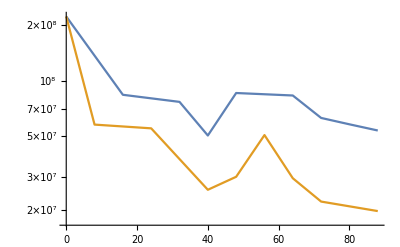

```mathematica
ListLogPlot[{ReadDepths2M3, ReadDepths4M3}, Joined -> True]
```

Convert read trajectories to approximate number trajectories for plotting purposes. Export to file.

```mathematica
PopSize=5*10^8;
```

```mathematica
ExtinctLineages={};
CellNumberTrajectories2M3=Table[
If[Mod[Barcode, 50000]==0, Print[Barcode];];
NumberTraj1=Table[{ReadTrajectories2M3[[Barcode]][[i]][[1]],If[ReadTrajectories2M3[[Barcode]][[i]][[2]]==0,0,N[(PopSize/(ReadDepths2M3[[i]][[2]]))*(ReadTrajectories2M3[[Barcode]][[i]][[2]])] ]}, {i, 1, Length[ReadDepths2M3]}];

TimePointsBarcodeUnRead=Sort[Map[First,Select[NumberTraj1, #[[2]]==0&]], #1>#2&];
(*Print["TimePointsBarcodeUnRead=", TimePointsBarcodeUnRead];*)
TimePointsBarcodeRead=Complement[TimePoints2M3,TimePointsBarcodeUnRead];
(*Print["TimePointsBarcodeRead=", TimePointsBarcodeRead];*)

If[Length[TimePointsBarcodeUnRead]>0&&Max[TimePointsBarcodeRead]<Min[TimePointsBarcodeUnRead], ExtinctLineage=1; AppendTo[ExtinctLineages, Barcode];, ExtinctLineage=0];

If[ExtinctLineage==1, NumberTraj2=Replace[NumberTraj1, 0-> 0.1, {2}], NumberTraj2=NumberTraj1];

NumberTraj2

, {Barcode, 1,Length[ReadTrajectories2M3]}];

TableForm[CellNumberTrajectories2M3[[1;;10]], TableHeadings -> {Table[StringJoin["Barcode",ToString[i]], {i, 1, 10}],Table[StringJoin["t=",ToString[TimePoints2M3[[i]]]], {i, 1, Length[TimePoints2M3]}]}]
Export["CellNumberTrajectories2M3.csv", CellNumberTrajectories2M3, "CSV"];
Export["ExtinctLineages2M3.csv", ExtinctLineages, "CSV"];
```

50000

100000

150000

200000

250000

300000

350000

400000

450000

| t=0 | t=16 | t=32 | t=40 | t=48 | t=64 | t=72 | t=80 | t=88
Barcode1 | 0
829.98 | 16
882.578 | 32
781.629 | 40
742.364 | 48
612.451 | 64
944.501 | 72
890.93 | 80
792.317 | 88
734.792
Barcode2 | 0
3589.83 | 16
4335.37 | 32
3725.77 | 40
3850.39 | 48
3995.51 | 64
3272.67 | 72
2537.56 | 80
2549.19 | 88
1971.85
Barcode3 | 0
3200.71 | 16
2874.34 | 32
3074.41 | 40
2900.17 | 48
2904.77 | 64
3001.95 | 72
3094.39 | 80
2127.2 | 88
2092.76
Barcode4 | 0
2280.76 | 16
2403.24 | 32
2383.97 | 40
2088.52 | 48
1907.35 | 64
1425.78 | 72
1185.25 | 80
1024.85 | 88
958.02
Barcode5 | 0
789.493 | 16
655.97 | 32
931.441 | 40
692.873 | 48
997.419 | 64
866.294 | 72
795.473 | 80
809.541 | 88
809.201
Barcode6 | 0
652.288 | 16
447.253 | 32
592.735 | 40
376.131 | 48
484.128 | 64
511.354 | 72
373.872 | 80
318.649 | 88
409.251
Barcode7 | 0
2089.57 | 16
1639.93 | 32
1849.86 | 40
1979.64 | 48
1767.36 | 64
2304.1 | 72
2259.14 | 80
1937.73 | 88
2343.89
Barcode8 | 0
1875.89 | 16
1610.11 | 32
1478.58 | 40
1613.4 | 48
1032.42 | 64
1088.88 | 72
1201.16 | 80
895.663 | 88
641.78
Barcode9 | 0
1644.22 | 16
2117. | 32
1817.29 | 40
1949.94 | 48
2245.65 | 64
1804.78 | 72
2084.14 | 80
1593.25 | 88
1543.99
Barcode10 | 0
1844.4 | 16
1395.43 | 32
1042.17 | 40
940.328 | 48
1125.74 | 64
968.565 | 72
1057.98 | 80
990.396 | 88
483.66

```mathematica
ExtinctLineages={};
CellNumberTrajectories4M3=Table[
If[Mod[Barcode, 50000]==0, Print[Barcode];];
NumberTraj1=Table[{ReadTrajectories4M3[[Barcode]][[i]][[1]],If[ReadTrajectories4M3[[Barcode]][[i]][[2]]==0,0,N[(PopSize/(ReadDepths4M3[[i]][[2]]))*(ReadTrajectories4M3[[Barcode]][[i]][[2]])] ]}, {i, 1, Length[ReadDepths4M3]}];

TimePointsBarcodeUnRead=Sort[Map[First,Select[NumberTraj1, #[[2]]==0&]], #1>#2&];
(*Print["TimePointsBarcodeUnRead=", TimePointsBarcodeUnRead];*)
TimePointsBarcodeRead=Complement[TimePoints4M3,TimePointsBarcodeUnRead];
(*Print["TimePointsBarcodeRead=", TimePointsBarcodeRead];*)

If[Length[TimePointsBarcodeUnRead]>0&&Max[TimePointsBarcodeRead]<Min[TimePointsBarcodeUnRead], ExtinctLineage=1; AppendTo[ExtinctLineages, Barcode];, ExtinctLineage=0];

If[ExtinctLineage==1, NumberTraj2=Replace[NumberTraj1, 0-> 0.1, {2}], NumberTraj2=NumberTraj1];

NumberTraj2

, {Barcode, 1,Length[ReadTrajectories4M3]}];

TableForm[CellNumberTrajectories4M3[[1;;10]], TableHeadings -> {Table[StringJoin["Barcode",ToString[i]], {i, 1, 10}],Table[StringJoin["t=",ToString[TimePoints4M3[[i]]]], {i, 1, Length[TimePoints4M3]}]}]
Export["CellNumberTrajectories4M3.csv", CellNumberTrajectories4M3, "CSV"];
Export["ExtinctLineages4M3.csv", ExtinctLineages, "CSV"];
```

50000

100000

150000

200000

250000

300000

350000

400000

450000

| t=0 | t=8 | t=24 | t=40 | t=48 | t=56 | t=64 | t=72 | t=88
Barcode1 | 0
829.98 | 8
1062.99 | 24
742.47 | 40
1750.67 | 48
2118.15 | 56
3781.01 | 64
7027.64 | 72
18271.1 | 88
40323.3
Barcode2 | 0
3589.83 | 8
3595.15 | 24
3377.33 | 40
3034.49 | 48
2829.71 | 56
2638.83 | 64
2629.05 | 72
2207.86 | 88
1749.88
Barcode3 | 0
3200.71 | 8
3067.98 | 24
3422.6 | 40
3793.11 | 48
3739.85 | 56
2747.14 | 64
2999.81 | 72
3221.67 | 88
2586.78
Barcode4 | 0
2280.76 | 8
2635.87 | 24
2281.74 | 40
1711.76 | 48
2068.5 | 56
2628.98 | 64
2359.4 | 72
2095.21 | 88
1572.36
Barcode5 | 0
789.493 | 8
734.586 | 24
679.088 | 40
875.333 | 48
777.757 | 56
423.394 | 64
623.556 | 72
765.991 | 88
456.49
Barcode6 | 0
652.288 | 8
725.943 | 24
570.434 | 40
447.392 | 48
562.633 | 56
886.174 | 64
724.673 | 72
518.171 | 88
481.851
Barcode7 | 0
2089.57 | 8
1970.42 | 24
1928.61 | 40
2061.9 | 48
2482.2 | 56
2028.35 | 64
2123.46 | 72
2050.15 | 88
2028.85
Barcode8 | 0
1875.89 | 8
1814.86 | 24
1991.99 | 40
1770.12 | 48
1886.47 | 56
2284.36 | 64
2443.66 | 72
2500.74 | 88
2333.17
Barcode9 | 0
1644.22 | 8
1633.37 | 24
1765.63 | 40
1847.92 | 48
1472.77 | 56
1329.26 | 64
1567.32 | 72
1644.63 | 88
1014.42
Barcode10 | 0
1844.4 | 8
1728.44 | 24
1856.17 | 40
1633.95 | 48
1820.28 | 56
1270.18 | 64
1432.49 | 72
1148.99 | 88
862.259

## 2. Noise model

### Notes on the model and importing data

This distribution comes up in many of the processes because it is the approximation of the inverse laplace transform of 

M(ϕ) = exp(- a ϕ / (b ϕ +1))

which is a form that appears in birth death processes. The function is peaked around a but has an exponential tail rather than a Gaussian one.

```mathematica
LogProb[a_, b_, n_]:=-(√n-√a)^2/b+Log[√((√a)/(4 π b n^(3/2)))]
```

Use this form to estimate: κ, and xbar between neighboring time points. We condition on a number of reads r1 then fit the measured distribution of reads r2 conditioned on r1 i.e. P(r2|r1). We perform a two parameter fit for (xbar, κ) using the above form for the distribution with

a=(R2/R1)*r1*Exp[-(t2-t1)*xbar  --- the mean decline
b=κ

We do this conditioning on reads between 20 - 30 then take the mean of the fitted parameters. 20-30 is chosen because it is small enouht that we assume neutral, but not too small than integer number effects and fact we do not model things perfectly at small n become important.

The outputted mean fit values between the neighboring time points is written in to a file as is the series of plots showing how well the fit works across all r1 from LowerReadLimit (20 normally) to UpperReadLimit (40 usually).

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/CarbonData"];

ReadTrajectories2M3=ToExpression[Import["ReadTrajectories2M3.csv"]];
ReadDepths2M3=ToExpression[Import["ReadDepths2M3.csv"]];

ReadTrajectories4M3=ToExpression[Import["ReadTrajectories4M3.csv"]];
ReadDepths4M3=ToExpression[Import["ReadDepths4M3.csv"]];
```

### Inferring the mean fitness and unadaptive fraction

```mathematica
TimePoints2M3={0,16,32, 40, 48, 64, 72, 80, 88, 96, 104, 112};
TimePoints4M3={0,8,24, 40, 48,56, 64, 72,88, 96};
```

```mathematica
LowerReadLimit=20;
UpperReadLimit=40;
GridOfFittedPlots=Table[Table[,{r, LowerReadLimit,UpperReadLimit}], {t, 1, Length[TimePoints2M3]-1}];
AllxBarKappaFits=Table[
t1=TimePoints2M3[[t]];
t2=TimePoints2M3[[t+1]];
R1=ReadDepths2M3[[t]][[2]];
R2=ReadDepths2M3[[t+1]][[2]];

ReadNumbersToUse=Table[i, {i, LowerReadLimit, UpperReadLimit}];

Allr1Fits=Table[
r1=r0;
pm=1;

BarcodesInRange={};

Do[
Measuredr1=ReadTrajectories2M3[[Barcode]][[t]][[2]];
If[Abs[Measuredr1-r1]≤ pm, AppendTo[BarcodesInRange, Barcode]];, {Barcode, 1,Length[ReadTrajectories2M3]}];
Setofr2Reads=DeleteCases[Table[ReadTrajectories2M3[[Barcode]][[t+1]][[2]], {Barcode, BarcodesInRange}], 0];
NumberOfBarcodesInRange=Length[BarcodesInRange];
Minr2=Max[{Min[Setofr2Reads], 5}];Maxr2=Max[Setofr2Reads];
r2Distribution=BinCounts[Setofr2Reads, {Minr2, Maxr2, 1}];
(*Print[TableForm[r2Distribution]];*)
Predictedr2Reads[xbar_, κ_]:=Table[NumberOfBarcodesInRange*Exp[LogProb[(R2/R1)*r1*Exp[-(t2-t1)*xbar],κ,r2]], {r2, Minr2, Maxr2-1, 1}];
GoodnessOfFit[xbar_, κ_]:=Total[N[(r2Distribution-Predictedr2Reads[xbar, κ])^2]];

FittedxBarKappa=NMinimize[{GoodnessOfFit[x, y], 0.00001<x<0.5, 0.5<y<6}, {x,y}];
xBar=FittedxBarKappa[[2]][[1]][[2]];
Kappa=FittedxBarKappa[[2]][[2]][[2]];
Print["xbar=",xBar,"Kappa=",Kappa];


Fittedr2Reads=Table[{r2+0.5,NumberOfBarcodesInRange*Exp[LogProb[(R2/R1)*r1*Exp[-(t2-t1)*xBar],Kappa,r2]]}, {r2, Minr2, 2*Maxr2, 1}];

Fittedr2ReadsNoMean=Table[{r2+0.5,NumberOfBarcodesInRange*Exp[LogProb[(R2/R1)*r1,Kappa,r2]]}, {r2, Minr2, 2*Maxr2, 1}];

LogData=Histogram[Setofr2Reads, {1}, "LogCount",PlotRange ->{{1, 80},All},Frame -> True,AxesOrigin -> {0, -1},FrameLabel -> {Text[Style["Number of reads", 12,FontFamily-> "Helvetica"]],Text[Style["Number of barcodes", 12,FontFamily-> "Helvetica"]]}, FrameTicksStyle->Directive[Black,12, FontFamily-> "Helvetica"], ChartStyle ->Directive[{c4, EdgeForm[None]}]];
LogTheory=ListLogPlot[{Fittedr2Reads, Fittedr2ReadsNoMean},Joined -> True, AxesOrigin -> {0, -1},PlotStyle-> {{Black, Thickness[0.01]},{Black, Dashing[0.03]} }, PlotRange ->{{1, 80},{-1,Log[Max[r2Distribution]]}}];
LOGPLOT=Show[{LogData, LogTheory}, PlotLabel-> Text[Style[StringJoin["κ=",ToString[Kappa],"    x̄=",ToString[xBar],"   r=",ToString[Round[r0]]],12, FontFamily-> "Helvetica"]], ImageSize -> 250, PlotRange -> {{1, 80},{-1,Log[Max[r2Distribution]]}}, PlotRangeClipping -> True, AxesOrigin -> {0, -1}];
GridOfFittedPlots[[t]][[r0-LowerReadLimit+1]]=LOGPLOT;

{xBar, Kappa}

, {r0,ReadNumbersToUse}];
Mean[Allr1Fits]

, {t, 1,Length[TimePoints2M3]-1}];

Export["InferredxBarAndKappa2M3.csv", AllxBarKappaFits, "CSV"];
Export["PlotsOfInferredxBarAndKappa2M3.pdf",TableForm[GridOfFittedPlots, TableHeadings -> {Table[StringJoin[ToString[TimePoints2M3[[i]]],"-",ToString[TimePoints2M3[[i+1]]]], {i, 1, Length[TimePoints2M3]-1}],Table[r, {r, LowerReadLimit,UpperReadLimit}]}], "PDF"];
Speak["Finished evaluating"];
```

```mathematica
LowerReadLimit=20;
UpperReadLimit=40;
GridOfFittedPlots=Table[Table[,{r, LowerReadLimit,UpperReadLimit}], {t, 1, Length[TimePoints4M3]-1}];
AllxBarKappaFits=Table[
t1=TimePoints4M3[[t]];
t2=TimePoints4M3[[t+1]];
R1=ReadDepths4M3[[t]][[2]];
R2=ReadDepths4M3[[t+1]][[2]];

ReadNumbersToUse=Table[i, {i, LowerReadLimit, UpperReadLimit}];

Allr1Fits=Table[
r1=r0;
pm=1;

BarcodesInRange={};

Do[
Measuredr1=ReadTrajectories4M3[[Barcode]][[t]][[2]];
If[Abs[Measuredr1-r1]≤ pm, AppendTo[BarcodesInRange, Barcode]];, {Barcode, 1,Length[ReadTrajectories4M3]}];
Setofr2Reads=DeleteCases[Table[ReadTrajectories4M3[[Barcode]][[t+1]][[2]], {Barcode, BarcodesInRange}], 0];
NumberOfBarcodesInRange=Length[BarcodesInRange];
Minr2=Max[{Min[Setofr2Reads], 5}];Maxr2=Max[Setofr2Reads];
r2Distribution=BinCounts[Setofr2Reads, {Minr2, Maxr2, 1}];
(*Print[TableForm[r2Distribution]];*)
Predictedr2Reads[xbar_, κ_]:=Table[NumberOfBarcodesInRange*Exp[LogProb[(R2/R1)*r1*Exp[-(t2-t1)*xbar],κ,r2]], {r2, Minr2, Maxr2-1, 1}];
GoodnessOfFit[xbar_, κ_]:=Total[N[(r2Distribution-Predictedr2Reads[xbar, κ])^2]];

FittedxBarKappa=NMinimize[{GoodnessOfFit[x, y], 0.00001<x<0.5, 0.5<y<6}, {x,y}];
xBar=FittedxBarKappa[[2]][[1]][[2]];
Kappa=FittedxBarKappa[[2]][[2]][[2]];
Print["xbar=",xBar,"Kappa=",Kappa];


Fittedr2Reads=Table[{r2+0.5,NumberOfBarcodesInRange*Exp[LogProb[(R2/R1)*r1*Exp[-(t2-t1)*xBar],Kappa,r2]]}, {r2, Minr2, 2*Maxr2, 1}];

Fittedr2ReadsNoMean=Table[{r2+0.5,NumberOfBarcodesInRange*Exp[LogProb[(R2/R1)*r1,Kappa,r2]]}, {r2, Minr2, 2*Maxr2, 1}];

LogData=Histogram[Setofr2Reads, {1}, "LogCount",PlotRange ->{{1, 80},All},Frame -> True,AxesOrigin -> {0, -1},FrameLabel -> {Text[Style["Number of reads", 12,FontFamily-> "Helvetica"]],Text[Style["Number of barcodes", 12,FontFamily-> "Helvetica"]]}, FrameTicksStyle->Directive[Black,12, FontFamily-> "Helvetica"], ChartStyle ->Directive[{c4, EdgeForm[None]}]];
LogTheory=ListLogPlot[{Fittedr2Reads, Fittedr2ReadsNoMean},Joined -> True, AxesOrigin -> {0, -1},PlotStyle-> {{Black, Thickness[0.01]},{Black, Dashing[0.03]} }, PlotRange ->{{1, 80},{-1,Log[Max[r2Distribution]]}}];
LOGPLOT=Show[{LogData, LogTheory}, PlotLabel-> Text[Style[StringJoin["κ=",ToString[Kappa],"    x̄=",ToString[xBar],"   r=",ToString[Round[r0]]],12, FontFamily-> "Helvetica"]], ImageSize -> 250, PlotRange -> {{1, 80},{-1,Log[Max[r2Distribution]]}}, PlotRangeClipping -> True, AxesOrigin -> {0, -1}];
GridOfFittedPlots[[t]][[r0-LowerReadLimit+1]]=LOGPLOT;

{xBar, Kappa}

, {r0,ReadNumbersToUse}];
Mean[Allr1Fits]

, {t, 1,Length[TimePoints4M3]-1}];

Export["InferredxBarAndKappa4M3.csv", AllxBarKappaFits, "CSV"];
Export["PlotsOfInferredxBarAndKappa4M3.pdf",TableForm[GridOfFittedPlots, TableHeadings -> {Table[StringJoin[ToString[TimePoints2M3[[i]]],"-",ToString[TimePoints2M3[[i+1]]]], {i, 1, Length[TimePoints2M3]-1}],Table[r, {r, LowerReadLimit,UpperReadLimit}]}], "PDF"];
Speak["Finished evaluating"];
```

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/EarlyTime"];
xBarKappa2M3=ToExpression[Import["InferredxBarAndKappa2M3.csv"]];
TimePoints2M3={0,16,32, 40, 48, 64, 72, 80, 88};
MeanFitnessList2M3=Table[{TimePoints2M3[[i+1]], xBarKappa2M3[[i]][[1]]},{i, 1, Length[xBarKappa2M3]}];
KappaList2M3=Table[{TimePoints2M3[[i+1]], xBarKappa2M3[[i]][[2]]},{i, 1, Length[xBarKappa2M3]}];

SetDirectory["~/Dropbox/BayesianAnalysis/EarlyTime"];
xBarKappa4M3=ToExpression[Import["InferredxBarAndKappa4M3.csv"]];
TimePoints4M3={0,8,24, 40, 48,56, 64, 72,88};
MeanFitnessList4M3=Table[{TimePoints4M3[[i+1]], xBarKappa4M3[[i]][[1]]},{i, 1, Length[xBarKappa4M3]}];
KappaList4M3=Table[{TimePoints4M3[[i+1]], xBarKappa4M3[[i]][[2]]},{i, 1, Length[xBarKappa4M3]}];
```

```mathematica
FitForm[U_, s_]:=Table[{t, U/s(Exp[s t]-1)}, {t, 0, 88,8}]
```

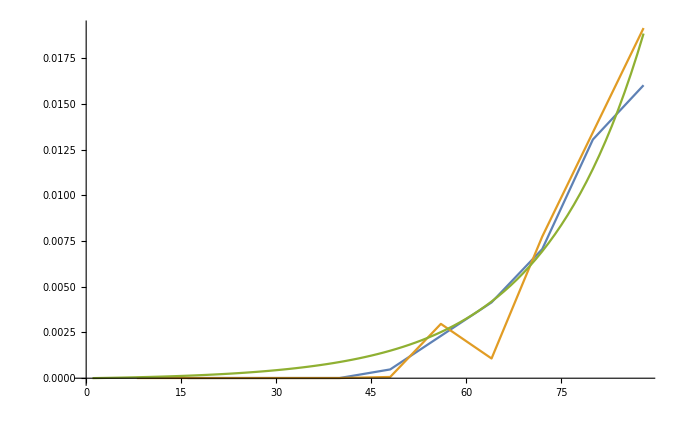

```mathematica
ListPlot[{MeanFitnessList2M3,MeanFitnessList4M3, FitForm[10^-5.3, 0.062]}, Joined -> True]
```

```mathematica
MeanFitnessList2M3=Delete[Table[{t,10^-5.3/0.062(Exp[ 0.062 t]-1)},{t, TimePoints2M3}],1]
MeanFitnessList4M3=Delete[Table[{t,10^-5.3/0.062(Exp[ 0.062 t]-1)},{t, TimePoints2M3}],1]
```

{{16,0.000137149},{32,0.000506989},{40,0.000884455},{48,0.00150431},{64,0.0041937},{72,0.00693855},{80,0.011446},{88,0.0188478}}

{{16,0.000137149},{32,0.000506989},{40,0.000884455},{48,0.00150431},{64,0.0041937},{72,0.00693855},{80,0.011446},{88,0.0188478}}

## 3. Calculating probabilities

### Inference

Importing the data for both 2M3 and 4M3

```mathematica
$HistoryLength=0;
```

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/2M3"];
ReadTrajectories2M3=ToExpression[Import["ReadTrajectories2M3.csv"]];
ReadDepths2M3=ToExpression[Import["ReadDepths2M3.csv"]];
CellNumberTrajectories2M3=ToExpression[Import["CellNumberTrajectories2M3.csv"]];
ClearMemory
```

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/4M3"];
ReadTrajectories4M3=ToExpression[Import["ReadTrajectories4M3.csv"]];
ReadDepths4M3=ToExpression[Import["ReadDepths4M3.csv"]];
CellNumberTrajectories4M3=ToExpression[Import["CellNumberTrajectories4M3.csv"]];
ClearMemory
```

Parameters that are useful to define

```mathematica
T=8;
PopSize=5*10^8;
NumberOfBarcodes=Length[ReadTrajectories2M3];
```

Mean fitness list defined so that the mean fitness at 16 corresponds to the mean fitness accounting for reduction in freqs from 8-16.

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/2M3"];
xBarKappa2M3=ToExpression[Import["InferredxBArAndKappa2M3.csv"]];
TimePoints2M3={0,16,32, 40, 48, 64, 72, 80, 88, 96, 104, 112};
MeanFitnessList2M3=Table[{TimePoints2M3[[i+1]], xBarKappa2M3[[i]][[1]]},{i, 1, Length[xBarKappa2M3]}];
KappaList2M3=Table[{TimePoints2M3[[i+1]], xBarKappa2M3[[i]][[2]]},{i, 1, Length[xBarKappa2M3]}];

SetDirectory["~/Dropbox/BayesianAnalysis/4M3"];
xBarKappa4M3=ToExpression[Import["InferredxBArAndKappa4M3.csv"]];
TimePoints4M3={0,8,24, 40, 48,56, 64, 72,88, 96};
MeanFitnessList4M3=Table[{TimePoints4M3[[i+1]], xBarKappa4M3[[i]][[1]]},{i, 1, Length[xBarKappa4M3]}];
KappaList4M3=Table[{TimePoints4M3[[i+1]], xBarKappa4M3[[i]][[2]]},{i, 1, Length[xBarKappa4M3]}];
```

Determine the interpolation formulae for mean fitness and the unadaptive fraction (integral of mean fitness over time)

```mathematica
MeanFitnessBeforeZero2M3=Table[ {8i, 10^-7}, {i, -25, TimePoints2M3[[1]]/T}];
MeanFitnessExtended2M3=Join[ MeanFitnessBeforeZero2M3,MeanFitnessList2M3];
UnAdaptedFraction2M3=Table[{MeanFitnessExtended2M3[[j]][[1]],Exp[-Sum[(MeanFitnessExtended2M3[[t]][[1]]-MeanFitnessExtended2M3[[t-1]][[1]])*MeanFitnessExtended2M3[[t]][[2]], {t, 2,j}]]}, {j, 2, Length[MeanFitnessExtended2M3]}];
InterpolatedMeanFitness2M3=Interpolation[MeanFitnessExtended2M3, InterpolationOrder->1];
InterpolatedUnAdaptiveFraction2M3=Interpolation[UnAdaptedFraction2M3, InterpolationOrder->1];

MeanFitnessBeforeZero4M3=Table[ {8i, 10^-7}, {i, -25, TimePoints4M3[[1]]/T}];
MeanFitnessExtended4M3=Join[ MeanFitnessBeforeZero4M3,MeanFitnessList4M3];
UnAdaptedFraction4M3=Table[{MeanFitnessExtended4M3[[j]][[1]],Exp[-Sum[(MeanFitnessExtended4M3[[t]][[1]]-MeanFitnessExtended4M3[[t-1]][[1]])*MeanFitnessExtended4M3[[t]][[2]], {t, 2,j}]]}, {j, 2, Length[MeanFitnessExtended4M3]}];
InterpolatedMeanFitness4M3=Interpolation[MeanFitnessExtended4M3, InterpolationOrder->1];
InterpolatedUnAdaptiveFraction4M3=Interpolation[UnAdaptedFraction4M3, InterpolationOrder->1];
```

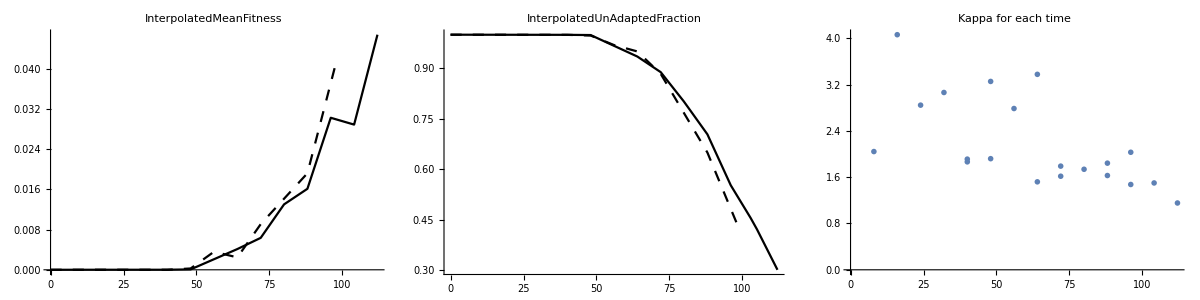

```mathematica
TableForm[{{

Show[{Plot[InterpolatedMeanFitness2M3[x], {x, 0, 112}, PlotLabel -> "InterpolatedMeanFitness", PlotStyle -> Black],Plot[InterpolatedMeanFitness4M3[x], {x, 0, 98}, PlotLabel -> "InterpolatedMeanFitness", PlotStyle -> Directive[{Black, Dashing[0.02]}]]},ImageSize -> 400],

Show[{Plot[InterpolatedUnAdaptiveFraction2M3[x], {x, 0, 112}, PlotLabel -> "InterpolatedUnAdaptedFraction", PlotStyle -> Black],Plot[InterpolatedUnAdaptiveFraction4M3[x], {x, 0, 98}, PlotLabel ->"InterpolatedUnAdaptedFraction", PlotStyle -> Directive[{Black, Dashing[0.02]}]] },ImageSize -> 400],

Show[{ListPlot[KappaList2M3, PlotMarkers -> Markers[0.025, Black, Thickness[0.005]], PlotLabel -> "Kappa for each time"],ListPlot[KappaList4M3, PlotMarkers -> Markers[0.025,White, Thickness[0.005]], PlotLabel -> "Kappa for each time"]}, ImageSize -> 400]}}]
```

Establishment time as a function of s and τ. True establishment size is 1/(s-x̄(τ))

```mathematica
EstablishmentSize2M3[s_, τ_]:=1/(s-InterpolatedMeanFitness2M3[τ])*UnitStep[s-(InterpolatedMeanFitness2M3[τ]+0.005)]+1/0.005*UnitStep[-(s-(InterpolatedMeanFitness2M3[τ]+0.005))];

EstablishmentSize4M3[s_, τ_]:=1/(s-InterpolatedMeanFitness4M3[τ])*UnitStep[s-(InterpolatedMeanFitness4M3[τ]+0.005)]+1/0.005*UnitStep[-(s-(InterpolatedMeanFitness4M3[τ]+0.005))];
```

Given this the r2 is fixed by the deterministic growth of the beneficial cells emerging from τ with fitness s.

```mathematica
Meanr2Givenr12M3[r1_,R1_,R2_,t1_,t2_,s_,τ_, PopSize_]:=
Module[{TotalNumberOfCells,NumberOfBeneficialCells,NumberOfNeutralCells,TotalNumberOfCellsAtt2,NumberOfReadsr2},
TotalNumberOfCells=PopSize(r1/R1);
NumberOfBeneficialCells=(*Exp[-s τ](Exp[s t1]-1)*)Exp[s (t1-τ)]*EstablishmentSize2M3[s, τ]*InterpolatedUnAdaptiveFraction2M3[t1]/InterpolatedUnAdaptiveFraction2M3[τ];
NumberOfNeutralCells=TotalNumberOfCells-NumberOfBeneficialCells;

If[NumberOfBeneficialCells≥TotalNumberOfCells, NumberOfNeutralCells=0;NumberOfBeneficialCells=TotalNumberOfCells;];

TotalNumberOfCellsAtt2=(NumberOfNeutralCells+Exp[s(t2-t1)]*NumberOfBeneficialCells)*InterpolatedUnAdaptiveFraction2M3[t2]/InterpolatedUnAdaptiveFraction2M3[t1];

NumberOfReadsr2=(TotalNumberOfCellsAtt2/PopSize)*R2;
NumberOfReadsr2];

Meanr2Givenr14M3[r1_,R1_,R2_,t1_,t2_,s_,τ_, PopSize_]:=
Module[{TotalNumberOfCells,NumberOfBeneficialCells,NumberOfNeutralCells,TotalNumberOfCellsAtt2,NumberOfReadsr2},
TotalNumberOfCells=PopSize(r1/R1);
NumberOfBeneficialCells=(Exp[s (t1-τ)])*EstablishmentSize4M3[s, τ]*InterpolatedUnAdaptiveFraction4M3[t1]/InterpolatedUnAdaptiveFraction4M3[τ];
NumberOfNeutralCells=TotalNumberOfCells-NumberOfBeneficialCells;

If[NumberOfBeneficialCells≥TotalNumberOfCells, NumberOfNeutralCells=0;NumberOfBeneficialCells=TotalNumberOfCells;];

TotalNumberOfCellsAtt2=(NumberOfNeutralCells+Exp[s(t2-t1)]*NumberOfBeneficialCells)*InterpolatedUnAdaptiveFraction4M3[t2]/InterpolatedUnAdaptiveFraction4M3[t1];

NumberOfReadsr2=(TotalNumberOfCellsAtt2/PopSize)*R2;
NumberOfReadsr2];
```

The propagator is then simply the standard error function with κ as the noise and the mean set by the above function

Dealing with logs is better than the probability itself or numbers get too large and computational overflow occurs.

```mathematica
LogPropagator2M3[r1_,r2_,R1_,R2_,t1_,t2_,PopSize_,κ_,s_,τ_]:=LogProb[
Meanr2Givenr12M3[r1,R1,R2,t1,t2,s,τ, PopSize], κ, r2]

LogPropagator4M3[r1_,r2_,R1_,R2_,t1_,t2_,PopSize_,κ_,s_,τ_]:=LogProb[
Meanr2Givenr14M3[r1,R1,R2,t1,t2,s,τ, PopSize], κ, r2]
```

The prior distriution on (s, τ) is set by the theory of a constant feeding process. If a constant population of size n0 is feeding mutants at rate μ(s)δs into fitness range (s, s+δs) then the statistics of the establishment times follow from solving the backwards time generating function equations. 

The distribution is ρ(τ) = (s dτ / Γ(n U))*exp(-n U s τ - e^(-s τ))

To do this we need to have a prior distribution over μ(s)ds. This we have to guess initially and then can improve upon once

```mathematica
DeltaS=0.1;
μTrial[s_]:=10^-5 1/DeltaS Exp[-s/DeltaS];
LogPriorDensityTau[τ_,s_,n_, U_]:=Log[n U s]
```

```mathematica
LogProbFirstTimePoint2M3[r_, s_, τ_, Neutral_]:=Module[{NumberOfBeneficialCellsAtZero,NumberOfCellsInferredAtZero, ExpectedReadsAtZero,TotalNumberOfCellsAtZero, ProbOft0},
If[Neutral==1,ProbOft0=LogProb[r, 2, r],
NumberOfBeneficialCellsAtZero=Exp[-s τ]*EstablishmentSize2M3[s, τ]*1/InterpolatedUnAdaptiveFraction2M3[τ];
NumberOfCellsInferredAtZero=(r*PopSize)/(ReadDepths2M3[[1]][[2]]);
 TotalNumberOfCellsAtZero=NumberOfCellsInferredAtZero;

If[NumberOfBeneficialCellsAtZero>NumberOfCellsInferredAtZero, TotalNumberOfCellsAtZero=NumberOfBeneficialCellsAtZero];
ExpectedReadsAtZero=TotalNumberOfCellsAtZero/PopSize*ReadDepths2M3[[1]][[2]];
ProbOft0=LogProb[ExpectedReadsAtZero, 2, r]];
ProbOft0]

LogProbFirstTimePoint4M3[r_, s_, τ_, Neutral_]:=Module[{NumberOfBeneficialCellsAtZero,NumberOfCellsInferredAtZero, ExpectedReadsAtZero,TotalNumberOfCellsAtZero, ProbOft0},
If[Neutral==1,ProbOft0=LogProb[r, 2, r],
NumberOfBeneficialCellsAtZero=Exp[-s τ]*EstablishmentSize4M3[s, τ]*1/InterpolatedUnAdaptiveFraction4M3[τ];
NumberOfCellsInferredAtZero=(r*PopSize)/(ReadDepths4M3[[1]][[2]]);
 TotalNumberOfCellsAtZero=NumberOfCellsInferredAtZero;

If[NumberOfBeneficialCellsAtZero>NumberOfCellsInferredAtZero, TotalNumberOfCellsAtZero=NumberOfBeneficialCellsAtZero];
ExpectedReadsAtZero=TotalNumberOfCellsAtZero/PopSize*ReadDepths4M3[[1]][[2]];
ProbOft0=LogProb[ExpectedReadsAtZero, 2, r]];
ProbOft0]
```

```mathematica
t1=SessionTime[];
TableOfPlots={};
TableOfData={};
Do[
Traj2M3=Replace[ReadTrajectories2M3[[Barcode]], 0-> 1, 2];(*Get rid of zeros since prob does not model them.*)
Traj4M3=Replace[ReadTrajectories4M3[[Barcode]], 0-> 1, 2];(*Get rid of zeros since prob does not model them.*)


(*DETERMINE INITIAL SIZE OF EACH LINEAGE*)

InitialLineageSize2M3=PopSize/(ReadDepths2M3[[1]][[2]])*Traj2M3[[1]][[2]];
InitialLineageSize4M3=PopSize/(ReadDepths4M3[[1]][[2]])*Traj4M3[[1]][[2]];
(*Print["n0_2M3=",N[InitialLineageSize2M3]];
Print["n0_4M3=",N[InitialLineageSize4M3]];*)

δs=0.005;
δτ=1;


(*PROBABILITY OF THE NULL HYPOTHESIS*)

WeightOfT0For2M3=-LogProbFirstTimePoint2M3[Traj2M3[[1]][[2]], 0, 0, 1];
WeightOfLaterTFor2M3=Sum[-LogPropagator2M3[Traj2M3[[t]][[2]],Traj2M3[[t+1]][[2]],ReadDepths2M3[[t]][[2]],ReadDepths2M3[[t+1]][[2]],TimePoints2M3[[t]],TimePoints2M3[[t+1]],10^5 PopSize,KappaList2M3[[t]][[2]],0.00001,0], {t, 1,  Length[TimePoints2M3]-1}];
WeightNotBeneficial2M3=WeightOfT0For2M3+WeightOfLaterTFor2M3;
(*Print["T0 2M3 =",N[WeightOfT0For2M3],"Later T 2M3 = ",WeightOfLaterTFor2M3,"Total Weight2M3 = ",WeightNotBeneficial2M3];*)

WeightOfT0For4M3=-LogProbFirstTimePoint4M3[Traj4M3[[1]][[2]], 0, 0, 1];
WeightOfLaterTFor4M3=Sum[-LogPropagator4M3[Traj4M3[[t]][[2]],Traj4M3[[t+1]][[2]],ReadDepths4M3[[t]][[2]],ReadDepths4M3[[t+1]][[2]],TimePoints4M3[[t]],TimePoints4M3[[t+1]],10^5 PopSize,KappaList4M3[[t]][[2]],0.00001,0], {t, 1,  Length[TimePoints4M3]-1}];
WeightNotBeneficial4M3=WeightOfT0For4M3+WeightOfLaterTFor4M3;
(*Print["T0 4M3 =",N[WeightOfT0For4M3],"Later T 4M3 = ",WeightOfLaterTFor4M3,"Total Weight 4M3 = ",WeightNotBeneficial4M3];*)

If[ Or[WeightNotBeneficial2M3>60,WeightNotBeneficial4M3>50],

t2=SessionTime[];
If[Mod[Barcode, 1]==0,Print[Barcode, "Memory=", MemoryInUse[], "  max",MaxMemoryUsed[]]; Print[t2-t1];];
t1=t2;

(*PROBABILITY OF THE S, T HYPOTHESIS*)

PriorWeight2M3[s_, τ_]:=-LogPriorDensityTau[τ, s,InitialLineageSize2M3, μTrial[s]*δs]-Log[δτ];
WeightT02M3[s_, τ_]:=-LogProbFirstTimePoint2M3[Traj2M3[[1]][[2]], s, τ, 0];
WeightOfLaterT2M3[s_, τ_]:=Sum[-LogPropagator2M3[Traj2M3[[t]][[2]],Traj2M3[[t+1]][[2]],ReadDepths2M3[[t]][[2]],ReadDepths2M3[[t+1]][[2]],TimePoints2M3[[t]],TimePoints2M3[[t+1]],PopSize,KappaList2M3[[t]][[2]],s,τ], {t, 1, Length[TimePoints2M3]-1}];

ProbSAndTauGivenData2M3[s_, τ_]:=PriorWeight2M3[s, τ]+WeightT02M3[s, τ]+WeightOfLaterT2M3[s, τ];


PriorWeight4M3[s_, τ_]:=-LogPriorDensityTau[τ, s,InitialLineageSize4M3, μTrial[s]*δs]-Log[δτ];
WeightT04M3[s_, τ_]:=-LogProbFirstTimePoint4M3[Traj4M3[[1]][[2]], s, τ, 0];
WeightOfLaterT4M3[s_, τ_]:=Sum[-LogPropagator4M3[Traj4M3[[t]][[2]],Traj4M3[[t+1]][[2]],ReadDepths4M3[[t]][[2]],ReadDepths4M3[[t+1]][[2]],TimePoints4M3[[t]],TimePoints4M3[[t+1]],PopSize,KappaList4M3[[t]][[2]],s,τ], {t, 1, Length[TimePoints4M3]-1}];

ProbSAndTauGivenData4M3[s_, τ_]:=PriorWeight4M3[s, τ]+WeightT04M3[s, τ]+WeightOfLaterT4M3[s, τ];


(*FIND MOST LIKELY S AND T FOR BOTH EXPERIMENTS*)

MostProbableSAndTau2M3=NMinimize[{ProbSAndTauGivenData2M3[s, τ], 0.005<s<0.4 && -150<τ<90}, {s, τ}, AccuracyGoal->6,MaxIterations->20,Method -> "NelderMead"(*{"SimulatedAnnealing", "SearchPoints"-> 100}*)];
MostProbableSAndTau4M3=NMinimize[{ProbSAndTauGivenData4M3[s, τ], 0.005<s<0.4 && -150<τ<90}, {s, τ}, AccuracyGoal->6,MaxIterations->20,Method -> "NelderMead"(*{"SimulatedAnnealing", "SearchPoints"-> 100}*)];
(*Print[Barcode,"   (s, τ)_2M3 =  ", MostProbableSAndTau2M3,"  (s, τ)_4M3 =  ", MostProbableSAndTau4M3];*)


(*IF PR[BENEFICIAL] > PR[NEUTRAL] THEN ASSIGN BEST FIT VALUES FOR S AND T, ELSE ASSIGN ZERO*)

InferredS2M3=MostProbableSAndTau2M3[[2]][[1]][[2]];
InferredTau2M3=MostProbableSAndTau2M3[[2]][[2]][[2]];
If[WeightNotBeneficial2M3>MostProbableSAndTau2M3[[1]],
InferredS2M3=MostProbableSAndTau2M3[[2]][[1]][[2]];
InferredTau2M3=MostProbableSAndTau2M3[[2]][[2]][[2]];
, 
InferredS2M3=0.00001; 
InferredTau2M3=0;];

InferredS4M3=MostProbableSAndTau4M3[[2]][[1]][[2]];
InferredTau4M3=MostProbableSAndTau4M3[[2]][[2]][[2]];
If[WeightNotBeneficial4M3>MostProbableSAndTau4M3[[1]],
InferredS4M3=MostProbableSAndTau4M3[[2]][[1]][[2]];
InferredTau4M3=MostProbableSAndTau4M3[[2]][[2]][[2]];
, 
InferredS4M3=0.00001; 
InferredTau4M3=0;];




(*LOOK AT CONTRIBUTIONS TO THE WEIGHTS*)
(*
Print["ML T0 2M3 =",N[WeightT02M3[InferredS2M3, InferredTau2M3]],"ML Later T 2M3 = ",WeightOfLaterT2M3[InferredS2M3, InferredTau2M3],"Total Weight ML 2M3 = ",ProbSAndTauGivenData2M3[InferredS2M3, InferredTau2M3]];
Print["ML T0 4M3 =",N[WeightT04M3[InferredS4M3, InferredTau4M3]],"ML Later T 4M3 = ",WeightOfLaterT4M3[InferredS4M3, InferredTau4M3],"Total Weight ML 4M3 = ",ProbSAndTauGivenData4M3[InferredS4M3, InferredTau4M3]];*)




(*ERRORS ON INFERRED VALUES FROM CURVATURE*)

If[InferredS2M3>0.001,
GradientInS2M3=-D[ProbSAndTauGivenData2M3[s, InferredTau2M3], s]/. s -> InferredS2M3;
GradientInTau2M3=-D[ProbSAndTauGivenData2M3[InferredS2M3, τ], τ]/. τ -> InferredTau2M3;

CurvatureSS2M3=D[D[ProbSAndTauGivenData2M3[s, InferredTau2M3], s], s]/. s -> InferredS2M3;
CurvatureST2M3=D[D[ProbSAndTauGivenData2M3[s, τ], s], τ]/. {s -> InferredS2M3, τ -> InferredTau2M3};
CurvatureTT2M3=D[D[ProbSAndTauGivenData2M3[InferredS2M3, τ], τ], τ]/. τ -> InferredTau2M3;

Kmatrix2M3={{CurvatureSS2M3,CurvatureST2M3},{CurvatureST2M3,CurvatureTT2M3}};
EigenValsAndVects2M3=Eigensystem[Kmatrix2M3];
PrincipleCurvature2M3=EigenValsAndVects2M3[[1]][[2]];
PrincipleCurvatureDirection2M3=EigenValsAndVects2M3[[2]][[2]];

ErrorInS2M3=Abs[PrincipleCurvatureDirection2M3[[1]]]/(√PrincipleCurvature2M3);ErrorInTau2M3=Abs[PrincipleCurvatureDirection2M3[[2]]]/(√PrincipleCurvature2M3);
,ErrorInS2M3=0.01;ErrorInTau2M3=5];


If[InferredS4M3>0.001,
GradientInS4M3=-D[ProbSAndTauGivenData4M3[s, InferredTau4M3], s]/. s -> InferredS4M3;
GradientInTau4M3=-D[ProbSAndTauGivenData4M3[InferredS4M3, τ], τ]/. τ -> InferredTau4M3;

CurvatureSS4M3=D[D[ProbSAndTauGivenData4M3[s, InferredTau4M3], s], s]/. s -> InferredS4M3;
CurvatureST4M3=D[D[ProbSAndTauGivenData4M3[s, τ], s], τ]/. {s -> InferredS4M3, τ -> InferredTau4M3};
CurvatureTT4M3=D[D[ProbSAndTauGivenData4M3[InferredS4M3, τ], τ], τ]/. τ -> InferredTau4M3;

Kmatrix4M3={{CurvatureSS4M3,CurvatureST4M3},{CurvatureST4M3,CurvatureTT4M3}};
EigenValsAndVects4M3=Eigensystem[Kmatrix4M3];
PrincipleCurvature4M3=EigenValsAndVects4M3[[1]][[2]];
PrincipleCurvatureDirection4M3=EigenValsAndVects4M3[[2]][[2]];

ErrorInS4M3=Abs[PrincipleCurvatureDirection4M3[[1]]]/(√PrincipleCurvature4M3);ErrorInTau4M3=Abs[PrincipleCurvatureDirection4M3[[2]]]/(√PrincipleCurvature4M3);
,ErrorInS4M3=0.01;ErrorInTau4M3=5];





(*PLOT THE RESULTS TO LOOK AT IF ADAPTIVE IN BOTH EXPERIMENTS AND OCCUR EARLY*)


If[Or[MostProbableSAndTau2M3[[1]]<WeightNotBeneficial2M3,MostProbableSAndTau4M3[[1]]<WeightNotBeneficial4M3] && RandomReal[]<1.0,

(*PosteriorPlot2M3=Show[{Plot3D[Exp[-ProbSAndTauGivenData2M3[s, τ]+ProbSAndTauGivenData2M3[InferredS2M3, InferredTau2M3]], {s,Max[InferredS2M3-5*ErrorInS2M3,0],InferredS2M3+5*ErrorInS2M3}, {τ,InferredTau2M3-5*ErrorInTau2M3,InferredTau2M3+5*ErrorInTau2M3},PlotRange -> {{0.001,0.3}, {-100,80},All},Boxed -> False,BoxRatios -> {1,1,0.6}, MaxRecursion->4, PlotPoints-> 40,ColorFunction->Function[{x,y,z},Scheme3[1+Log[10,Clip[z, {10^-10, 1}]]]],ColorFunctionScaling -> False, Mesh -> None,AxesLabel ->  {Text[Style["s", FontFamily-> "Helvetica", 11]],Text[Style["τ", FontFamily-> "Helvetica", 11]]},AxesEdge->{{-1,-1},{-1,-1},{-1,-1}}, ImageSize -> 200]}];

PosteriorPlot4M3=Show[{Plot3D[Exp[-ProbSAndTauGivenData4M3[s, τ]+ProbSAndTauGivenData4M3[InferredS4M3, InferredTau4M3]], {s,Max[InferredS4M3-5*ErrorInS4M3,0],InferredS4M3+5*ErrorInS4M3}, {τ,InferredTau4M3-5*ErrorInTau4M3,InferredTau4M3+5*ErrorInTau4M3},PlotRange -> {{0.001,0.3}, {-100,80},All},Boxed -> False,BoxRatios -> {1,1,0.6}, MaxRecursion->4, PlotPoints-> 40,ColorFunction->Function[{x,y,z},Scheme3[1+Log[10,Clip[z, {10^-10, 1}]]]],ColorFunctionScaling -> False, Mesh -> None,AxesLabel ->  {Text[Style["s", FontFamily-> "Helvetica", 11]],Text[Style["τ", FontFamily-> "Helvetica", 11]]},AxesEdge->{{-1,-1},{-1,-1},{-1,-1}}, ImageSize -> 200]}];*)

PosteriorPlot2M3=Show[{ArrayPlot[Table[-ProbSAndTauGivenData2M3[s, τ]+ProbSAndTauGivenData2M3[InferredS2M3, InferredTau2M3], {s,0.01,.15, .005}, {τ,-150,50, 1}], FrameLabel->{"s","τ"}, PlotRange -> {-100, 50}, AspectRatio->0.25]}];

PosteriorPlot4M3=Show[{ArrayPlot[Table[-ProbSAndTauGivenData4M3[s, τ]+ProbSAndTauGivenData4M3[InferredS4M3, InferredTau4M3], {s,0.01,.15, .005}, {τ,-150,50, 1}], FrameLabel->{"s","τ"}, PlotRange -> {-100, 50}, AspectRatio->0.25]}];

(*UnAdaptiveTrajectoryPlot2M3=ListLogPlot[Table[{t,CellNumberTrajectories2M3[[Barcode]][[1]][[2]]*InterpolatedUnAdaptiveFraction2M3[t]}, {t,0, 112}], Joined -> True, PlotStyle -> Directive[{c0, Thickness[0.007], Dashing[0.02]}], PlotRange -> {{0,115},{10, 10^6}},ImageSize -> 300];
UnAdaptiveTrajectoryPlot4M3=ListLogPlot[Table[{t,CellNumberTrajectories4M3[[Barcode]][[1]][[2]]*InterpolatedUnAdaptiveFraction4M3[t]}, {t,0, 96}], Joined -> True, PlotStyle -> Directive[{c3, Thickness[0.007], Dashing[0.02]}], PlotRange -> {{0,115},{10, 10^6}},ImageSize -> 300];*)

FittedTrajectoryPlot2M3=ListLogPlot[Table[{t,(CellNumberTrajectories2M3[[Barcode]][[1]][[2]]-Exp[InferredS2M3(0-InferredTau2M3)]*(InterpolatedUnAdaptiveFraction2M3[0]/InferredS2M3))*InterpolatedUnAdaptiveFraction2M3[t]+Exp[InferredS2M3(t-InferredTau2M3)]*(InterpolatedUnAdaptiveFraction2M3[t]/InferredS2M3)}, {t,0, 112}], Joined -> True, PlotStyle -> Directive[{c10, Thickness[0.007]}], PlotRange -> {{0,115},{10, 10^6}},ImageSize -> 300];

FittedTrajectoryPlot4M3=ListLogPlot[Table[{t,(CellNumberTrajectories4M3[[Barcode]][[1]][[2]]-Exp[InferredS4M3(0-InferredTau4M3)]*(InterpolatedUnAdaptiveFraction4M3[0]/InferredS4M3))*InterpolatedUnAdaptiveFraction4M3[t]+Exp[InferredS4M3(t-InferredTau4M3)]*(InterpolatedUnAdaptiveFraction4M3[t]/InferredS4M3)}, {t,0, 104}], Joined -> True, PlotStyle -> Directive[{RGBColor[0.77,0.04,0.], Thickness[0.007]}], PlotRange -> {{0,115},{10, 10^6}},ImageSize -> 300];

TrajectoryPlot2M3=ListLogPlot[CellNumberTrajectories2M3[[Barcode]], PlotMarkers ->Markers[0.02, c10, Thickness[0.003]],PlotRange -> {{0,115},{10, 10^6}}, ImageSize -> 300];
TrajectoryPlot4M3=ListLogPlot[CellNumberTrajectories4M3[[Barcode]], PlotMarkers ->Markers[0.02, RGBColor[0.77,0.04,0.], Thickness[0.003]],PlotRange -> {{0,115},{10, 10^6}}, ImageSize -> 300];

CompareTrajectoriesPlot=Show[{(*UnAdaptiveTrajectoryPlot2M3,UnAdaptiveTrajectoryPlot4M3,*)FittedTrajectoryPlot2M3,FittedTrajectoryPlot4M3, TrajectoryPlot2M3,TrajectoryPlot4M3}
, Frame -> True,FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Number of cells", FontFamily-> "Helvetica", 10]]}, FrameTicks->{{Table[{Log[10^k], Superscript[10,k]},{k, 0, 6}], None}, {Table[{8k, 8k}, {k, 0, 14,2}],None}}, ImageSize -> 200];

(*ADDING THE PLOT TO A TABLE*)

AppendTo[TableOfPlots, {Barcode,-MostProbableSAndTau2M3[[1]]+WeightNotBeneficial2M3,-MostProbableSAndTau4M3[[1]]+WeightNotBeneficial4M3,InferredS2M3,ErrorInS2M3, InferredS4M3,ErrorInS4M3, InferredTau2M3,ErrorInTau2M3, InferredTau4M3,ErrorInTau4M3,CompareTrajectoriesPlot, PosteriorPlot2M3,PosteriorPlot4M3}];
];



(*EXPORTING TABLE OF PLOTS IF MORE THAN 2 IN LENGTH*)


NumberInPlotList=Length[TableOfPlots];
Print["NumberInPlotList=", NumberInPlotList];

If[NumberInPlotList==2,
Export[StringJoin["BarcodesPLOTS",ToString[TableOfPlots[[1]][[1]]],"-",ToString[TableOfPlots[[2]][[1]]],".pdf"],TableForm[TableOfPlots, TableHeadings->{{},{"BC","Log(Pr[b]/Pr[n])_2M3","Log(Pr[b]/Pr[n])_4M3","s_2M3","δs_2M3","s_4M3","δs_4M3","τ_2M3","δτ_2M3", "τ_4M3","δτ_4M3", "Trajectory Plots", "Posterior Plot_2M3","Posterior Plot_4M3"}}],"AllowRasterization"-> True, ImageSize -> 300, ImageResolution -> 500];
TableOfPlots={};
];




(*ADDING THE DATA TO A TABLE, EXPORTING IF MORE THAN 500 IN LENGTH*)

AppendTo[TableOfData, {Barcode,-MostProbableSAndTau2M3[[1]]+WeightNotBeneficial2M3,-MostProbableSAndTau4M3[[1]]+WeightNotBeneficial4M3,InferredS2M3,ErrorInS2M3, InferredS4M3,ErrorInS4M3, InferredTau2M3,ErrorInTau2M3, InferredTau4M3,ErrorInTau4M3}];
NumberInDataList=Length[TableOfData];
(*Print["NumberInDataList=", NumberInDataList];*)

If[NumberInDataList==250,
Export[StringJoin["BarcodeDATA",ToString[TableOfData[[1]][[1]]],"-",ToString[TableOfData[[250]][[1]]],".CSV"],TableOfData,"CSV"];
TableOfData={};
];
ClearMemory

];


(*
{Barcode,CompareTrajectoriesPlot,-MostProbableSAndTau2M3[[1]]+WeightNotBeneficial2M3,-MostProbableSAndTau4M3[[1]]+WeightNotBeneficial4M3,InferredS2M3,ErrorInS2M3, InferredS4M3,ErrorInS4M3, InferredTau2M3,ErrorInTau2M3, InferredTau4M3,ErrorInTau4M3(*, PosteriorPlot2M3,PosteriorPlot4M3*)}*)

,{Barcode,{273092}(*ListOfClonesSequenced*)}];
(*Export[FileNames1[[j]],TableForm[PosteriorPlots,TableAlignments->{Bottom, Bottom}],"AllowRasterization"->True,ImageSize->360,ImageResolution->600];*)

Speak["Finished, evaluating"];
```

273092Memory=1982601584  max2525541256

0.05117

NumberInPlotList=1

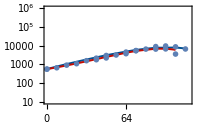
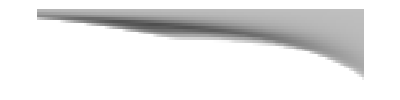
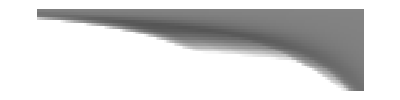
{{273092,55.3996,15.6113,0.0304305,0.00305519,0.036961,0.00616289,-103.48,18.1057,-72.7517,23.5369,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
TableOfPlots
```

```mathematica
Export[StringJoin["BarcodeDATA",ToString[TableOfData[[1]][[1]]],"-",ToString[TableOfData[[Length[TableOfData]]][[1]]],".CSV"],TableOfData,"CSV"];
```

```mathematica
Export["ExamplePosteriorSurfacePlot.pdf",TableForm[TableOfPlots, TableHeadings->{{},{"BC","Log(Pr[b]/Pr[n])_2M3","Log(Pr[b]/Pr[n])_4M3","s_2M3","δs_2M3","s_4M3","δs_4M3","τ_2M3","δτ_2M3", "τ_4M3","δτ_4M3", "Trajectory Plots", "Posterior Plot_2M3","Posterior Plot_4M3"}}],"AllowRasterization"-> True, ImageSize -> 300, ImageResolution -> 500];
```

### Uniting the data into one large table of adaptive lineages

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/AllProcessedBarcodeData"];

FilesToImport=FileNames[][[2;;434]]
```

{BarcodeDATA100003-100754.CSV,BarcodeDATA100760-101559.CSV,BarcodeDATA101560-102365.CSV,BarcodeDATA102370-103197.CSV,BarcodeDATA103198-103949.CSV,BarcodeDATA10355-10964.CSV,BarcodeDATA103951-104699.CSV,BarcodeDATA104700-105594.CSV,BarcodeDATA105595-106462.CSV,BarcodeDATA106466-107262.CSV,BarcodeDATA107264-107992.CSV,BarcodeDATA107997-108798.CSV,BarcodeDATA108799-109535.CSV,BarcodeDATA109538-110285.CSV,BarcodeDATA10966-11572.CSV,BarcodeDATA110286-111033.CSV,BarcodeDATA111035-111862.CSV,BarcodeDATA111865-112684.CSV,BarcodeDATA112685-113410.CSV,BarcodeDATA113418-114257.CSV,BarcodeDATA114264-114999.CSV,BarcodeDATA115000-115761.CSV,BarcodeDATA115764-116619.CSV,BarcodeDATA11578-12271.CSV,BarcodeDATA116623-117445.CSV,BarcodeDATA117448-118158.CSV,BarcodeDATA118159-118898.CSV,BarcodeDATA1184-1715.CSV,BarcodeDATA118899-119651.CSV,BarcodeDATA119656-120444.CSV,BarcodeDATA120445-121217.CSV,BarcodeDATA121227-122053.CSV,BarcodeDATA122055-122881.CSV,BarcodeDATA12272-12899.CSV,BarcodeDATA122885-123827.CSV,BarcodeDATA123828-124584.CSV,BarcodeDATA124588-125355.CSV,BarcodeDATA125361-126197.CSV,BarcodeDATA126199-126976.CSV,BarcodeDATA126978-127703.CSV,BarcodeDATA127705-128443.CSV,BarcodeDATA128446-129304.CSV,BarcodeDATA12903-13520.CSV,BarcodeDATA129322-130150.CSV,BarcodeDATA130160-131097.CSV,BarcodeDATA131100-131926.CSV,BarcodeDATA131929-132708.CSV,BarcodeDATA132712-133552.CSV,BarcodeDATA133558-134308.CSV,BarcodeDATA134311-135127.CSV,BarcodeDATA135128-135908.CSV,BarcodeDATA13522-14135.CSV,BarcodeDATA135912-136744.CSV,BarcodeDATA136752-137561.CSV,BarcodeDATA137572-138394.CSV,BarcodeDATA138395-139192.CSV,BarcodeDATA139198-140087.CSV,BarcodeDATA140092-140918.CSV,BarcodeDATA140920-141847.CSV,BarcodeDATA14136-14761.CSV,BarcodeDATA141850-142614.CSV,BarcodeDATA142615-143466.CSV,BarcodeDATA143467-144364.CSV,BarcodeDATA144371-145284.CSV,BarcodeDATA145286-146115.CSV,BarcodeDATA146117-146988.CSV,BarcodeDATA146990-147893.CSV,BarcodeDATA14768-15417.CSV,BarcodeDATA147899-148745.CSV,BarcodeDATA148750-149573.CSV,BarcodeDATA149581-150404.CSV,BarcodeDATA150406-151265.CSV,BarcodeDATA151274-152097.CSV,BarcodeDATA152099-152936.CSV,BarcodeDATA152944-153796.CSV,BarcodeDATA153797-154665.CSV,BarcodeDATA15418-16002.CSV,BarcodeDATA154671-155540.CSV,BarcodeDATA155541-156480.CSV,BarcodeDATA156481-157379.CSV,BarcodeDATA157382-158194.CSV,BarcodeDATA158198-159088.CSV,BarcodeDATA159091-160015.CSV,BarcodeDATA160019-160871.CSV,BarcodeDATA16003-16615.CSV,BarcodeDATA160872-161804.CSV,BarcodeDATA1-608.CSV,BarcodeDATA161808-162717.CSV,BarcodeDATA162728-163558.CSV,BarcodeDATA163562-164522.CSV,BarcodeDATA164524-165398.CSV,BarcodeDATA165399-166324.CSV,BarcodeDATA16616-17330.CSV,BarcodeDATA166327-167159.CSV,BarcodeDATA167170-168069.CSV,BarcodeDATA168070-168947.CSV,BarcodeDATA168952-169850.CSV,BarcodeDATA169854-170717.CSV,BarcodeDATA170718-171556.CSV,BarcodeDATA171558-172470.CSV,BarcodeDATA1717-2315.CSV,BarcodeDATA172472-173411.CSV,BarcodeDATA17331-17919.CSV,BarcodeDATA173412-174305.CSV,BarcodeDATA174310-175155.CSV,BarcodeDATA175158-176075.CSV,BarcodeDATA176080-176980.CSV,BarcodeDATA176981-177948.CSV,BarcodeDATA177949-178857.CSV,BarcodeDATA178866-179834.CSV,BarcodeDATA17921-18554.CSV,BarcodeDATA179837-180764.CSV,BarcodeDATA180769-181705.CSV,BarcodeDATA181711-182574.CSV,BarcodeDATA182583-183487.CSV,BarcodeDATA183491-184394.CSV,BarcodeDATA184396-185349.CSV,BarcodeDATA185353-186247.CSV,BarcodeDATA18556-19187.CSV,BarcodeDATA186248-187046.CSV,BarcodeDATA187047-188020.CSV,BarcodeDATA188024-188973.CSV,BarcodeDATA188980-189926.CSV,BarcodeDATA189928-190862.CSV,BarcodeDATA190863-191856.CSV,BarcodeDATA191857-192725.CSV,BarcodeDATA19189-19819.CSV,BarcodeDATA192730-193709.CSV,BarcodeDATA193711-194621.CSV,BarcodeDATA194622-195560.CSV,BarcodeDATA195563-196475.CSV,BarcodeDATA196476-197439.CSV,BarcodeDATA197443-198490.CSV,BarcodeDATA19820-20444.CSV,BarcodeDATA198496-199505.CSV,BarcodeDATA199506-199999.CSV,BarcodeDATA200002-201005.CSV,BarcodeDATA201006-201925.CSV,BarcodeDATA201926-202812.CSV,BarcodeDATA202814-203679.CSV,BarcodeDATA203682-204565.CSV,BarcodeDATA20445-21085.CSV,BarcodeDATA204567-205544.CSV,BarcodeDATA205545-206475.CSV,BarcodeDATA206480-207518.CSV,BarcodeDATA207522-208509.CSV,BarcodeDATA208512-209517.CSV,BarcodeDATA209518-210544.CSV,BarcodeDATA210547-211532.CSV,BarcodeDATA21086-21727.CSV,BarcodeDATA211534-212550.CSV,BarcodeDATA212555-213457.CSV,BarcodeDATA213460-214506.CSV,BarcodeDATA214508-215482.CSV,BarcodeDATA215486-216489.CSV,BarcodeDATA216493-217425.CSV,BarcodeDATA21729-22394.CSV,BarcodeDATA217430-218397.CSV,BarcodeDATA218402-219408.CSV,BarcodeDATA219411-220355.CSV,BarcodeDATA220359-221449.CSV,BarcodeDATA221468-222454.CSV,BarcodeDATA222464-223513.CSV,BarcodeDATA223519-224557.CSV,BarcodeDATA22400-23097.CSV,BarcodeDATA224564-225558.CSV,BarcodeDATA225559-226598.CSV,BarcodeDATA226600-227619.CSV,BarcodeDATA227627-228622.CSV,BarcodeDATA228624-229663.CSV,BarcodeDATA229665-230723.CSV,BarcodeDATA230725-231868.CSV,BarcodeDATA23098-23782.CSV,BarcodeDATA2316-2898.CSV,BarcodeDATA231870-232934.CSV,BarcodeDATA232938-234061.CSV,BarcodeDATA234062-235062.CSV,BarcodeDATA235063-236078.CSV,BarcodeDATA236080-237170.CSV,BarcodeDATA237172-238241.CSV,BarcodeDATA23789-24481.CSV,BarcodeDATA238245-239320.CSV,BarcodeDATA239322-240236.CSV,BarcodeDATA240241-241375.CSV,BarcodeDATA241377-242462.CSV,BarcodeDATA242463-243479.CSV,BarcodeDATA243488-244647.CSV,BarcodeDATA244649-245744.CSV,BarcodeDATA24483-25095.CSV,BarcodeDATA245746-246809.CSV,BarcodeDATA246813-247842.CSV,BarcodeDATA247846-249092.CSV,BarcodeDATA249108-250195.CSV,BarcodeDATA250206-251233.CSV,BarcodeDATA25096-25733.CSV,BarcodeDATA251234-252333.CSV,BarcodeDATA252348-253406.CSV,BarcodeDATA253410-254557.CSV,BarcodeDATA254562-255618.CSV,BarcodeDATA255620-256738.CSV,BarcodeDATA256746-257867.CSV,BarcodeDATA25744-26367.CSV,BarcodeDATA257870-259132.CSV,BarcodeDATA259142-260293.CSV,BarcodeDATA260300-261434.CSV,BarcodeDATA261441-262451.CSV,BarcodeDATA262453-263550.CSV,BarcodeDATA263552-264671.CSV,BarcodeDATA26370-27059.CSV,BarcodeDATA264678-265793.CSV,BarcodeDATA265805-266821.CSV,BarcodeDATA266824-267998.CSV,BarcodeDATA267999-269202.CSV,BarcodeDATA269203-270434.CSV,BarcodeDATA270438-271563.CSV,BarcodeDATA27064-27778.CSV,BarcodeDATA271566-272819.CSV,BarcodeDATA272822-274071.CSV,BarcodeDATA274073-275302.CSV,BarcodeDATA275309-276421.CSV,BarcodeDATA276430-277475.CSV,BarcodeDATA277477-278562.CSV,BarcodeDATA27779-28460.CSV,BarcodeDATA278568-279723.CSV,BarcodeDATA279725-280838.CSV,BarcodeDATA280839-282167.CSV,BarcodeDATA282171-283368.CSV,BarcodeDATA283375-284583.CSV,BarcodeDATA284584-285754.CSV,BarcodeDATA28462-29129.CSV,BarcodeDATA285757-287084.CSV,BarcodeDATA287090-288455.CSV,BarcodeDATA288456-289740.CSV,BarcodeDATA289742-291155.CSV,BarcodeDATA2902-3493.CSV,BarcodeDATA291158-292600.CSV,BarcodeDATA29133-29759.CSV,BarcodeDATA292600-293850.CSV,BarcodeDATA293857-295139.CSV,BarcodeDATA295142-296440.CSV,BarcodeDATA296447-297696.CSV,BarcodeDATA29761-30393.CSV,BarcodeDATA297710-298967.CSV,BarcodeDATA298971-300327.CSV,BarcodeDATA300332-301715.CSV,BarcodeDATA301717-303115.CSV,BarcodeDATA303124-304437.CSV,BarcodeDATA30395-31023.CSV,BarcodeDATA304445-305793.CSV,BarcodeDATA305795-307150.CSV,BarcodeDATA307162-308575.CSV,BarcodeDATA308583-309883.CSV,BarcodeDATA309889-311146.CSV,BarcodeDATA31026-31690.CSV,BarcodeDATA311149-312471.CSV,BarcodeDATA312472-313933.CSV,BarcodeDATA313935-315329.CSV,BarcodeDATA315334-316700.CSV,BarcodeDATA316704-317974.CSV,BarcodeDATA31691-32437.CSV,BarcodeDATA317976-319532.CSV,BarcodeDATA319534-320967.CSV,BarcodeDATA320986-322438.CSV,BarcodeDATA322443-323737.CSV,BarcodeDATA323759-325065.CSV,BarcodeDATA32439-33130.CSV,BarcodeDATA325067-326505.CSV,BarcodeDATA326508-327971.CSV,BarcodeDATA327998-329454.CSV,BarcodeDATA329457-330823.CSV,BarcodeDATA330829-332441.CSV,BarcodeDATA33136-33851.CSV,BarcodeDATA332445-334006.CSV,BarcodeDATA334015-335507.CSV,BarcodeDATA335524-336999.CSV,BarcodeDATA337000-338632.CSV,BarcodeDATA33853-34483.CSV,BarcodeDATA338639-340262.CSV,BarcodeDATA340264-341892.CSV,BarcodeDATA341900-343415.CSV,BarcodeDATA343418-344932.CSV,BarcodeDATA34488-35168.CSV,BarcodeDATA344941-346317.CSV,BarcodeDATA346324-347954.CSV,BarcodeDATA347959-349436.CSV,BarcodeDATA349439-351151.CSV,BarcodeDATA3494-4097.CSV,BarcodeDATA351157-352971.CSV,BarcodeDATA35169-35853.CSV,BarcodeDATA352977-354581.CSV,BarcodeDATA354585-356480.CSV,BarcodeDATA356485-358061.CSV,BarcodeDATA358063-359816.CSV,BarcodeDATA35857-36619.CSV,BarcodeDATA359821-361614.CSV,BarcodeDATA361616-363340.CSV,BarcodeDATA363344-365011.CSV,BarcodeDATA365025-366911.CSV,BarcodeDATA36625-37275.CSV,BarcodeDATA366914-368691.CSV,BarcodeDATA368703-370636.CSV,BarcodeDATA370637-372399.CSV,BarcodeDATA372405-374489.CSV,BarcodeDATA37276-37890.CSV,BarcodeDATA374490-376478.CSV,BarcodeDATA376480-378507.CSV,BarcodeDATA378513-380453.CSV,BarcodeDATA37893-38571.CSV,BarcodeDATA380475-382440.CSV,BarcodeDATA382446-384409.CSV,BarcodeDATA384421-386405.CSV,BarcodeDATA38573-39249.CSV,BarcodeDATA386407-388406.CSV,BarcodeDATA388416-390693.CSV,BarcodeDATA390695-392953.CSV,BarcodeDATA39250-39875.CSV,BarcodeDATA392955-395222.CSV,BarcodeDATA395241-397287.CSV,BarcodeDATA397290-399283.CSV,BarcodeDATA39877-40551.CSV,BarcodeDATA399299-399996.CSV,BarcodeDATA400005-402265.CSV,BarcodeDATA402276-404759.CSV,BarcodeDATA404766-407359.CSV,BarcodeDATA40552-41217.CSV,BarcodeDATA407360-410056.CSV,BarcodeDATA4100-4776.CSV,BarcodeDATA410061-412628.CSV,BarcodeDATA41221-41867.CSV,BarcodeDATA412632-415631.CSV,BarcodeDATA415632-418422.CSV,BarcodeDATA418425-421395.CSV,BarcodeDATA41869-42549.CSV,BarcodeDATA421410-424034.CSV,BarcodeDATA424041-426666.CSV,BarcodeDATA42553-43241.CSV,BarcodeDATA426684-429832.CSV,BarcodeDATA429843-433051.CSV,BarcodeDATA43251-43972.CSV,BarcodeDATA433052-436920.CSV,BarcodeDATA436922-440745.CSV,BarcodeDATA43973-44613.CSV,BarcodeDATA440764-445358.CSV,BarcodeDATA445394-449991.CSV,BarcodeDATA44614-45313.CSV,BarcodeDATA450007-455882.CSV,BarcodeDATA45314-45988.CSV,BarcodeDATA455929-462437.CSV,BarcodeDATA45989-46667.CSV,BarcodeDATA462478-472962.CSV,BarcodeDATA46674-47410.CSV,BarcodeDATA472991-494005.CSV,BarcodeDATA47411-48113.CSV,BarcodeDATA4777-5403.CSV,BarcodeDATA48127-48792.CSV,BarcodeDATA48793-49472.CSV,BarcodeDATA49473-50201.CSV,BarcodeDATA50204-50857.CSV,BarcodeDATA50859-51553.CSV,BarcodeDATA51556-52310.CSV,BarcodeDATA52311-52974.CSV,BarcodeDATA52975-53637.CSV,BarcodeDATA53642-54323.CSV,BarcodeDATA5404-5988.CSV,BarcodeDATA54333-54978.CSV,BarcodeDATA54979-55703.CSV,BarcodeDATA55706-56439.CSV,BarcodeDATA56443-57209.CSV,BarcodeDATA57210-57943.CSV,BarcodeDATA57947-58659.CSV,BarcodeDATA58661-59380.CSV,BarcodeDATA59381-60027.CSV,BarcodeDATA5990-6599.CSV,BarcodeDATA60028-60754.CSV,BarcodeDATA60755-61454.CSV,BarcodeDATA611-1182.CSV,BarcodeDATA61466-62194.CSV,BarcodeDATA62208-62924.CSV,BarcodeDATA62932-63637.CSV,BarcodeDATA63639-64346.CSV,BarcodeDATA64349-65066.CSV,BarcodeDATA65071-65781.CSV,BarcodeDATA65783-66602.CSV,BarcodeDATA6602-7246.CSV,BarcodeDATA66604-67352.CSV,BarcodeDATA67353-68154.CSV,BarcodeDATA68159-68886.CSV,BarcodeDATA68890-69600.CSV,BarcodeDATA69601-70302.CSV,BarcodeDATA70303-70976.CSV,BarcodeDATA70982-71731.CSV,BarcodeDATA71732-72526.CSV,BarcodeDATA7247-7861.CSV,BarcodeDATA72528-73296.CSV,BarcodeDATA73302-74041.CSV,BarcodeDATA74043-74863.CSV,BarcodeDATA74865-75579.CSV,BarcodeDATA75585-76314.CSV,BarcodeDATA76316-77016.CSV,BarcodeDATA77017-77799.CSV,BarcodeDATA77802-78481.CSV,BarcodeDATA78482-79227.CSV,BarcodeDATA7865-8481.CSV,BarcodeDATA79229-79994.CSV,BarcodeDATA79999-80711.CSV,BarcodeDATA80712-81482.CSV,BarcodeDATA81483-82248.CSV,BarcodeDATA82250-83065.CSV,BarcodeDATA83067-83773.CSV,BarcodeDATA83774-84554.CSV,BarcodeDATA84557-85319.CSV,BarcodeDATA8485-9114.CSV,BarcodeDATA85321-86092.CSV,BarcodeDATA86094-86820.CSV,BarcodeDATA86823-87562.CSV,BarcodeDATA87571-88292.CSV,BarcodeDATA88296-89059.CSV,BarcodeDATA89061-89859.CSV,BarcodeDATA89861-90658.CSV,BarcodeDATA90659-91446.CSV,BarcodeDATA9115-9739.CSV,BarcodeDATA91447-92198.CSV,BarcodeDATA92201-92976.CSV,BarcodeDATA92979-93777.CSV,BarcodeDATA93779-94518.CSV,BarcodeDATA94520-95301.CSV,BarcodeDATA95303-96067.CSV,BarcodeDATA96070-96869.CSV,BarcodeDATA96870-97725.CSV,BarcodeDATA9744-10349.CSV,BarcodeDATA97729-98516.CSV,BarcodeDATA98518-99296.CSV,BarcodeDATA99297-99999.CSV}

```mathematica
Do[TableOfDat[i]=ToExpression[Import[FilesToImport[[i]]]], {i, 1, Length[FilesToImport]}];
```

```mathematica
UnitedData=Sort[Join[Flatten[Table[TableOfDat[i], {i, 1, Length[FilesToImport]}],1]], #1[[1]]<#2[[1]]&];


Export["AdaptiveLineagesE1&E2.csv",UnitedData,"CSV"]
```

AdaptiveLineagesE1&E2.csv

## 5. MeanFitness comparison

Infer the mean fitness by adding up contribution of each lineage uring teh inferred (s, τ) while accounting for the eventual decline of some lineages using InterpolatedUnadaptiveFraction.

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/AllProcessedBarcodeData_Carbon"];
AllAdaptiveLineages=ToExpression[Import["AdaptiveLineagesE1&E2.csv"]];
```

```mathematica
TableForm[AllAdaptiveLineages[[1;;20]], TableHeadings->{{},{"BC","Log(Pr[b]/Pr[n])_1","Log(Pr[b]/Pr[n])_2","s_1","δs_1","s_2","δs_2","τ_1","δτ_1", "τ_2","δτ_2"}}]
```

| BC | Log(Pr[b]/Pr[n])_1 | Log(Pr[b]/Pr[n])_2 | s_1 | δs_1 | s_2 | δs_2 | τ_1 | δτ_1 | τ_2 | δτ_2
 | 1 | -10.3503 | 437.533 | 0.00001 | 0.01 | 0.0874863 | 0.00324045 | 0 | 5 | -10.7233 | 3.50301
 | 2 | -8.94149 | -9.62843 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 3 | -6.31793 | -9.7379 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 7 | -6.18343 | -8.93869 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 14 | -6.51442 | -8.40835 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 15 | 6150.88 | -5.8308 | 0.103664 | 0.00111082 | 0.00001 | 0.01 | 0.800242 | 1.08688 | 0 | 5
 | 16 | -7.31047 | -9.49237 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 17 | -4.87625 | -8.63283 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 18 | -10.1805 | -9.32023 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 23 | -10.387 | -10.0314 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 25 | 35.8729 | 53.4893 | 0.0320317 | 0.00389843 | 0.0441855 | 0.00489694 | -88.3419 | 20.7353 | -66.5693 | 15.5798
 | 26 | -11.5497 | -11.3295 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 31 | -8.94454 | -9.95944 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 32 | 4804.87 | -9.82457 | 0.106252 | 0.00125173 | 0.00001 | 0.01 | 5.88589 | 1.1374 | 0 | 5
 | 33 | 0.931429 | -5.82122 | 0.0308673 | 0.00855509 | 0.00001 | 0.01 | -67.3532 | 43.0152 | 0 | 5
 | 34 | -8.73268 | -10.0516 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 35 | -9.89479 | -4.51869 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 36 | 9.77161 | 2.36768 | 0.0280161 | 0.00569951 | 0.0322031 | 0.00991143 | -99.2854 | 37.263 | -90.7373 | 50.1489
 | 37 | -7.62162 | -9.68673 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 38 | -10.2606 | -10.5248 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/2M3"];
xBarKappa2M3=ToExpression[Import["InferredxBArAndKappa2M3.csv"]];
TimePoints2M3={0,16,32, 40, 48, 64, 72, 80, 88, 96, 104, 112};
MeanFitnessList2M3=Table[{TimePoints2M3[[i+1]], xBarKappa2M3[[i]][[1]]},{i, 1, Length[xBarKappa2M3]}];
KappaList2M3=Table[{TimePoints2M3[[i+1]], xBarKappa2M3[[i]][[2]]},{i, 1, Length[xBarKappa2M3]}];

SetDirectory["~/Dropbox/BayesianAnalysis/4M3"];
xBarKappa4M3=ToExpression[Import["InferredxBArAndKappa4M3.csv"]];
TimePoints4M3={0,8,24, 40, 48,56, 64, 72,88, 96};
MeanFitnessList4M3=Table[{TimePoints4M3[[i+1]], xBarKappa4M3[[i]][[1]]},{i, 1, Length[xBarKappa4M3]}];
KappaList4M3=Table[{TimePoints4M3[[i+1]], xBarKappa4M3[[i]][[2]]},{i, 1, Length[xBarKappa4M3]}];
```

```mathematica
Adaptive2M3=DeleteDuplicates[Select[AllAdaptiveLineages, #[[2]]>3 &]];
Adaptive4M3=Select[AllAdaptiveLineages, #[[3]]>0 &&#[[6]]<0.16 &];
```

```mathematica
Length[Adaptive2M3]
Length[Adaptive4M3]
```

28771

16359

Infer the mean fitness by adding up contribution of each lineage uring teh inferred (s, τ) while accounting for the eventual decline of some lineages using InterpolatedUnadaptiveFraction.

```mathematica
PopSize=5*10^8;
MeanF[0]=0;
UnadaptedFrac=1;
Do[
MeanF[j]=1/PopSize Sum[Exp[Adaptive2M3[[i]][[4]](j-Adaptive2M3[[i]][[8]])]*UnadaptedFrac,{i, 1, Length[Adaptive2M3]}];
UnadaptedFrac=UnadaptedFrac*Exp[-MeanF[j]];
(*Print[MeanF[j]];*)
j=j+1;, {j, 1, 130}];
MeanFit=Table[{i, MeanF[i]}, {i, 0, 130}];
Export["MeanFitnessFromBeneficials2M3.csv",MeanFit,"CSV"]
```

MeanFitnessFromBeneficials2M3.csv

```mathematica
PopSize=5*10^8;
MeanF[0]=0;
UnadaptedFrac=1;
Do[
MeanF[j]=1/PopSize Sum[Exp[Adaptive4M3[[i]][[6]](j-Adaptive4M3[[i]][[10]])]*UnadaptedFrac,{i, 1, Length[Adaptive4M3]}];
UnadaptedFrac=UnadaptedFrac*Exp[-MeanF[j]];
(*Print[MeanF[j]];*)
j=j+1;, {j, 1, 132}];
MeanFit=Table[{i, MeanF[i]}, {i, 0, 132}];
Export["MeanFitnessFromBeneficials4M3.csv",MeanFit,"CSV"]
```

MeanFitnessFromBeneficials4M3.csv

```mathematica
MeanFit2M3=ToExpression[Import["MeanFitnessFromBeneficials2M3.csv"]];
MeanFit4M3=ToExpression[Import["MeanFitnessFromBeneficials4M3.csv"]];
```

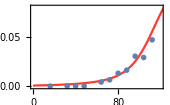

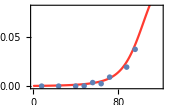

```mathematica
MeanFitnessCompare2M3=Show[{ListPlot[MeanFit2M3, PlotStyle -> c2, Joined -> True, PlotRange -> All],ListPlot[MeanFitnessList2M3, PlotMarkers -> Markers[0.02, c8, Thickness[0.005]]]}, ImageSize -> 170,Frame -> True,FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Mean Fitness", FontFamily-> "Helvetica", 10]]}, PlotRange -> {{0,120},{-0.001, 0.08}}]

MeanFitnessCompare4M3=Show[{ListPlot[MeanFit4M3, PlotStyle -> c2, Joined -> True, PlotRange -> All],ListPlot[MeanFitnessList4M3, PlotMarkers -> Markers[0.02, c8, Thickness[0.005]]]}, ImageSize -> 170,Frame -> True,FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Mean Fitness", FontFamily-> "Helvetica", 10]]}, PlotRange ->{{0,120}, {-0.001, 0.08}}]
```

```mathematica
UpperMeanFitness4M3=Delete[Table[{t,10^-5.2/0.062(Exp[ 0.067t]-1)},{t, 1, 120}],1];
LowerMeanFitness4M3=Delete[Table[{t,10^-5.3/0.062(Exp[ 0.058t]-1)},{t, 1,120}],1];
MeanFitnessBounds=ListPlot[{UpperMeanFitness4M3, LowerMeanFitness4M3},PlotStyle -> Gray,Filling -> 1-> {{2}, RGBColor[0.6,0.6,0.6,0.3]},ImageSize -> 250,Frame -> True,Joined -> True,FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Mean Fitness", FontFamily-> "Helvetica", 10]]}, PlotRange ->{{0,120}, {-0.001, 0.08}}];
```

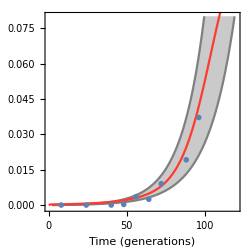

MeanFitnessWithBounds.pdf

```mathematica
MeanFitnessWithBounds=Show[{MeanFitnessBounds,MeanFitnessCompare4M3},PlotRange ->{{0,120}, {-0.001, 0.08}}, AspectRatio->1]
Export["MeanFitnessWithBounds.pdf",MeanFitnessWithBounds,"PDF"]
```

```mathematica
Export["MeanFitnessFromNeutralsE1.csv",MeanFitnessList2M3,"CSV"]
Export["MeanFitnessFromNeutralsE2.csv",MeanFitnessList4M3,"CSV"]
```

MeanFitnessFromNeutralsE1.csv

MeanFitnessFromNeutralsE2.csv

Comparison shows that we must be capturing all that matters to the mean fitness.

```mathematica
Export["MeanFitnessCompare2M3.eps",MeanFitnessCompare2M3,"EPS"]
Export["MeanFitnessCompare4M3.eps",MeanFitnessCompare4M3,"EPS"]
```

MeanFitnessCompare2M3.eps

MeanFitnessCompare4M3.eps

## 6. Plots of trajectories

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/2M3"];
AllAdaptiveLineages=ToExpression[Import["AdaptiveLineagesExperiment.csv"]];
```

```mathematica
TableForm[AllAdaptiveLineages[[1;;20]], TableHeadings->{{},{"BC","Log(Pr[b]/Pr[n])_1","Log(Pr[b]/Pr[n])_2","s_1","δs_1","s_2","δs_2","τ_1","δτ_1", "τ_2","δτ_2"}}]
```

| BC | Log(Pr[b]/Pr[n])_1 | Log(Pr[b]/Pr[n])_2 | s_1 | δs_1 | s_2 | δs_2 | τ_1 | δτ_1 | τ_2 | δτ_2
 | 1 | -10.3503 | 437.533 | 0.00001 | 0.01 | 0.0874863 | 0.00324045 | 0 | 5 | -10.7233 | 3.50301
 | 2 | -8.94149 | -9.62843 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 3 | -6.31793 | -9.7379 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 7 | -6.18343 | -8.93869 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 14 | -6.51442 | -8.40835 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 15 | 6150.88 | -5.8308 | 0.103664 | 0.00111082 | 0.00001 | 0.01 | 0.800242 | 1.08688 | 0 | 5
 | 16 | -7.31047 | -9.49237 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 17 | -4.87625 | -8.63283 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 18 | -10.1805 | -9.32023 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 23 | -10.387 | -10.0314 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 25 | 35.8729 | 53.4893 | 0.0320317 | 0.00389843 | 0.0441855 | 0.00489694 | -88.3419 | 20.7353 | -66.5693 | 15.5798
 | 26 | -11.5497 | -11.3295 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 31 | -8.94454 | -9.95944 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 32 | 4804.87 | -9.82457 | 0.106252 | 0.00125173 | 0.00001 | 0.01 | 5.88589 | 1.1374 | 0 | 5
 | 33 | 0.931429 | -5.82122 | 0.0308673 | 0.00855509 | 0.00001 | 0.01 | -67.3532 | 43.0152 | 0 | 5
 | 34 | -8.73268 | -10.0516 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 35 | -9.89479 | -4.51869 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 36 | 9.77161 | 2.36768 | 0.0280161 | 0.00569951 | 0.0322031 | 0.00991143 | -99.2854 | 37.263 | -90.7373 | 50.1489
 | 37 | -7.62162 | -9.68673 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 38 | -10.2606 | -10.5248 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/2M3"];
CellNumberTrajectories2M3=ToExpression[Import["CellNumberTrajectories2M3.csv"]];

SetDirectory["~/Dropbox/BayesianAnalysis/4M3"];
CellNumberTrajectories4M3=ToExpression[Import["CellNumberTrajectories4M3.csv"]];
```

```mathematica
PlotOfTrajectory2M3[bc_]:=Module[{bcData, bcProbBene1, bcFitness1},
If[MemberQ[Map[First,AllAdaptiveLineages],bc],
bcData=Select[AllAdaptiveLineages, #[[1]]==bc&][[1]];
bcProbBene1=bcData[[2]];
bcFitness1=bcData[[4]];, bcProbBene1=-19.0;bcFitness1=0.0;];
ListLogPlot[CellNumberTrajectories2M3[[bc]], Joined -> True, PlotStyle -> {{Scheme3[(bcFitness1/0.13)], Thickness[0.0004]}}(*{{Scheme3[Clip[Log[bcProbBene1+20]/5, {0,1}]], Thickness[0.0004(1+bcFitness1)]}}*),ImageSize ->400, PlotRange -> {{0, 168},{0.03, 5*10^8}}, Frame -> True,FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Number of cells", FontFamily-> "Helvetica", 10]]}, FrameTicks->{{Prepend[Table[{10^k, Superscript[10,k]},{k, 0, 8}], {0.1, "Extinct"}], None}, {Table[{16k, 16k}, {k, 0, 25}],None}}]]


PlotOfTrajectory4M3[bc_]:=Module[{bcData, bcProbBene1, bcFitness1},
If[MemberQ[Map[First,AllAdaptiveLineages],bc],
bcData=Select[AllAdaptiveLineages, #[[1]]==bc&][[1]];
bcProbBene1=bcData[[3]];
bcFitness1=bcData[[6]];, bcProbBene1=-19.0;bcFitness1=0.0;];
ListLogPlot[CellNumberTrajectories4M3[[bc]], Joined -> True, PlotStyle -> {{Scheme3[(bcFitness1/0.13)], Thickness[0.0004]}}(*{{Scheme3[Clip[Log[bcProbBene1+20]/5, {0,1}]], Thickness[0.0004(1+bcFitness1)]}}*),ImageSize ->400, PlotRange -> {{0, 168},{0.03, 5*10^8}}, Frame -> True,FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Number of cells", FontFamily-> "Helvetica", 10]]}, FrameTicks->{{Prepend[Table[{10^k, Superscript[10,k]},{k, 0, 8}], {0.1, "Extinct"}], None}, {Table[{16k, 16k}, {k, 0, 25}],None}}]]
```

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/2M3"];
AdaptiveBarcodes2M3=Map[First,Sort[Select[AllAdaptiveLineages, (#[[2]]>30&& #[[4]]>0.05)&], #1[[4]]>#2[[4]]&]][[1;;1000]];
BorderLineBarcodes2M3=RandomSample[Map[First,Select[AllAdaptiveLineages, 1<#[[2]]<30& ]], 500];
NeutralBarcodes2M3=Map[First,Sort[AllAdaptiveLineages, #1[[4]]<#2[[4]]& ][[1;;500]]];
ExtinctBarcodes2M3=Map[First,ToExpression[Import["ExtinctLineages2M3.csv"]]][[1;;500]];

SetDirectory["~/Dropbox/BayesianAnalysis/4M3"];
AdaptiveBarcodes4M3=Map[First,Sort[Select[AllAdaptiveLineages, (#[[3]]>30&& #[[6]]>0.05)&], #1[[6]]>#2[[6]]&]][[1;;1000]];
BorderLineBarcodes4M3=RandomSample[Map[First,Select[AllAdaptiveLineages, -3<#[[3]]<26& ]], 500];
NeutralBarcodes4M3=Map[First,Sort[AllAdaptiveLineages, #1[[6]]<#2[[6]]& ][[1;;500]]];
ExtinctBarcodes4M3=Map[First,ToExpression[Import["ExtinctLineages4M3.csv"]]][[1;;500]];
```

```mathematica
BarcodesToPlot2M3=RandomSample[Join[AdaptiveBarcodes2M3,BorderLineBarcodes2M3, NeutralBarcodes2M3, ExtinctBarcodes2M3], Length[AdaptiveBarcodes2M3]+Length[NeutralBarcodes2M3]+Length[BorderLineBarcodes2M3]+Length[ExtinctBarcodes2M3]];
BarcodesToPlot4M3=RandomSample[Join[AdaptiveBarcodes4M3,BorderLineBarcodes4M3, NeutralBarcodes4M3, ExtinctBarcodes4M3], Length[AdaptiveBarcodes4M3]+Length[NeutralBarcodes4M3]+Length[BorderLineBarcodes4M3]+Length[ExtinctBarcodes4M3]];
```

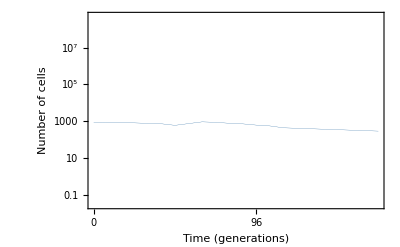

```mathematica
PlotOfTrajectory2M3[1]
```

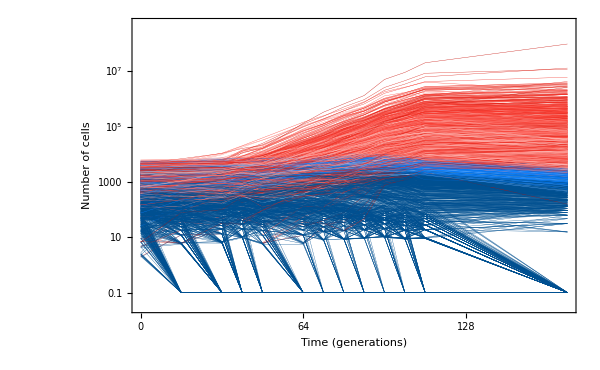
{255.67245,-Graphics-}

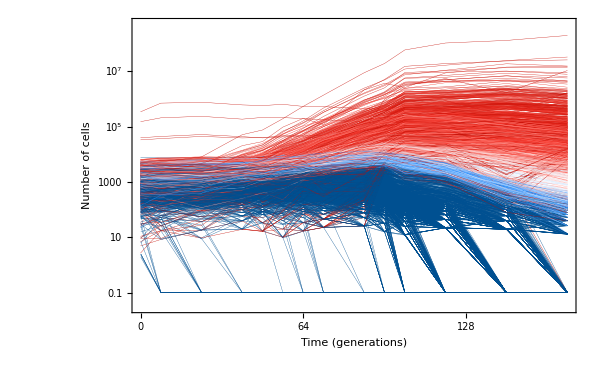
{297.03088,-Graphics-}

```mathematica
Timing[LineagesSample2M3=Show[Table[PlotOfTrajectory2M3[bc], {bc, BarcodesToPlot2M3}],ImageSize -> 600]]
Timing[LineagesSample4M3=Show[Table[PlotOfTrajectory4M3[bc], {bc, BarcodesToPlot4M3}],ImageSize -> 600]]

Speak["Finished, evaluating"];
```

```mathematica
Export["AdaptiveLineagesPlot2M3_FitnessColored.eps",LineagesSample2M3,"EPS"]
Export["AdaptiveLineagesPlot4M3_FitnessColored.eps",LineagesSample4M3,"EPS"]
```

AdaptiveLineagesPlot2M3_FitnessColored.eps

AdaptiveLineagesPlot4M3_FitnessColored.eps

```mathematica
Length[Intersection[Map[First,Adaptive2M3], Map[First,Adaptive4M3]]]
```

6384

## 7. Distribution of s, τ and μ(s)

### Importing data

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/AllProcessedBarcodeData_Carbon"];
AllAdaptiveLineages=ToExpression[Import["AdaptiveLineagesE1&E2.csv"]];
```

```mathematica
TableForm[AllAdaptiveLineages[[1;;20]], TableHeadings->{{},{"BC","Log(Pr[b]/Pr[n])_1","Log(Pr[b]/Pr[n])_2","s_1","δs_1","s_2","δs_2","τ_1","δτ_1", "τ_2","δτ_2"}}]
```

| BC | Log(Pr[b]/Pr[n])_1 | Log(Pr[b]/Pr[n])_2 | s_1 | δs_1 | s_2 | δs_2 | τ_1 | δτ_1 | τ_2 | δτ_2
 | 1 | -10.3503 | 437.533 | 0.00001 | 0.01 | 0.0874863 | 0.00324045 | 0 | 5 | -10.7233 | 3.50301
 | 2 | -8.94149 | -9.62843 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 3 | -6.31793 | -9.7379 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 7 | -6.18343 | -8.93869 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 14 | -6.51442 | -8.40835 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 15 | 6150.88 | -5.8308 | 0.103664 | 0.00111082 | 0.00001 | 0.01 | 0.800242 | 1.08688 | 0 | 5
 | 16 | -7.31047 | -9.49237 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 17 | -4.87625 | -8.63283 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 18 | -10.1805 | -9.32023 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 23 | -10.387 | -10.0314 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 25 | 35.8729 | 53.4893 | 0.0320317 | 0.00389843 | 0.0441855 | 0.00489694 | -88.3419 | 20.7353 | -66.5693 | 15.5798
 | 26 | -11.5497 | -11.3295 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 31 | -8.94454 | -9.95944 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 32 | 4804.87 | -9.82457 | 0.106252 | 0.00125173 | 0.00001 | 0.01 | 5.88589 | 1.1374 | 0 | 5
 | 33 | 0.931429 | -5.82122 | 0.0308673 | 0.00855509 | 0.00001 | 0.01 | -67.3532 | 43.0152 | 0 | 5
 | 34 | -8.73268 | -10.0516 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 35 | -9.89479 | -4.51869 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 36 | 9.77161 | 2.36768 | 0.0280161 | 0.00569951 | 0.0322031 | 0.00991143 | -99.2854 | 37.263 | -90.7373 | 50.1489
 | 37 | -7.62162 | -9.68673 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 38 | -10.2606 | -10.5248 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/2M3"];
xBarKappa2M3=ToExpression[Import["InferredxBArAndKappa2M3.csv"]];
TimePoints2M3={0,16,32, 40, 48, 64, 72, 80, 88, 96, 104, 112};
MeanFitnessList2M3=Table[{TimePoints2M3[[i+1]], xBarKappa2M3[[i]][[1]]},{i, 1, Length[xBarKappa2M3]}];
KappaList2M3=Table[{TimePoints2M3[[i+1]], xBarKappa2M3[[i]][[2]]},{i, 1, Length[xBarKappa2M3]}];

SetDirectory["~/Dropbox/BayesianAnalysis/4M3"];
xBarKappa4M3=ToExpression[Import["InferredxBArAndKappa4M3.csv"]];
TimePoints4M3={0,8,24, 40, 48,56, 64, 72,88, 96};
MeanFitnessList4M3=Table[{TimePoints4M3[[i+1]], xBarKappa4M3[[i]][[1]]},{i, 1, Length[xBarKappa4M3]}];
KappaList4M3=Table[{TimePoints4M3[[i+1]], xBarKappa4M3[[i]][[2]]},{i, 1, Length[xBarKappa4M3]}];
```

```mathematica
Adaptive2M3=Select[AllAdaptiveLineages, #[[2]]>8 &];
Adaptive4M3=Select[AllAdaptiveLineages, #[[3]]>0.1 &];
Length[Adaptive2M3]
Length[Adaptive4M3]

MeanFit2M3=ToExpression[Import["MeanFitnessFromBeneficials2M3.csv"]];
MeanFit4M3=ToExpression[Import["MeanFitnessFromBeneficials4M3.csv"]];
```

22184

16394

```mathematica
AdaptiveOnly2M3=Select[AllAdaptiveLineages, (#[[2]]>1 &&#[[3]]<0&& #[[8]]>-3/(#[[4]]))&];
AdaptiveOnly4M3=Select[AllAdaptiveLineages, (#[[3]]>1 &&#[[2]]<0 && #[[10]]>-3/(#[[6]]))&];
Print["ExclusivelyAdatpive2M3=",Length[AdaptiveOnly2M3]];
Print["ExclusivelyAdatpive4M3=",Length[AdaptiveOnly4M3]];
```

ExclusivelyAdatpive2M3=21305

ExclusivelyAdatpive4M3=5987

### s-τ plots

First make all the -150 ones not quiite all on -150. Then add the log(c)/s correction.

```mathematica
InferredSvsTau2M3=Map[If[-160<#[[1]]<-140, {#[[1]]-RandomReal[{0,10}](*+Log[3.5]/(#[[2]])*), #[[2]]}, {#[[1]]+Log[3.5]/(#[[2]]), #[[2]]}]&,Table[{Adaptive2M3[[i]][[8]],Adaptive2M3[[i]][[4]]},{i, 1, Length[Adaptive2M3]}]];
TauList2M3=Map[#[[1]]&, InferredSvsTau2M3];
SList2M3=Map[#[[2]]&, InferredSvsTau2M3];

InferredSvsTau4M3=Map[If[#[[1]]==-150., {#[[1]]-RandomReal[{0,10}]+Log[3.5]/(#[[2]]), #[[2]]}, {#[[1]]+Log[3.5]/(#[[2]]), #[[2]]}]&,Table[{Adaptive4M3[[i]][[10]],Adaptive4M3[[i]][[6]]},{i, 1, Length[Adaptive4M3]}]];
TauList4M3=Map[#[[1]]&, InferredSvsTau4M3];
SList4M3=Map[#[[2]]&, InferredSvsTau4M3];
```

```mathematica
MarkerSizes2M3[i_,t_]:=0.3*10^-4 √(Exp[Adaptive2M3[[i]][[4]]*(t-Adaptive2M3[[i]][[8]])]/(Adaptive2M3[[i]][[4]]))
MarkerSizes4M3[i_,t_]:=0.3*10^-4 √(Exp[Adaptive4M3[[i]][[6]]*(t-Adaptive4M3[[i]][[10]])]/(Adaptive4M3[[i]][[6]]))
```

Function the colors lineages based on whether they are likely pre-existing or not. 

1. If adaptive in other replicate AND establishment time earlier than -(c/s)

```mathematica
STauPlot2M3=Show[RandomSample[Table[ListPlot[{InferredSvsTau2M3[[i]]}, PlotMarkers -> Markers[(*0.003*)MarkerSizes2M3[i, 88], (*Black*)(*Scheme3[(Adaptive2M3[[i]][[3]])/(10*Log[10])]*)If[Adaptive2M3[[i]][[3]]>3 , c9,c5],Thickness[0.0003]], PlotRange -> {{-100, 112},{0.0, 0.16}}, Frame -> True,FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Fitness effect, s", FontFamily-> "Helvetica", 10]]}, FrameTicks->{{Automatic, None}, {Table[{16k, 16k}, {k, -10, 7}],None}},AxesOrigin -> {-150,0}], {i, 1, Length[Adaptive2M3]}], Length[Adaptive2M3]]];
STauPlot4M3=Show[RandomSample[Table[ListPlot[{InferredSvsTau4M3[[i]]}, PlotMarkers -> Markers[(*0.003*)MarkerSizes4M3[i, 88], (*Black*)(*Scheme3[(Adaptive4M3[[i]][[2]])/(10*Log[10])]*)If[Adaptive4M3[[i]][[2]]>3, c9,c5],Thickness[0.0003]], PlotRange -> {{-100, 112},{0.0, 0.16}}, Frame -> True,FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Fitness effect, s", FontFamily-> "Helvetica", 10]]}, FrameTicks->{{Automatic, None}, {Table[{16k, 16k}, {k, -10, 7}],None}},AxesOrigin -> {-150,0}], {i, 1, Length[Adaptive4M3]}], Length[Adaptive4M3]]];
```

```mathematica
n0=1000;

MeanFit2M3=ToExpression[Import["MeanFitnessFromBeneficials2M3.csv"]];
MeanFit4M3=ToExpression[Import["MeanFitnessFromBeneficials4M3.csv"]];

ObservableLimitTime2M3=Table[{MeanFit2M3[[i]][[1]]-(1/(MeanFit2M3[[i]][[2]])Log[n0 MeanFit2M3[[i]][[2]]]), MeanFit2M3[[i]][[2]]}, {i, 71, Length[MeanFit2M3]}];
ObservableLimitTime4M3=Table[{MeanFit4M3[[i]][[1]]-(1.07/(MeanFit4M3[[i]][[2]])Log[n0 MeanFit4M3[[i]][[2]]]), MeanFit4M3[[i]][[2]]}, {i, 71, Length[MeanFit4M3]}];

IdealLimitTime2M3=Table[{MeanFit2M3[[i]][[1]]-(2/(MeanFit2M3[[i]][[2]])), MeanFit2M3[[i]][[2]]}, {i, 71, Length[MeanFit2M3]}];
IdealLimitTime4M3=Table[{MeanFit4M3[[i]][[1]]-(2/(MeanFit4M3[[i]][[2]])), MeanFit4M3[[i]][[2]]}, {i, 71, Length[MeanFit4M3]}];
```

```mathematica
ObservableTimeLimitPlot2M3=ListPlot[ObservableLimitTime2M3, Frame -> True,PlotRange -> {{-100, 112},{0.0, 0.16}},Joined -> True,AxesOrigin -> {-150,0},FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Fitness effect, s", FontFamily-> "Helvetica", 10]]}, FrameTicks->{{Automatic, None}, {Table[{16k, 16k}, {k, -10, 7}],None}}, PlotStyle -> Directive[{Thickness[0.001],Black, Dashing[0.01]}]];
ObservableTimeLimitPlot4M3=ListPlot[ObservableLimitTime4M3, Frame -> True,PlotRange -> {{-100, 112},{0.0, 0.16}},Joined -> True,AxesOrigin -> {-150,0},FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Fitness effect, s", FontFamily-> "Helvetica", 10]]}, FrameTicks->{{Automatic, None}, {Table[{16k, 16k}, {k, -10, 7}],None}}, PlotStyle -> Directive[{Thickness[0.001],Black, Dashing[0.01]}]];

IdealTimeLimitPlot2M3=ListPlot[IdealLimitTime2M3, Frame -> True,PlotRange -> {{-100, 112},{0.0, 0.16}},Joined -> True,AxesOrigin -> {-150,0},FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Fitness effect, s", FontFamily-> "Helvetica", 10]]}, FrameTicks->{{Automatic, None}, {Table[{16k, 16k}, {k, -10, 7}],None}}, PlotStyle -> Directive[{Thickness[0.001],Black, Dashing[0.03]}]];
IdealTimeLimitPlot4M3=ListPlot[IdealLimitTime4M3, Frame -> True,PlotRange -> {{-100, 112},{0.0, 0.16}},Joined -> True,AxesOrigin -> {-150,0},FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Fitness effect, s", FontFamily-> "Helvetica", 10]]}, FrameTicks->{{Automatic, None}, {Table[{16k, 16k}, {k, -10, 7}],None}}, PlotStyle -> Directive[{Thickness[0.001],Black, Dashing[0.03]}]];
```

```mathematica
MeanFitnessPlot2M3=ListPlot[MeanFit2M3, Frame -> True,PlotRange -> {{-100, 112},{0.0, 0.16}},Joined -> True,AxesOrigin -> {-150,0},FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Fitness effect, s", FontFamily-> "Helvetica", 10]]}, FrameTicks->{{Automatic, None}, {Table[{16k, 16k}, {k, -10, 7}],None}}, PlotStyle -> Directive[{Thickness[0.001],Black}]];
MeanFitnessPlot4M3=ListPlot[MeanFit4M3, Frame -> True,PlotRange -> {{-100, 112},{0.0, 0.16}},Joined -> True,AxesOrigin -> {-150,0},FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Fitness effect, s", FontFamily-> "Helvetica", 10]]}, FrameTicks->{{Automatic, None}, {Table[{16k, 16k}, {k, -10, 7}],None}}, PlotStyle -> Directive[{Thickness[0.001],Black}]];

FitnessTauScatterPlot2M3=Show[{STauPlot2M3,MeanFitnessPlot2M3,ObservableTimeLimitPlot2M3,IdealTimeLimitPlot2M3}, ImageSize-> 400];
FitnessTauScatterPlot4M3=Show[{STauPlot4M3,MeanFitnessPlot4M3,ObservableTimeLimitPlot4M3,IdealTimeLimitPlot4M3}, ImageSize-> 400];

Export["FitnessTauScatterPlot2M3_Reverse.eps",FitnessTauScatterPlot2M3,"EPS"];
Export["FitnessTauScatterPlot4M3_Reverse.eps",FitnessTauScatterPlot4M3,"EPS"];
```

```mathematica
Speak["Finished, evaluating"]
```

```mathematica
DeltaS=0.001;

GatheredByFitness=GatherBy[SList, Round[#/DeltaS]&];

SDistribution=Table[
FitnessOfClass=DeltaS*Round[(GatheredByFitness[[k]][[1]])/DeltaS];

NumberInBin=Length[GatheredByFitness[[k]]];

{N[FitnessOfClass],NumberInBin}, {k,1, Length[GatheredByFitness]}];


DeltaTau=1;

GatheredByTau=GatherBy[TauList, Round[#/DeltaTau]&];

TauDistribution=Table[
TauOfClass=DeltaTau*Round[(GatheredByTau[[k]][[1]])/DeltaTau];

NumberInBin=Length[GatheredByTau[[k]]];

{N[TauOfClass],NumberInBin}, {k,1, Length[GatheredByTau]}];
```

```mathematica
FitnessDistribution=Show[{ListPlot[SDistribution,PlotMarkers -> Markers[0.0002, Black, Thin], PlotRange -> {{0.0, 0.14},All},Filling -> {1-> {Axis, Black}}, ImageSize->200, Ticks -> {None,{{0,0}, {3000,3000}}}, AspectRatio -> 3]/.List[x_,y_]->List[y,x]}, ImageSize -> 70]

EstablishmentTimeDistribution=ListPlot[TauDistribution,PlotMarkers -> Markers[0.0002, Black, Thin], PlotRange -> {{-80,112},All}, AxesOrigin-> {-80,0},Ticks -> {None, {{0,0},{600,600}}},Filling -> {1-> {Axis, Black}}, ImageSize->250, AspectRatio -> 0.1]
```

```mathematica
Export["S_dist.eps",FitnessDistribution,"EPS"]
Export["Tau_dist.eps",EstablishmentTimeDistribution,"EPS"]
```

S_dist.eps

Tau_dist.eps

### Fitness correlation for the pre-existing class

```mathematica
PreExisting=Select[AllAdaptiveLineages, #[[2]]>-Log[0.01]&&#[[3]]>-Log[0.01]&];
Exclusive2M3=Select[AllAdaptiveLineages, #[[2]]>-Log[0.1]&&#[[3]]<-Log[0.1]&];
```

```mathematica
Length[PreExisting]
Length[Exclusive2M3]
```

29

22209

```mathematica
PreExistingFitnessesIn2M3=Map[#[[4]]&,PreExisting];
PreExistingTauIn2M3=Map[#[[8]]&,PreExisting];

ExclusiveFitnessesIn2M3=Map[#[[4]]&,Exclusive2M3];
ExclusiveTauIn2M3=Map[#[[8]]&,Exclusive2M3];
```

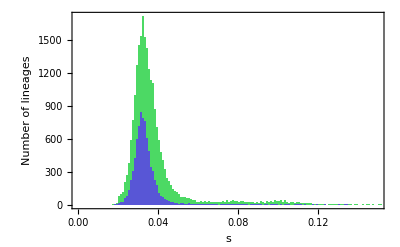

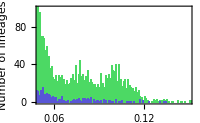

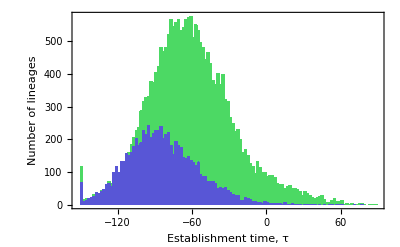

```mathematica
PreExistingS=Histogram[{PreExistingFitnessesIn2M3}, {0.001},PlotRange -> {{0, 0.15},Automatic}, AxesOrigin->{0,0}, ChartStyle->Directive[{EdgeForm[None], c9}],Frame -> True,FrameLabel -> {Text[Style["s", 12,FontFamily-> "Helvetica"]],Text[Style["Number of lineages", 12,FontFamily-> "Helvetica"]]}, FrameTicksStyle->Directive[Black,12, FontFamily-> "Helvetica"]];
ExclusiveS=Histogram[{ExclusiveFitnessesIn2M3}, {0.001},PlotRange -> {{0, 0.15},Automatic}, AxesOrigin->{0,0}, ChartStyle->Directive[{EdgeForm[None], c5}],Frame -> True,FrameLabel -> {Text[Style["s", 12,FontFamily-> "Helvetica"]],Text[Style["Number of lineages", 12,FontFamily-> "Helvetica"]]}, FrameTicksStyle->Directive[Black,12, FontFamily-> "Helvetica"]];

PreExistingS2=Histogram[{PreExistingFitnessesIn2M3}, {0.001},PlotRange -> {{0.05, 0.15},{0,100}}, AxesOrigin->{0,0}, ChartStyle->Directive[{EdgeForm[None], c9}],Frame -> True,FrameLabel -> {Text[Style["s", 12,FontFamily-> "Helvetica"]],Text[Style["Number of lineages", 12,FontFamily-> "Helvetica"]]}, FrameTicksStyle->Directive[Black,12, FontFamily-> "Helvetica"], PlotRangeClipping->True];
ExclusiveS2=Histogram[{ExclusiveFitnessesIn2M3}, {0.001},PlotRange -> {{0.05, 0.15},{0,100}}, AxesOrigin->{0,0}, ChartStyle->Directive[{EdgeForm[None], c5}],Frame -> True,FrameLabel -> {Text[Style["s", 12,FontFamily-> "Helvetica"]],Text[Style["Number of lineages", 12,FontFamily-> "Helvetica"]]}, FrameTicksStyle->Directive[Black,12, FontFamily-> "Helvetica"],PlotRangeClipping->True];

PreExistingTau=Histogram[PreExistingTauIn2M3, {2}, AxesOrigin->{0,0}, ChartStyle->Directive[{EdgeForm[None], c9}],Frame -> True,FrameLabel -> {Text[Style["Establishment time, τ", 12,FontFamily-> "Helvetica"]],Text[Style["Number of lineages", 12,FontFamily-> "Helvetica"]]}, FrameTicksStyle->Directive[Black,12, FontFamily-> "Helvetica"]];
ExclusiveTau=Histogram[ExclusiveTauIn2M3, {2}, AxesOrigin->{0,0}, ChartStyle->Directive[{EdgeForm[None], c5}],Frame -> True,FrameLabel -> {Text[Style["Establishment time, τ", 12,FontFamily-> "Helvetica"]],Text[Style["Number of lineages", 12,FontFamily-> "Helvetica"]]}, FrameTicksStyle->Directive[Black,12, FontFamily-> "Helvetica"]];
PreS1=Show[{ExclusiveS,PreExistingS}]
PreS2=Show[{ExclusiveS2,PreExistingS2}, ImageSize -> 200]
Tau=Show[{ExclusiveTau,PreExistingTau}]
```

```mathematica
Export["PreExistingS.pdf",PreS1,"PDF"]
Export["PreExistingS2.pdf",PreS2,"PDF"]
Export["PreExistingTau.pdf",Tau,"PDF"]
```

PreExistingS.pdf

PreExistingS2.pdf

PreExistingTau.pdf

```mathematica
sCorrelation=Map[{#[[4]], #[[6]]}&,PreExisting];
```

```mathematica
PointWithErrorBars[s1_,s2_,Error1_,Error2_, col_, Thic_, size_]:=Graphics[{Black, Thickness[0.00002], Line[{{s1-Error1,s2},{s1+Error1,s2}}], Line[{{s1,s2-Error2},{s1,s2+Error2}}],EdgeForm[Thickness[Thic]],col,Disk[{s1, s2},Scaled[size]]}];
```

```mathematica
sCorrelationPlot=Show[Table[PointWithErrorBars[PreExisting[[i]][[4]],PreExisting[[i]][[6]],0,0, Black(*Scheme3[(PreExisting[[i]][[3]])/(10*Log[10])]*), 0.0000002, 0.000001], {i, 1, Length[PreExisting]}],Frame -> True,AxesOrigin -> {0,0},FrameLabel -> {Text[Style["Fitness in E1", FontFamily-> "Helvetica", 10]],Text[Style["Fitness in E2", FontFamily-> "Helvetica", 10]]}, AspectRatio -> 1, PlotRange -> {{0,0.15},{0,0.15}}, ImageSize -> 300];

sLinePlot=Plot[{x}, {x, 0,0.15},Frame -> True,AxesOrigin -> {0,0},FrameLabel -> {Text[Style["Fitness in E1", FontFamily-> "Helvetica", 10]],Text[Style["Fitness in E2", FontFamily-> "Helvetica", 10]]}, AspectRatio -> 1, PlotRange -> {{0,0.15},{0,0.15}},PlotStyle -> Directive[{Black, Thickness[0.003]}], ImageSize -> 300];
```

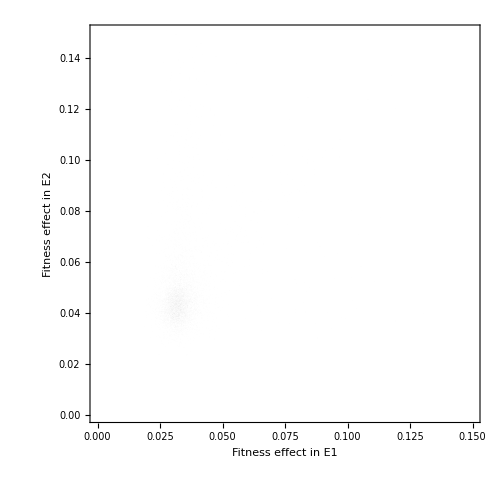

```mathematica
CorrelationPreExisting=Show[{(* sLinePlot,*)sCorrelationPlot}, ImageSize -> 500,Frame -> True,FrameLabel -> {Text[Style["Fitness effect in E1", 18,FontFamily-> "Helvetica"]],Text[Style["Fitness effect in E2", 18,FontFamily-> "Helvetica"]]}, FrameTicksStyle->Directive[Black,18, FontFamily-> "Helvetica"]]
```

```mathematica
Export["sCorrelationPlot.eps",CorrelationPreExisting,"EPS"]
```

sCorrelationPlot.eps

### Inferring μ(s) with deterministic approx

An initial attempt to infer mu assuming all beneficial lineages are legitamately included

```mathematica
DeltaS=0.001;

ScaleUp=1/DeltaS;(*FITNESS BIN WIDTH =1/THIS NUMBER*)
TauOffSet=0; (*Where is the true zero of time? Really ~30 gens earlier so Tau should have 30 added to it*)

InferredAsBeneficial=Select[Select[PutativeBeneficials, #[[2]]<1&], #[[4]]<100&];

InferredByFitness=GatherBy[InferredAsBeneficial, Round[(#[[3]])/DeltaS]&];

EffectiveNo=1000;
EffectiveTime=80;

PopSize=5*10^8;

InferredMutationRatesToClasses=Sort[Table[
FitnessOfClass=DeltaS*Round[(InferredByFitness[[k]][[1]][[3]])/DeltaS];

ProbabilityOfClassClimbingAboven0=(Exp[FitnessOfClass*EffectiveTime -(EffectiveNo*FitnessOfClass)/(Exp[FitnessOfClass*EffectiveTime]-1)] 1/(Exp[FitnessOfClass*EffectiveTime]-1));
(*Print[ProbabilityOfClassClimbingAboven0];*)

MutationRateToBin=(*1/ProbabilityOfClassClimbingAboven0*)1/PopSize Sum[Exp[-InferredByFitness[[k]][[i]][[3]]*(InferredByFitness[[k]][[i]][[4]]+TauOffSet)], {i, 1, Length[InferredByFitness[[k]]]}];

{N[FitnessOfClass], MutationRateToBin}, {k,1, Length[InferredByFitness]}]];

CumulativeAboveS=Table[{InferredMutationRatesToClasses[[j]][[1]],Sum[InferredMutationRatesToClasses[[i]][[2]], {i, j, Length[InferredMutationRatesToClasses]}]}, {j, 1, Length[InferredMutationRatesToClasses]}];
```

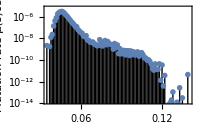

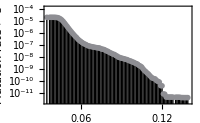

```mathematica
LogMuOfsPlot1=Show[{ListLogPlot[InferredMutationRatesToClasses,PlotMarkers -> Markers[0.0002, Black, Thin], Filling -> {1-> {Axis, Black}}]}, PlotRange -> {{0.035, 0.14},{-32, -12}}, Frame -> True,(*FrameTicks-> {{Automatic, All},{Automatic, All}},*)FrameLabel -> {Text[Style["Fitness class, s", FontFamily-> "Helvetica", 10]],Text[Style["Mutation rate μ(s)δs", FontFamily-> "Helvetica", 10]]}, ImageSize->200]

Cumulative1=Show[{(*PredictedNoThreshold[100, DeltaS, Black],*)ListLogPlot[CumulativeAboveS,PlotMarkers -> Markers[0.0002, Black,Thin],PlotStyle -> c0,(*Joined-> True,*) Filling -> {1-> {Axis, Black}},FillingStyle -> Thick]}, PlotRange -> {{0.035, 0.14},{-27, -9}}, Frame -> True,FrameTicks-> {{Table[{Log[10^i], Superscript[10,i]}, {i, -11, -4}],None(*Table[{Log[10^i], Superscript[10,i+9]}, {i, -11, -4}]*)},{Automatic, None}},FrameLabel -> {{Text[Style["Mutation rate > s", FontFamily-> "Helvetica", 10]],None(*ext[Style["Target size, bp", FontFamily-> "Helvetica", 10]]*)}, {Text[Style["Fitness class, s", FontFamily-> "Helvetica", 10]],}}, ImageSize ->200 ]
```

```mathematica
Export["CumulativeMuOfSPlot.eps",Cumulative1,"EPS"]
Export["MuOfSPlot.eps",LogMuOfsPlot1,"EPS"]
```

CumulativeMuOfSPlot.eps

MuOfSPlot.eps

Total rate comes out to about E-4, consistent with previous analysis.

### μ(s) by counting number of adaptive lineages at each s

Now infer mu(s) by counting number of lineages at each s

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/2M3"];
```

```mathematica
MeanFit2M3=ToExpression[Import["MeanFitnessFromBeneficials2M3.csv"]];
MeanFit4M3=ToExpression[Import["MeanFitnessFromBeneficials4M3.csv"]];
```

```mathematica
UnAdaptedFraction2M3=Interpolation[Table[{MeanFit2M3[[i]][[1]], Exp[-Sum[MeanFit2M3[[j]][[2]], {j, 1, i}]]}, {i, 1, Length[MeanFit2M3]}], InterpolationOrder -> 1];
UnAdaptedFraction4M3=Interpolation[Table[{MeanFit4M3[[i]][[1]], Exp[-Sum[MeanFit4M3[[j]][[2]], {j, 1, i}]]}, {i, 1, Length[MeanFit4M3]}], InterpolationOrder -> 1];
```

tstar is the time window a mutation has to occur in if it is to be observed 

tstar ideal is equivalent window if lienages were all started with a single cell

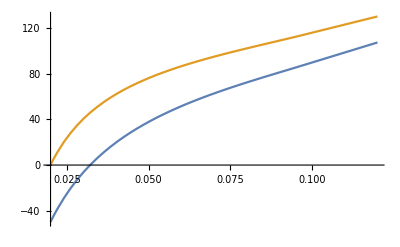

```mathematica
n0=1000;
tstar2M3=Interpolation[Table[{MeanFit2M3[[i]][[2]],MeanFit2M3[[i]][[1]]-Log[n0*MeanFit2M3[[i]][[2]]]/(MeanFit2M3[[i]][[2]])}, {i, 40, Length[MeanFit2M3]}], InterpolationOrder -> 1];
tstar4M3=Interpolation[Table[{MeanFit4M3[[i]][[2]],MeanFit4M3[[i]][[1]]-Log[n0*MeanFit4M3[[i]][[2]]]/(MeanFit4M3[[i]][[2]])}, {i, 40, Length[MeanFit4M3]}], InterpolationOrder -> 1];


tstarIdeal2M3=Interpolation[Table[{MeanFit2M3[[i]][[2]],MeanFit2M3[[i]][[1]]-2/(MeanFit2M3[[i]][[2]])}, {i, 50, Length[MeanFit2M3]}], InterpolationOrder -> 1];
tstarIdeal4M3=Interpolation[Table[{MeanFit4M3[[i]][[2]],MeanFit4M3[[i]][[1]]-2/(MeanFit4M3[[i]][[2]])}, {i, 50, Length[MeanFit4M3]}], InterpolationOrder -> 1];

Plot[{tstar2M3[s], tstarIdeal2M3[s]}, {s, 0.02, 0.12}]

TimeToOccur2M3[s_]:=NIntegrate[Exp[-Exp[-s τ]]*UnAdaptedFraction2M3[τ+2/s], {τ,-∞, tstar2M3[s]}]
TimeToOccur4M3[s_]:=NIntegrate[Exp[-Exp[-s τ]]*UnAdaptedFraction4M3[τ+2/s], {τ,-∞, tstar4M3[s]}]

TimeToOccurIdeal2M3[s_]:=NIntegrate[Exp[-Exp[-s τ]]*UnAdaptedFraction2M3[τ+2/s], {τ,-∞, tstarIdeal2M3[s]}]
TimeToOccurIdeal4M3[s_]:=NIntegrate[Exp[-Exp[-s τ]]*UnAdaptedFraction4M3[τ+2/s], {τ,-∞, tstarIdeal4M3[s]}]
```

The above plot is tstar as a function of s and tstar ideal as a function of s. The time window is zero for mutations of effect size ~2.5%

Time to occur accounts for the fact that the feeding population is reduced as time goes on which will also affect the window in which a mutation can be observed. Integrate this effect up to the time tstar and it gives you the effective number of generations that the feeding population has to form a mutant.

1. Number of lineages in a given fitness bin

2. The number of mutations expected is (N  μ(s)ds  s t) so can back out μ(s)ds from this. 

3. MutationRatePlot is simply the number of lineages that are adaptive in fitness bins

4. The DFE plots the estimated μ(s) from the above equation

```mathematica
PopSize=5*10^8;
AdaptiveOnly2M3a=Select[AllAdaptiveLineages, (#[[2]]>8 &&#[[3]]<0&& #[[8]]>-1/(#[[4]]))&];
AdaptiveOnly2M3b=Select[AllAdaptiveLineages, (#[[2]]>8 &&#[[3]]<0&& #[[8]]>-2/(#[[4]]))&];
AdaptiveOnly2M3c=Select[AllAdaptiveLineages, (#[[2]]>8 &&#[[3]]<0&& #[[8]]>-4/(#[[4]]))&];


AdaptiveOnly4M3a=Select[AllAdaptiveLineages, (#[[3]]>5 &&#[[2]]<0 && #[[10]]>-1/(#[[6]]))&];
AdaptiveOnly4M3b=Select[AllAdaptiveLineages, (#[[3]]>5 &&#[[2]]<0 && #[[10]]>-2/(#[[6]]))&];
AdaptiveOnly4M3c=Select[AllAdaptiveLineages, (#[[3]]>5 &&#[[2]]<0 && #[[10]]>-4/(#[[6]]))&];
Print["ExclusivelyAdatpive2M3=",Length[AdaptiveOnly2M3a],",",Length[AdaptiveOnly2M3b],",",Length[AdaptiveOnly2M3c]];
Print["ExclusivelyAdatpive4M3=",Length[AdaptiveOnly4M3a],",",Length[AdaptiveOnly4M3b],",",Length[AdaptiveOnly4M3c]];
```

ExclusivelyAdatpive2M3=1560,4922,14262

ExclusivelyAdatpive4M3=1403,2560,3624

```mathematica
ListOfs2M3a=Map[#[[4]]&,AdaptiveOnly2M3a];
ListOfs2M3b=Map[#[[4]]&,AdaptiveOnly2M3b];
ListOfs2M3c=Map[#[[4]]&,AdaptiveOnly2M3c];

ListOfs4M3a=Map[#[[6]]&,AdaptiveOnly4M3a];
ListOfs4M3b=Map[#[[6]]&,AdaptiveOnly4M3b];
ListOfs4M3c=Map[#[[6]]&,AdaptiveOnly4M3c];
```

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1025} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1025} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1025} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

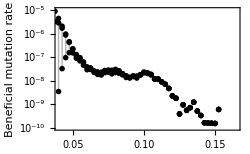

2M3TotalRate=1.06871×10^-6

2M3TotalRate=0.0000134147

2M3TotalRate=0.000110207

```mathematica
BinWidth=0.0025;

RawBinCounts1a=BinCounts[ListOfs2M3a, {0, 0.16, BinWidth}];
RawBinCounts1b=BinCounts[ListOfs2M3b, {0, 0.16, BinWidth}];
RawBinCounts1c=BinCounts[ListOfs2M3c, {0, 0.16, BinWidth}];

MutationRateByFitnessBin1a=Table[{i*BinWidth,RawBinCounts1a[[i]]/(PopSize*i*BinWidth*TimeToOccur2M3[i*BinWidth])}, {i, 1, Length[RawBinCounts1a]}];
MutationRateByFitnessBin1b=Table[{i*BinWidth,RawBinCounts1b[[i]]/(PopSize*i*BinWidth*TimeToOccur2M3[i*BinWidth])}, {i, 1, Length[RawBinCounts1b]}];
MutationRateByFitnessBin1c=Table[{i*BinWidth,RawBinCounts1c[[i]]/(PopSize*i*BinWidth*TimeToOccur2M3[i*BinWidth])}, {i, 1, Length[RawBinCounts1c]}];


DFE1=ListLogPlot[{MutationRateByFitnessBin1a, MutationRateByFitnessBin1b, MutationRateByFitnessBin1c}, Frame -> {True, True, True, True},Filling -> {1 -> {3}},PlotStyle -> Black, PlotMarkers -> {,Markers[0.015, Black, Thickness[0.005]], },FrameLabel -> {{Text[Style["Beneficial mutation rate", FontFamily-> "Helvetica", 10]],},{Text[Style["Fitness class, s", FontFamily-> "Helvetica", 10]],}},PlotRange -> {{0.04, 0.165},{10^-10, 10^-5}},FrameTicks->{{All,None(*Table[{10^i,Superscript[10,i-4]}, {i, 0, 3}]*)},{All,None}}, ImageSize -> 250]

TotalRate1a=Total[Map[#[[2]]&,MutationRateByFitnessBin1a]];
Print["2M3TotalRate=",TotalRate1a];
TotalRate1b=Total[Map[#[[2]]&,MutationRateByFitnessBin1b]];
Print["2M3TotalRate=",TotalRate1b];
TotalRate1c=Total[Map[#[[2]]&,MutationRateByFitnessBin1c]];
Print["2M3TotalRate=",TotalRate1c];
```

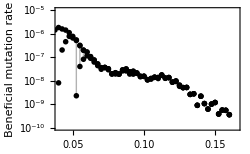

4M3TotalRate=8.65176×10^-7

4M3TotalRate=3.96506×10^-6

4M3TotalRate=0.0000139644

```mathematica
BinWidth=0.0025;

RawBinCounts2a=BinCounts[ListOfs4M3a, {0, 0.16, BinWidth}];
RawBinCounts2b=BinCounts[ListOfs4M3b, {0, 0.16, BinWidth}];
RawBinCounts2c=BinCounts[ListOfs4M3c, {0, 0.16, BinWidth}];

MutationRateByFitnessBin2a=Table[{i*BinWidth,RawBinCounts2a[[i]]/(PopSize*i*BinWidth*TimeToOccur4M3[i*BinWidth])}, {i, 1, Length[RawBinCounts2a]}];
MutationRateByFitnessBin2b=Table[{i*BinWidth,RawBinCounts2b[[i]]/(PopSize*i*BinWidth*TimeToOccur4M3[i*BinWidth])}, {i, 1, Length[RawBinCounts2b]}];
MutationRateByFitnessBin2c=Table[{i*BinWidth,RawBinCounts2c[[i]]/(PopSize*i*BinWidth*TimeToOccur4M3[i*BinWidth])}, {i, 1, Length[RawBinCounts2c]}];


DFE2=ListLogPlot[{MutationRateByFitnessBin2a, MutationRateByFitnessBin2b, MutationRateByFitnessBin2c}, Frame -> {True, True, True, True},Filling -> {1 -> {3}},PlotStyle -> Black, PlotMarkers -> {,Markers[0.015, Black, Thickness[0.005]], },FrameLabel -> {{Text[Style["Beneficial mutation rate", FontFamily-> "Helvetica", 10]],},{Text[Style["Fitness class, s", FontFamily-> "Helvetica", 10]],}},PlotRange -> {{0.04, 0.165},{10^-10, 10^-5}},FrameTicks->{{All,None(*Table[{10^i,Superscript[10,i-4]}, {i, 0, 3}]*)},{All,None}}, ImageSize -> 250]

TotalRate2a=Total[Map[#[[2]]&,MutationRateByFitnessBin2a]];
Print["4M3TotalRate=",TotalRate2a];
TotalRate2b=Total[Map[#[[2]]&,MutationRateByFitnessBin2b]];
Print["4M3TotalRate=",TotalRate2b];
TotalRate2c=Total[Map[#[[2]]&,MutationRateByFitnessBin2c]];
Print["4M3TotalRate=",TotalRate2c];
```

```mathematica
Export["dfe2M3.pdf",DFE1,"PDF"]
Export["dfe4M3.pdf",DFE2,"PDF"]
```

dfe2M3.pdf

dfe4M3.pdf

```mathematica
Export["DFE_2.eps",DFE,"EPS"]
```

DFE_2.eps

### Inferring μ(s) with deterministic approx - EXCLUDING THE “pre-existing” ONES

An initial attempt to infer mu assuming all beneficial lineages are legitamately included

```mathematica
DeltaS=0.001;
InferredByFitness2M3=GatherBy[AdaptiveOnly2M3, Round[(#[[4]])/DeltaS]&];
InferredByFitness4M3=GatherBy[AdaptiveOnly4M3, Round[(#[[6]])/DeltaS]&];
TauOffset=0;

PopSize=5*10^8;

InferredMutationRatesToClasses2M3=Sort[Table[
FitnessOfClass=DeltaS*Round[(InferredByFitness2M3[[k]][[1]][[4]])/DeltaS]+0.008;


MutationRateToBin=1/(PopSize DeltaS(1+FitnessOfClass *Log[10^-5*10^12]))Sum[Exp[-InferredByFitness2M3[[k]][[i]][[4]]*(InferredByFitness2M3[[k]][[i]][[8]]+TauOffset)], {i, 1, Length[InferredByFitness2M3[[k]]]}];

MutationBound= MutationRateToBin (*-2 √(MutationRateToBin/(5*10^8))*);
If[ MutationBound<0, MutationBound=10^-12, ];

{N[FitnessOfClass], MutationBound}, {k,1, Length[InferredByFitness2M3]}]];


InferredMutationRatesToClasses4M3=Sort[Table[
FitnessOfClass=DeltaS*Round[(InferredByFitness4M3[[k]][[1]][[6]])/DeltaS];


MutationRateToBin=1/(PopSize DeltaS(1+FitnessOfClass *Log[10^-5*10^12]))Sum[Exp[-InferredByFitness4M3[[k]][[i]][[6]]*(InferredByFitness4M3[[k]][[i]][[10]]+TauOffset)], {i, 1, Length[InferredByFitness4M3[[k]]]}];
MutationBound= MutationRateToBin(* -2 √(MutationRateToBin/(5*10^8))*);
If[ MutationBound<0, MutationBound=10^-12, ];

{N[FitnessOfClass], MutationBound}, {k,1, Length[InferredByFitness4M3]}]];




CumulativeAboveS2M3=Table[{InferredMutationRatesToClasses2M3[[j]][[1]],DeltaS*Sum[InferredMutationRatesToClasses2M3[[i]][[2]], {i, j, Length[InferredMutationRatesToClasses2M3]}]}, {j, 1, Length[InferredMutationRatesToClasses2M3]}];

CumulativeAboveS4M3=Table[{InferredMutationRatesToClasses4M3[[j]][[1]],DeltaS*Sum[InferredMutationRatesToClasses4M3[[i]][[2]], {i, j, Length[InferredMutationRatesToClasses4M3]}]}, {j, 1, Length[InferredMutationRatesToClasses4M3]}];
```

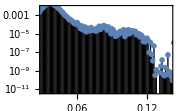

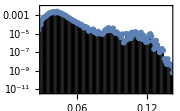

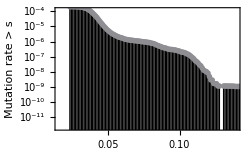

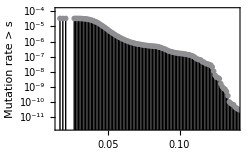

```mathematica
LogMuOfsPlot1=Show[{ListLogPlot[InferredMutationRatesToClasses2M3,PlotMarkers -> Markers[0.0002, Black, Thin], Filling -> {1-> {Axis, Black}}]}, PlotRange -> {{0.03, 0.14},{-26, -5}}, Frame -> True,(*FrameTicks-> {{Automatic, All},{Automatic, All}},*)FrameLabel -> {Text[Style["Fitness class, s", FontFamily-> "Helvetica", 10]],Text[Style["Density μ(s)", FontFamily-> "Helvetica", 10]]}, ImageSize->180]


LogMuOfsPlot2=Show[{ListLogPlot[InferredMutationRatesToClasses4M3,PlotMarkers -> Markers[0.0002, Black, Thin], Filling -> {1-> {Axis, Black}}]}, PlotRange -> {{0.03, 0.14},{-26, -5}}, Frame -> True,(*FrameTicks-> {{Automatic, All},{Automatic, All}},*)FrameLabel -> {Text[Style["Fitness class, s", FontFamily-> "Helvetica", 10]],Text[Style["Density μ(s)", FontFamily-> "Helvetica", 10]]}, ImageSize->180]

Cumulative1=Show[{(*PredictedNoThreshold[100, DeltaS, Black],*)ListLogPlot[CumulativeAboveS2M3,PlotMarkers -> Markers[0.0002, Black,Thin],PlotStyle -> c0,(*Joined-> True,*) Filling -> {1-> {Axis, Black}},FillingStyle -> Thick]}, PlotRange -> {{0.015, 0.14},{-27, -9}}, Frame -> True,FrameTicks-> {{Table[{Log[10^i], Superscript[10,i]}, {i, -11, -4, 2}],None(*Table[{Log[10^i], Superscript[10,i+9]}, {i, -11, -4}]*)},{Automatic, None}},FrameLabel -> {{Text[Style["Mutation rate > s", FontFamily-> "Helvetica", 10]],None(*ext[Style["Target size, bp", FontFamily-> "Helvetica", 10]]*)}, {Text[Style["Fitness class, s", FontFamily-> "Helvetica", 10]],}}, ImageSize ->250 ]

Cumulative2=Show[{(*PredictedNoThreshold[100, DeltaS, Black],*)ListLogPlot[CumulativeAboveS4M3,PlotMarkers -> Markers[0.0002, Black,Thin],PlotStyle -> c0,(*Joined-> True,*) Filling -> {1-> {Axis, Black}},FillingStyle -> Thick]}, PlotRange -> {{0.015, 0.14},{-27, -9}}, Frame -> True,FrameTicks-> {{Table[{Log[10^i], Superscript[10,i]}, {i, -11, -4, 2}],None(*Table[{Log[10^i], Superscript[10,i+9]}, {i, -11, -4}]*)},{Automatic, None}},FrameLabel -> {{Text[Style["Mutation rate > s", FontFamily-> "Helvetica", 10]],None(*ext[Style["Target size, bp", FontFamily-> "Helvetica", 10]]*)}, {Text[Style["Fitness class, s", FontFamily-> "Helvetica", 10]],}}, ImageSize ->250 ]
```

Plots comparing the inferred distribution to an exponential and estimating the errors on the inferences.

```mathematica
LowerMuE1=InferredMutationRatesToClasses2M3;
LowerMuE2=InferredMutationRatesToClasses4M3;
```

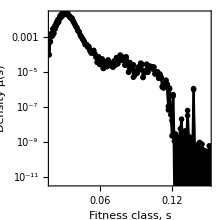

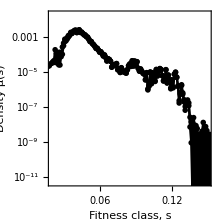

```mathematica
LogMuOfsPlot1=Show[{ListLogPlot[{HigherMuE1,LowerMuE1},Joined -> True,PlotStyle -> Black,PlotMarkers -> Markers[0.0002, Black, Thickness[0.01]], Filling -> {1-> {{2}, Black}}]}, PlotRange -> {{0.02, 0.15},{-26, -4}}, Frame -> True,FrameTicks->{{Table[{Log[10^k], Superscript[10,k]},{k, -11, -2, 3}], None}, {Table[{k, k}, {k, 0, 0.15, 0.03}],None}},FrameLabel -> {Text[Style["Fitness class, s", FontFamily-> "Helvetica", 10]],Text[Style["Density μ(s)", FontFamily-> "Helvetica", 10]]}, ImageSize->220,AspectRatio -> 1]
LogMuOfsPlot2=Show[{ListLogPlot[{HigherMuE2,LowerMuE2},Joined -> True,PlotStyle -> Black,PlotMarkers -> Markers[0.0002, Black, Thickness[0.01]], Filling -> {1-> {{2}, Black}}]}, PlotRange -> {{0.02, 0.15},{-26, -4}}, Frame -> True,FrameTicks->{{Table[{Log[10^k], Superscript[10,k]},{k, -11, -2, 3}], None}, {Table[{k, k}, {k, 0, 0.15, 0.03}],None}},FrameLabel -> {Text[Style["Fitness class, s", FontFamily-> "Helvetica", 10]],Text[Style["Density μ(s)", FontFamily-> "Helvetica", 10]]}, ImageSize->220, AspectRatio -> 1]
```

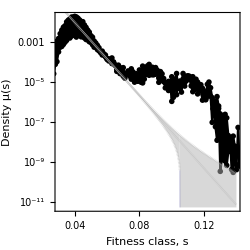

```mathematica
DifferenceE1E2=Show[{ListLogPlot[{InferredMutationRatesToClasses2M3,InferredMutationRatesToClasses4M3},Joined -> True,PlotStyle -> Black,PlotMarkers -> Markers[0.0002, Black, Thickness[0.01]], Filling -> {1-> {{2}, Black}}]}, PlotRange -> {{0.03, 0.14},{-26, -4}}, Frame -> True,(*FrameTicks-> {{Automatic, All},{Automatic, All}},*)FrameLabel -> {Text[Style["Fitness class, s", FontFamily-> "Helvetica", 10]],Text[Style["Density μ(s)", FontFamily-> "Helvetica", 10]]}, ImageSize->250, AspectRatio -> 1];
DifferenceE1E2WithE=Show[{DifferenceE1E2, ExponentialFit2M3}]
```

```mathematica
Export["MuOfsDifferenceE1E2.pdf",DifferenceE1E2WithE,"PDF"]
```

MuOfsDifferenceE1E2.pdf

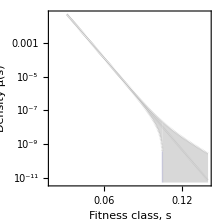

```mathematica
R=210;
Amp=40;
ExponentialFit2M3=LogPlot[{Amp Exp[-R x],Amp Exp[-R x]+(Amp Exp[-R x]/10^8)^(1/2),Amp Exp[-R x]-(Amp Exp[-R x]/10^8)^(1/2)+((Amp Exp[-R x]/10^8)^(1/2)-Amp Exp[-R x]+10^-12)UnitStep[x-0.105]}, {x, 0.0,0.14}, PlotRange -> {{0.02, 0.14},{Exp[-26], Exp[-3]}}, PlotStyle -> Directive[{RGBColor[0.7,0.7,0.7,0.5], Dashing[0.0]}], Filling -> {2 -> {{3}, RGBColor[0.7,0.7,0.7,0.5]}}, AspectRatio -> 1, Background->None, Frame -> True,FrameTicks->{{Table[{10^k, Superscript[10,k]},{k, -11, -2, 3}], None}, {Table[{k, k}, {k, 0, 0.15, 0.03}],None}},FrameLabel -> {Text[Style["Fitness class, s", FontFamily-> "Helvetica", 10]],Text[Style["Density μ(s)", FontFamily-> "Helvetica", 10]]}, ImageSize->220]
```

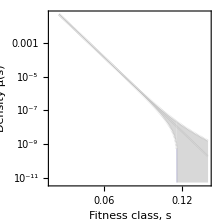

```mathematica
R=170;
Amp=4;
ExponentialFit4M3=LogPlot[{Amp Exp[-R x],Amp Exp[-R x]+(Amp Exp[-R x]/10^8)^(1/2),Amp Exp[-R x]-(Amp Exp[-R x]/10^8)^(1/2)+((Amp Exp[-R x]/10^8)^(1/2)-Amp Exp[-R x]+10^-12)UnitStep[x-0.116]}, {x, 0.0,0.14}, PlotRange -> {{0.02, 0.14},{Exp[-26], Exp[-3]}}, PlotStyle -> Directive[{RGBColor[0.7,0.7,0.7,0.5], Dashing[0.0]}], Filling -> {2 -> {{3}, RGBColor[0.7,0.7,0.7,0.5]}}, AspectRatio -> 1, Background->None, Frame -> True,FrameTicks->{{Table[{10^k, Superscript[10,k]},{k, -11, -2, 3}], None}, {Table[{k, k}, {k, 0, 0.15, 0.03}],None}},FrameLabel -> {Text[Style["Fitness class, s", FontFamily-> "Helvetica", 10]],Text[Style["Density μ(s)", FontFamily-> "Helvetica", 10]]}, ImageSize->220]
```

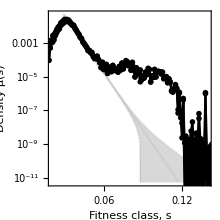

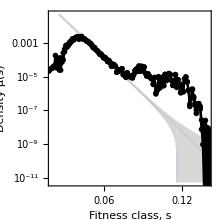

```mathematica
LogMuOfsPlot1=Show[{ExponentialFit2M3,LogMuOfsPlot1}]
LogMuOfsPlot2=Show[{ExponentialFit4M3,LogMuOfsPlot2}]
```

```mathematica
Export["ExponentialFit.pdf",ExponentialFit,"PDF"]
```

```mathematica
Export["MuOfSDifference.pdf",DifferencesE1E2,"PDF"]
```

MuOfSDifference.pdf

```mathematica
Export["MutationSpectrumE1.csv",InferredMutationRatesToClasses2M3,"CSV"]
Export["MutationSpectrumE2.csv",InferredMutationRatesToClasses4M3,"CSV"]
```

MutationSpectrumE1.csv

MutationSpectrumE2.csv

```mathematica
Export["MuOfsDeterministic2M3.pdf",LogMuOfsPlot1,"PDF"]
```

MuOfsDeterministic2M3.pdf

```mathematica
Export["MuOfsDeterministic4M3.pdf",LogMuOfsPlot2,"PDF"]
```

MuOfsDeterministic4M3.pdf

Total rate comes out to about E-4, consistent with previous analysis.

### Errors in s and tau binned by fitness.

```mathematica
TableForm[Adaptive2M3[[1;;20]], TableHeadings->{{},{"BC","Log(Pr[b]/Pr[n])_1","Log(Pr[b]/Pr[n])_2","s_1","δs_1","s_2","δs_2","τ_1","δτ_1", "τ_2","δτ_2"}}]
```

| BC | Log(Pr[b]/Pr[n])_1 | Log(Pr[b]/Pr[n])_2 | s_1 | δs_1 | s_2 | δs_2 | τ_1 | δτ_1 | τ_2 | δτ_2
 | 15 | 6150.88 | -5.8308 | 0.103664 | 0.00111082 | 0.00001 | 0.01 | 0.800242 | 1.08688 | 0 | 5
 | 25 | 35.8729 | 53.4893 | 0.0320317 | 0.00389843 | 0.0441855 | 0.00489694 | -88.3419 | 20.7353 | -66.5693 | 15.5798
 | 32 | 4804.87 | -9.82457 | 0.106252 | 0.00125173 | 0.00001 | 0.01 | 5.88589 | 1.1374 | 0 | 5
 | 36 | 9.77161 | 2.36768 | 0.0280161 | 0.00569951 | 0.0322031 | 0.00991143 | -99.2854 | 37.263 | -90.7373 | 50.1489
 | 41 | 29.5997 | -6.33312 | 0.0346853 | 0.00516264 | 0.00001 | 0.01 | -76.8749 | 24.4162 | 0 | 5
 | 44 | 6.61163 | 20.2899 | 0.0397599 | 0.00960887 | 0.0520164 | 0.01339 | -41.6679 | 32.712 | -38.8765 | 30.76
 | 45 | 4.63207 | -9.94195 | 0.0339007 | 0.00756314 | 0.00001 | 0.01 | -57.0137 | 32.5379 | 0 | 5
 | 53 | 91.5746 | 15.0246 | 0.0319188 | 0.00285423 | 0.0362429 | 0.00743255 | -112.736 | 17.3321 | -82.5324 | 31.7389
 | 62 | 33.6501 | -11.1634 | 0.0296774 | 0.00439612 | 0.00001 | 0.01 | -95.9148 | 25.8763 | 0 | 5
 | 63 | 39.0142 | -11.7271 | 0.0318448 | 0.00376077 | 0.00001 | 0.01 | -84.1406 | 19.2321 | 0 | 5
 | 67 | 21.868 | -1.98269 | 0.0329494 | 0.00599013 | 0.00001 | 0.01 | -77.3214 | 29.6078 | 0 | 5
 | 76 | 16.5187 | -9.59575 | 0.0437944 | 0.0091125 | 0.00001 | 0.01 | -35.2907 | 26.9975 | 0 | 5
 | 84 | 6.13803 | -9.46944 | 0.0429753 | 0.0096036 | 0.00001 | 0.01 | -19.0222 | 24.6675 | 0 | 5
 | 90 | 35.8036 | 11.6274 | 0.0348549 | 0.00451112 | 0.0540806 | 0.0128387 | -74.9267 | 20.7807 | -25.408 | 25.2323
 | 91 | 48.1901 | -10.9191 | 0.0294033 | 0.00352431 | 0.00001 | 0.01 | -109.724 | 22.5278 | 0 | 5
 | 109 | 24.8074 | -10.2893 | 0.0254923 | 0.00455173 | 0.00001 | 0.01 | -127.486 | 36.4206 | 0 | 5
 | 110 | 2241.92 | 432.879 | 0.0602238 | 0.000912524 | 0.0678411 | 0.00261917 | -59.7234 | 2.31931 | -40.4906 | 4.66852
 | 125 | 27.8711 | 39.9056 | 0.0353898 | 0.0040197 | 0.0480603 | 0.00494606 | -61.8572 | 16.4654 | -48.4713 | 12.6381
 | 126 | 1194.67 | 5.27855 | 0.0797347 | 0.00196075 | 0.0515179 | 0.0128356 | -11.6064 | 2.73031 | -25.1037 | 26.3825
 | 128 | 80.4844 | 15.4424 | 0.0297627 | 0.0031588 | 0.047077 | 0.0113323 | -130.564 | 22.5266 | -49.1014 | 30.9841

0.005

0.08

```mathematica
BinWidth=0.01;
BinWidthTau=20;
data=
Table[
ErrorsForS=Map[#[[5]]&,Select[Adaptive2M3, (s<#[[4]]<s+BinWidth &&τ<#[[8]]<τ+BinWidthTau && Im[#[[5]]]==0)&]];
ErrorsForTau=Map[#[[9]]&,Select[Adaptive2M3, (s<#[[4]]<s+BinWidth  &&τ<#[[8]]<τ+BinWidthTau&& Im[#[[9]]]==0)&]];

If[Length[ErrorsForS]>2,
MeanErrorS=Median[ErrorsForS];
ErrorErrorS=StandardDeviation[ErrorsForS];,MeanErrorS=0.0;
ErrorErrorS=0.0;];

If[Length[ErrorsForTau]>2,
MeanErrorTau=Median[ErrorsForTau];
ErrorErrorTau=StandardDeviation[ErrorsForTau];,MeanErrorTau=0.0;
ErrorErrorTau=0.0;];

{s,τ, MeanErrorS,ErrorErrorS, MeanErrorTau,ErrorErrorTau}, {s, 0.03, 0.14,BinWidth},{τ, -100, 60, BinWidthTau}];
```

```mathematica
sData=Map[{#[[2]], #[[1]], #[[3]]}&,Flatten[data, 1]];
TauData=Map[{#[[2]], #[[1]], #[[5]]}&,Flatten[data, 1]];
```

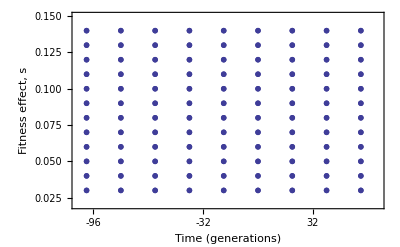

-Graphics-

```mathematica
sErrorsPlot=Show[Table[ListPlot[{{sData[[i]][[1]],sData[[i]][[2]]}}, PlotMarkers -> Markers[(*0.003*)0.25(sData[[i]][[3]])^0.5, Black,Thickness[0.0003]], PlotRange -> {{-105, 70},{0.02, 0.15}}, Frame -> True,FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Fitness effect, s", FontFamily-> "Helvetica", 10]]}, FrameTicks->{{Automatic, None}, {Table[{16k, 16k}, {k, -10, 7}],None}},AxesOrigin -> {-150,0}], {i, 1, Length[sData]}], ImageSize-> 400 ]
TauErrorsPlot=Show[Table[ListPlot[{{TauData[[i]][[1]],TauData[[i]][[2]]}}, PlotMarkers -> Markers[(*0.003*)0.009(TauData[[i]][[3]])^0.5, Black,Thickness[0.0003]], PlotRange -> {{-105, 70},{0.02, 0.15}}, Frame -> True,FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Fitness effect, s", FontFamily-> "Helvetica", 10]]}, FrameTicks->{{Automatic, None}, {Table[{16k, 16k}, {k, -10, 7}],None}},AxesOrigin -> {-150,0}], {i, 1, Length[sData]}], ImageSize-> 400 ]
```

```mathematica
Export["sErrors.pdf",sErrorsPlot,"PDF"]
Export["TauErrors.pdf",TauErrorsPlot,"PDF"]
```

sErrors.pdf

TauErrors.pdf

```mathematica
ErrorsForTau[[1;;5]]
```

{13.0925,13.015,7.99076,2.82484,27.0246}

## 8. Joy-division plot and movie

### Importing data

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/AllProcessedBarcodeData"];
AllAdaptiveLineages=ToExpression[Import["AdaptiveLineagesE1&E2.csv"]];
```

```mathematica
TableForm[AllAdaptiveLineages[[1;;20]], TableHeadings->{{},{"BC","Log(Pr[b]/Pr[n])_1","Log(Pr[b]/Pr[n])_2","s_1","δs_1","s_2","δs_2","τ_1","δτ_1", "τ_2","δτ_2"}}]
```

| BC | Log(Pr[b]/Pr[n])_1 | Log(Pr[b]/Pr[n])_2 | s_1 | δs_1 | s_2 | δs_2 | τ_1 | δτ_1 | τ_2 | δτ_2
 | 1 | -10.3503 | 437.533 | 0.00001 | 0.01 | 0.0874863 | 0.00324045 | 0 | 5 | -10.7233 | 3.50301
 | 2 | -8.94149 | -9.62843 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 3 | -6.31793 | -9.7379 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 7 | -6.18343 | -8.93869 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 14 | -6.51442 | -8.40835 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 15 | 6150.88 | -5.8308 | 0.103664 | 0.00111082 | 0.00001 | 0.01 | 0.800242 | 1.08688 | 0 | 5
 | 16 | -7.31047 | -9.49237 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 17 | -4.87625 | -8.63283 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 18 | -10.1805 | -9.32023 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 23 | -10.387 | -10.0314 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 25 | 35.8729 | 53.4893 | 0.0320317 | 0.00389843 | 0.0441855 | 0.00489694 | -88.3419 | 20.7353 | -66.5693 | 15.5798
 | 26 | -11.5497 | -11.3295 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 31 | -8.94454 | -9.95944 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 32 | 4804.87 | -9.82457 | 0.106252 | 0.00125173 | 0.00001 | 0.01 | 5.88589 | 1.1374 | 0 | 5
 | 33 | 0.931429 | -5.82122 | 0.0308673 | 0.00855509 | 0.00001 | 0.01 | -67.3532 | 43.0152 | 0 | 5
 | 34 | -8.73268 | -10.0516 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 35 | -9.89479 | -4.51869 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 36 | 9.77161 | 2.36768 | 0.0280161 | 0.00569951 | 0.0322031 | 0.00991143 | -99.2854 | 37.263 | -90.7373 | 50.1489
 | 37 | -7.62162 | -9.68673 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 38 | -10.2606 | -10.5248 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5

```mathematica
Adaptive2M3=Select[AllAdaptiveLineages, #[[2]]>8 &];
Print["NumberAdaptive2M3=",Length[Adaptive2M3]];
Adaptive4M3=Select[AllAdaptiveLineages, #[[3]]>2 &];
Print["NumberAdaptive4M3=",Length[Adaptive4M3]];

SetDirectory["~/Dropbox/BayesianAnalysis/4M3"];
MeanFit2M3=ToExpression[Import["MeanFitnessFromBeneficials2M3.csv"]];
MeanFit4M3=ToExpression[Import["MeanFitnessFromBeneficials4M3.csv"]];
```

NumberAdaptive2M3=22184

NumberAdaptive4M3=13513

```mathematica
UnAdaptedFraction4M3=Interpolation[Table[{MeanFit4M3[[i]][[1]],Exp[-Sum[MeanFit4M3[[j]][[2]], {j, 1, i}]]}, {i, 1, Length[MeanFit4M3]}]];

UnAdaptedFraction2M3=Interpolation[Table[{MeanFit2M3[[i]][[1]],Exp[-Sum[MeanFit2M3[[j]][[2]], {j, 1, i}]]}, {i, 1, Length[MeanFit2M3]}]];
```

### Plotting with full diversity inside

```mathematica
AllRectangles={};
CrazyPlots=Table[

Print["Time point=",t];

(*break down adaptive set by barcode fitness into fitness classes*)
FitnessSizes=Sort[Table[
τ=Adaptive4M3[[BC]][[10]];
s=Adaptive4M3[[BC]][[6]];
Size=Exp[s (t-τ)]/s*UnAdaptedFraction4M3[t];
{BC,s, Size}, {BC, 1, Length[Adaptive4M3]}], #1[[3]]<#2[[3]]&];
Sizes=Table[FitnessSizes[[i]][[3]], {i, 1, Length[FitnessSizes]}];
Fitnesses=Table[FitnessSizes[[i]][[2]], {i, 1, Length[FitnessSizes]}];

MaxFitness=Max[Fitnesses];
Print["Max Fitness",MaxFitness];
FitnessBinWidth=0.002;
BarcodesInEachFitnessBin={};


Do[

NumberOfCellsInFitnessBin=0.0;

BarcodesInRange={};
Do[If[FitnessBin<Fitnesses[[i]]<FitnessBin+FitnessBinWidth &&Sizes[[i]]>0, AppendTo[BarcodesInRange,i]];
, {i, 1, Length[FitnessSizes]}];

 AppendTo[BarcodesInEachFitnessBin, {FitnessBin,BarcodesInRange}];

,{FitnessBin, 0, MaxFitness, FitnessBinWidth}];

(*Put all rectangles in table*)
i=1;
PreviousHeight=0.0;
Do[
BCs=BarcodesInEachFitnessBin[[Bin]][[2]];
(*Print[BCs];*)
Binx=BarcodesInEachFitnessBin[[Bin]][[1]];
(*Print[Binx];*)
StartingN=0.0;
LowX=Binx-FitnessBinWidth;
HighX=Binx+FitnessBinWidth;

Do[

i=i+1;
If[EvenQ[i], Color=White,Color=ColorList[[(t-8)/8]]];

RectangleCoords={EdgeForm[{Thickness[0.001],Black}],Specularity[0.2,1],Polygon[{{Binx-FitnessBinWidth/2,t,StartingN},{Binx-FitnessBinWidth/2,t,StartingN+Sizes[[Barcode]]},{Binx+FitnessBinWidth/2,t,StartingN+Sizes[[Barcode]]},{Binx+FitnessBinWidth/2,t,StartingN}}]};
StartingN=StartingN+Sizes[[Barcode]];
AppendTo[AllRectangles, Color];
AppendTo[AllRectangles,RectangleCoords];
, {Barcode, BCs}];
AppendTo[AllRectangles,{Black,Thickness[0.005],Line[{{Binx-FitnessBinWidth/2,t,PreviousHeight},{Binx-FitnessBinWidth/2,t,StartingN}, {Binx+FitnessBinWidth/2,t,StartingN}}]}];
(*Print[Bin];*)
PreviousHeight=StartingN;

, {Bin, 1,Length[BarcodesInEachFitnessBin]}];
, {t, 112, 112, 8}];
ClearMemory

FloorCoords=Table[{MeanFit4M3[[i]][[2]], MeanFit4M3[[i]][[1]],0}, {i, 1, Length[MeanFit4M3]}];
AppendTo[FloorCoords, {0,112,0}];
FloorPolygon={EdgeForm[{Thickness[0.001],Black}],Specularity[0.2,1],Polygon[FloorCoords]};
AppendTo[AllRectangles, Gray];
AppendTo[AllRectangles, FloorPolygon];
```

Time point=112

Max Fitness0.4

```mathematica
CrazyPlot3D=Graphics3D[AllRectangles,BoxRatios-> {3,3,3}, Background -> None, PlotRange -> {{0.0,0.165}, {23, 114}, {0, 20000000}},  ViewPoint-> {0., -25,15},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},Lighting->"Neutral",Axes->True,AxesLabel->{Text[Style["Fitness, s", FontFamily-> "Helvetica", 10]],,Rotate[Text[Style["Cell Number", FontFamily-> "Helvetica", 10]], π/2]},Ticks->{Automatic,Table[i, {i, 0, 112, 8}],{{20000000, "2x10^7"}}}, TicksStyle ->  Directive[FontFamily-> "Helvetica", 10], ImageSize-> 500, Boxed-> False];
```

```mathematica
Export["JoyDivisionPlot12.eps",CrazyPlot3D,"EPS"]
```

JoyDivisionPlot12.eps

```mathematica
Export["JoyDivisionPlot.pdf",CrazyPlot3D,"AllowRasterization"-> True, ImageResolution-> 300, ImageSize -> 400]
```

JoyDivisionPlot.pdf

### Plotting only the top

```mathematica
AllRectangles={};
CrazyPlots=Table[

Print["Time point=",t];

(*break down adaptive set by barcode fitness into fitness classes*)
FitnessSizes=Sort[Table[
τ=Adaptive4M3[[BC]][[10]];
s=Adaptive4M3[[BC]][[6]];
Size=Exp[s (t-τ)]/s*UnAdaptedFraction4M3[t];
{BC,s, Size}, {BC, 1, Length[Adaptive4M3]}], #1[[3]]<#2[[3]]&];
Sizes=Table[FitnessSizes[[i]][[3]], {i, 1, Length[FitnessSizes]}];
Fitnesses=Table[FitnessSizes[[i]][[2]], {i, 1, Length[FitnessSizes]}];

MaxFitness=Max[Fitnesses];
Print["Max Fitness",MaxFitness];
FitnessBinWidth=0.002;
BarcodesInEachFitnessBin={};


Do[

NumberOfCellsInFitnessBin=0.0;

BarcodesInRange={};
Do[If[FitnessBin<Fitnesses[[i]]<FitnessBin+FitnessBinWidth &&Sizes[[i]]>0, AppendTo[BarcodesInRange,i]];
, {i, 1, Length[FitnessSizes]}];

 AppendTo[BarcodesInEachFitnessBin, {FitnessBin,BarcodesInRange}];

,{FitnessBin, 0, MaxFitness, FitnessBinWidth}];

(*Put all rectangles in table*)
i=1;
PreviousHeight=0.0;
Do[
BCs=BarcodesInEachFitnessBin[[Bin]][[2]];
(*Print[BCs];*)
Binx=BarcodesInEachFitnessBin[[Bin]][[1]];
(*Print[Binx];*)
StartingN=0.0;
LowX=Binx-FitnessBinWidth;
HighX=Binx+FitnessBinWidth;

BinHeight=Sum[Sizes[[Barcode]], {Barcode, BCs}];

RectangleCoords={EdgeForm[None],Specularity[0.5,1],Polygon[{{Binx-FitnessBinWidth/2,t,StartingN},{Binx-FitnessBinWidth/2,t,StartingN+BinHeight},{Binx+FitnessBinWidth/2,t,StartingN+BinHeight},{Binx+FitnessBinWidth/2,t,StartingN}}]};
StartingN=StartingN+BinHeight;
AppendTo[AllRectangles,Scheme4[(Bin-15)/30]];
AppendTo[AllRectangles,RectangleCoords];

AppendTo[AllRectangles,{Black,Thickness[0.003],Line[{{Binx-FitnessBinWidth/2,t,PreviousHeight},{Binx-FitnessBinWidth/2,t,StartingN}, {Binx+FitnessBinWidth/2,t,StartingN}}]}];
(*Print[Bin];*)
PreviousHeight=StartingN;

, {Bin, 1,Length[BarcodesInEachFitnessBin]}];
, {t, 0, 132, 4}];
ClearMemory
```

Time point=0

Max Fitness0.4

Time point=4

Max Fitness0.4

Time point=8

Max Fitness0.4

Time point=12

Max Fitness0.4

Time point=16

Max Fitness0.4

Time point=20

Max Fitness0.4

Time point=24

Max Fitness0.4

Time point=28

Max Fitness0.4

Time point=32

Max Fitness0.4

Time point=36

Max Fitness0.4

Time point=40

Max Fitness0.4

Time point=44

Max Fitness0.4

Time point=48

Max Fitness0.4

Time point=52

Max Fitness0.4

Time point=56

Max Fitness0.4

Time point=60

Max Fitness0.4

Time point=64

Max Fitness0.4

Time point=68

Max Fitness0.4

Time point=72

Max Fitness0.4

Time point=76

Max Fitness0.4

Time point=80

Max Fitness0.4

Time point=84

Max Fitness0.4

Time point=88

Max Fitness0.4

Time point=92

Max Fitness0.4

Time point=96

Max Fitness0.4

Time point=100

Max Fitness0.4

Time point=104

Max Fitness0.4

Time point=108

Max Fitness0.4

Time point=112

Max Fitness0.4

Time point=116

Max Fitness0.4

Time point=120

Max Fitness0.4

Time point=124

Max Fitness0.4

Time point=128

Max Fitness0.4

Time point=132

Max Fitness0.4

```mathematica
CrazyPlot3D=Graphics3D[AllRectangles,BoxRatios-> {3,6.5,4}, Background ->None, PlotRange -> {{0,0.165}, {0, 132}, {0, 50000000}},  ViewPoint-> {5, -45,15},AxesEdge->{{-1,-1},{1,-1},{1,1}},Lighting->"Neutral",Axes->True,AxesLabel->{Text[Style["Fitness, s", FontFamily-> "Helvetica", 10]],Text[Style["   Time", FontFamily-> "Helvetica", 10]],Rotate[Text[Style["Cell Number", FontFamily-> "Helvetica", 10]], π/2]},Ticks->{Automatic,Table[i, {i, 0, 132, 24}],{{50000000, "5*10^7"}}}, TicksStyle ->  Directive[FontFamily-> "Helvetica", 10], ImageSize-> 200, Boxed-> False]
```

-Graphics3D-

```mathematica
MeanFitnessCurtain2M3=Join[Table[{MeanFit2M3[[i]][[2]],MeanFit2M3[[i]][[1]],0}, {i, 1, Length[MeanFit2M3]}], Table[{MeanFit2M3[[Length[MeanFit2M3]-i+1]][[2]],MeanFit2M3[[Length[MeanFit2M3]-i+1]][[1]],50000000}, {i, 1, Length[MeanFit2M3]}]];

MeanFitnessCurtain4M3=Join[Table[{MeanFit4M3[[i]][[2]],MeanFit4M3[[i]][[1]],0}, {i, 1, Length[MeanFit4M3]}], Table[{MeanFit4M3[[Length[MeanFit4M3]-i+1]][[2]],MeanFit4M3[[Length[MeanFit4M3]-i+1]][[1]],50000000}, {i, 1, Length[MeanFit4M3]}]];
```

```mathematica
Curtain2M3=Graphics3D[{Opacity[0.25],Gray,Polygon[MeanFitnessCurtain2M3]},BoxRatios-> {3,6.5,4}, Background ->None, PlotRange -> {{0.00,0.165}, {0, 132}, {0, 50000000}},  ViewPoint-> {5, -45,15},AxesEdge->{{-1,-1},{1,-1},{1,1}},Lighting->"Neutral",Axes->True,AxesLabel->{Text[Style["Fitness, s", FontFamily-> "Helvetica", 10]],,Rotate[Text[Style["Cell Number", FontFamily-> "Helvetica", 10]], π/2]},Ticks->{Automatic,Table[i, {i, 0, 132, 16}],{{100000000, "10^8"}}}, TicksStyle ->  Directive[FontFamily-> "Helvetica", 10], ImageSize-> 200];

Curtain4M3=Graphics3D[{Opacity[0.25],Gray,Polygon[MeanFitnessCurtain4M3]},BoxRatios-> {3,6.5,4}, Background ->None, PlotRange -> {{0.00,0.165}, {0, 132}, {0, 50000000}},  ViewPoint-> {5, -45,15},AxesEdge->{{-1,-1},{1,-1},{1,1}},Lighting->"Neutral",Axes->True,AxesLabel->{Text[Style["Fitness, s", FontFamily-> "Helvetica", 10]],Text[Style["  Time", FontFamily-> "Helvetica", 10]],Rotate[Text[Style["Cell Number", FontFamily-> "Helvetica", 10]], π/2]},Ticks->{Automatic,Table[i, {i, 0, 132, 16}],{{100000000, "10^8"}}}, TicksStyle ->  Directive[FontFamily-> "Helvetica", 10], ImageSize-> 200];
```

```mathematica
CellsByFitness=Show[{CrazyPlot3D, Curtain4M3}]
```

-Graphics3D-

```mathematica
Export["JoyDivision4M3.pdf",CellsByFitness,"PDF"]
```

JoyDivision4M3.pdf

### The plot in 3D

Determine the interpolation formulae for mean fitness and the unadaptive fraction (integral of mean fitness over time)

```mathematica
MeanFitnessBeforeZero=Table[ {8i, 10^-7}, {i, -15, TimePoints[[1]]/T}];
MeanFitnessExtended=Join[ MeanFitnessBeforeZero,MeanFitnessList];
UnAdaptedFraction=Table[{MeanFitnessExtended[[j]][[1]],Exp[-Sum[(MeanFitnessExtended[[t]][[1]]-MeanFitnessExtended[[t-1]][[1]])*MeanFitnessExtended[[t]][[2]], {t, 2,j}]]}, {j, 2, Length[MeanFitnessExtended]}];
InterpolatedMeanFitness=Interpolation[MeanFitnessExtended, InterpolationOrder->1];
InterpolatedUnAdaptiveFraction=Interpolation[UnAdaptedFraction, InterpolationOrder->1];
```

```mathematica
BeneficialLineages=Select[PutativeBeneficials, #[[2]]<0.1&];
Print["NumberBeneficial=", Length[BeneficialLineages]];
```

NumberBeneficial=29549

```mathematica
ColorOfEachBarcode=Table[{i,RandomChoice[{c1, c2, c3, c4, c5, c6, c7, c8, c9}]}, {i, 1, Length[BeneficialLineages]}];
```

```mathematica
AllRectangles={};
CrazyPlots=Table[
Print["Time point=",t];

(*break down adaptive set by barcode fitness into fitness classes*)
FitnessSizes=Sort[Table[
τ=BeneficialLineages[[BC]][[4]];
s=BeneficialLineages[[BC]][[3]];
Size=Exp[s (t-τ)]/s*InterpolatedUnAdaptiveFraction[t];
{BC,s, Size}, {BC, 1, Length[BeneficialLineages]}], #1[[3]]<#2[[3]]&];
Sizes=Table[FitnessSizes[[i]][[3]], {i, 1, Length[FitnessSizes]}];
Fitnesses=Table[FitnessSizes[[i]][[2]], {i, 1, Length[FitnessSizes]}];

MaxFitness=Max[Fitnesses];
Print["Max Fitness",MaxFitness];
FitnessBinWidth=0.001;
BarcodesInEachFitnessBin={};


Do[

NumberOfCellsInFitnessBin=0.0;

BarcodesInRange={};
Do[If[FitnessBin<Fitnesses[[i]]<FitnessBin+FitnessBinWidth &&Sizes[[i]]>2000, AppendTo[BarcodesInRange,i]];
, {i, 1, Length[FitnessSizes]}];

 AppendTo[BarcodesInEachFitnessBin, {FitnessBin,BarcodesInRange}];

,{FitnessBin, 0, MaxFitness, FitnessBinWidth}];

(*Put all rectangles in table*)

PreviousHeight=0.0;
Do[
BCs=BarcodesInEachFitnessBin[[Bin]][[2]];
(*Print[BCs];*)
Binx=BarcodesInEachFitnessBin[[Bin]][[1]];
(*Print[Binx];*)
StartingN=0.0;
LowX=Binx-FitnessBinWidth;
HighX=Binx+FitnessBinWidth;

Do[
Color=ColorOfEachBarcode[[Position[ColorOfEachBarcode,Barcode][[1]][[1]]]][[2]];
RectangleCoords={EdgeForm[Color],Polygon[{{Binx-FitnessBinWidth/2,t,StartingN},{Binx-FitnessBinWidth/2,t,StartingN+Sizes[[Barcode]]},{Binx+FitnessBinWidth/2,t,StartingN+Sizes[[Barcode]]},{Binx+FitnessBinWidth/2,t,StartingN}}]};
StartingN=StartingN+Sizes[[Barcode]];
AppendTo[AllRectangles, Color];
AppendTo[AllRectangles,RectangleCoords];
, {Barcode, BCs}];
AppendTo[AllRectangles,{Black,Thickness[0.002],Line[{{Binx-FitnessBinWidth/2,t,PreviousHeight},{Binx-FitnessBinWidth/2,t,StartingN}, {Binx+FitnessBinWidth/2,t,StartingN}}]}];
(*Print[Bin];*)
PreviousHeight=StartingN;

, {Bin, 1,Length[BarcodesInEachFitnessBin]}];
, {t, 72, 88, 8}];
```

Time point=72

Max Fitness0.286071

Time point=80

Max Fitness0.286071

$Aborted

```mathematica
CrazyPlot3D=(*Rasterize[*)Graphics3D[AllRectangles,BoxRatios-> {3,5,3}, Background -> None, Axes -> True, PlotRange -> {{-0.01,0.15}, {31, 112}, {0, 15000000}},  ViewPoint-> {-0.3, -15,9},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},Lighting->"Neutral",Axes->True,AxesLabel->{Text[Style["Fitness, s", FontFamily-> "Helvetica", 10]],,Rotate[Text[Style["Cell Number", FontFamily-> "Helvetica", 10]], π/2]},Ticks->{Automatic,Table[i, {i, 0, 112, 16}],{{15000000, ""}}}, TicksStyle ->  Directive[FontFamily-> "Helvetica", 10], ImageSize-> 500, Boxed-> False](*, RasterSize->1000]*);
```

```mathematica
CrazyPlot3D
```

-Graphics3D-

```mathematica
Export[StringJoin["CrazyPlot2M3.pdf"],CrazyPlot3D,"PDF"];
```

### The movie

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/2M3"];
(*ReadTrajectories2M3=ToExpression[Import["ReadTrajectories2M3.csv"]];
ReadDepths2M3=ToExpression[Import["ReadDepths2M3.csv"]];*)
PutativeBeneficials=ToExpression[Import["BayesianAnalysis2M3.csv"]];
CellNumberTrajectories2M3=ToExpression[Import["CellNumberTrajectories2M3.csv"]];
```

```mathematica
xBarKappa=ToExpression[Import["InferredxBArAndKappa2M3.csv"]];
TimePoints={0,16,32, 40, 48, 64, 72, 80, 88, 96, 104, 112};
MeanFitnessList=Table[{TimePoints[[i+1]], xBarKappa[[i]][[1]]},{i, 1, Length[xBarKappa]}];
KappaList=Table[{TimePoints[[i]], xBarKappa[[i]][[2]]},{i, 1, Length[xBarKappa]}];
```

Import the true beneficial mutatation data and true mean fitness. SIMULATION only.

```mathematica
(*TrueFitnessesAndSizeTraj=ToExpression[Import["AllMutationTrajSimStepFunc.csv"]];
TrueMeanFitness=ToExpression[Import["MeanFitnessesSimStepFunc.csv"]];*)
```

Determine the interpolation formulae for mean fitness and the unadaptive fraction (integral of mean fitness over time)

```mathematica
MeanFitnessBeforeZero=Table[ {8i, 10^-7}, {i, -15, TimePoints[[1]]/T}];
MeanFitnessExtended=Join[ MeanFitnessBeforeZero,MeanFitnessList];
UnAdaptedFraction=Table[{MeanFitnessExtended[[j]][[1]],Exp[-Sum[(MeanFitnessExtended[[t]][[1]]-MeanFitnessExtended[[t-1]][[1]])*MeanFitnessExtended[[t]][[2]], {t, 2,j}]]}, {j, 2, Length[MeanFitnessExtended]}];
InterpolatedMeanFitness=Interpolation[MeanFitnessExtended, InterpolationOrder->1];
InterpolatedUnAdaptiveFraction=Interpolation[UnAdaptedFraction, InterpolationOrder->1];
```

```mathematica
BeneficialLineages=Select[PutativeBeneficials, #[[2]]<0.1&];
Print["NumberBeneficial=", Length[BeneficialLineages]];
```

NumberBeneficial=29549

```mathematica
ColorOfEachBarcode=Table[{i,RandomChoice[{c1, c2, c3, c4, c5, c6, c7, c8, c9}]}, {i, 1, Length[BeneficialLineages]}];
```

```mathematica
AllRectangles={};
CrazyPlots=Table[
Print["Time point=",t];

(*break down adaptive set by barcode fitness into fitness classes*)
FitnessSizes=Sort[Table[
τ=BeneficialLineages[[BC]][[4]];
s=BeneficialLineages[[BC]][[3]];
Size=Exp[s (t-τ)]/s*InterpolatedUnAdaptiveFraction[t];
{BC,s, Size}, {BC, 1, Length[BeneficialLineages]}], #1[[3]]<#2[[3]]&];
Sizes=Table[FitnessSizes[[i]][[3]], {i, 1, Length[FitnessSizes]}];
Fitnesses=Table[FitnessSizes[[i]][[2]], {i, 1, Length[FitnessSizes]}];

MaxFitness=Max[Fitnesses];
Print["Max Fitness",MaxFitness];
FitnessBinWidth=0.001;
BarcodesInEachFitnessBin={};


Do[

NumberOfCellsInFitnessBin=0.0;

BarcodesInRange={};
Do[If[FitnessBin<Fitnesses[[i]]<FitnessBin+FitnessBinWidth &&Sizes[[i]]>3000, AppendTo[BarcodesInRange,i]];
, {i, 1, Length[FitnessSizes]}];

 AppendTo[BarcodesInEachFitnessBin, {FitnessBin,BarcodesInRange}];

,{FitnessBin, 0, MaxFitness, FitnessBinWidth}];

(*Put all rectangles in table*)

PreviousHeight=0.0;
Do[
BCs=BarcodesInEachFitnessBin[[Bin]][[2]];
(*Print[BCs];*)
Binx=BarcodesInEachFitnessBin[[Bin]][[1]];
(*Print[Binx];*)
StartingN=0.0;
LowX=Binx-FitnessBinWidth;
HighX=Binx+FitnessBinWidth;

Do[
Color=ColorOfEachBarcode[[Position[ColorOfEachBarcode,Barcode][[1]][[1]]]][[2]];
RectangleCoords={EdgeForm[Color],Polygon[{{Binx-FitnessBinWidth/2,StartingN},{Binx-FitnessBinWidth/2,StartingN+Sizes[[Barcode]]},{Binx+FitnessBinWidth/2,StartingN+Sizes[[Barcode]]},{Binx+FitnessBinWidth/2,StartingN}}]};
StartingN=StartingN+Sizes[[Barcode]];
AppendTo[AllRectangles, Color];
AppendTo[AllRectangles,RectangleCoords];
, {Barcode, BCs}];
AppendTo[AllRectangles,{Black,Thickness[0.002],Line[{{Binx-FitnessBinWidth/2,PreviousHeight},{Binx-FitnessBinWidth/2,StartingN}, {Binx+FitnessBinWidth/2,StartingN}}]}];
(*Print[Bin];*)
PreviousHeight=StartingN;

, {Bin, 1,Length[BarcodesInEachFitnessBin]}];
, {t, 90, 90, 1}];
```

Time point=90

Max Fitness0.286071

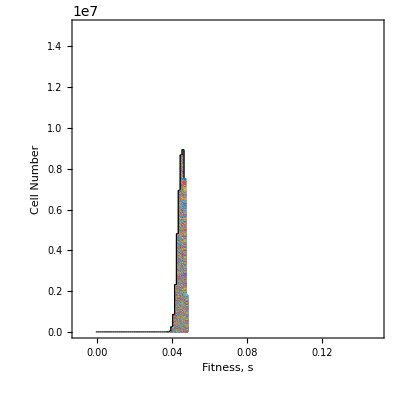

```mathematica
CrazyPlot=(*Rasterize[*)Graphics[AllRectangles, Background -> None, Axes -> True, PlotRange -> {{-0.01,0.15},{0, 15000000}},AspectRatio-> 1,FrameLabel->{Text[Style["Fitness, s", FontFamily-> "Helvetica", 10]],Text[Style["Cell Number", FontFamily-> "Helvetica", 10]]}, Frame -> True,FrameTicksStyle ->  Directive[FontFamily-> "Helvetica", 10], ImageSize-> {500}](*, RasterSize->1000]*)
```

```mathematica
Export[StringJoin["CrazyPlot2M3.pdf"],CrazyPlot3D,"PDF"];
```

## 9. Comparing to fluorescence based fitness measured by Sandeep

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/4M3"];
YFPFitnesses=Delete[ToExpression[Import["YFPFitnessMeasurements.csv"]], {1}];
```

```mathematica
ListOfYFPBarcodes=Map[First, YFPFitnesses];
```

```mathematica
YFPComparison=Table[
AllAdatpiveBarcodesList=Map[First,AllAdaptiveLineages];
BarcodeID=ListOfYFPBarcodes[[i]];
(*Print[BarcodeID];*)
If[MemberQ[AllAdatpiveBarcodesList, BarcodeID],PositionInList=Position[AllAdatpiveBarcodesList,BarcodeID][[1]][[1]];
(*Print[PositionInList];*)
 SequenceFitness=AllAdaptiveLineages[[PositionInList]][[6]];SequenceFitnessError=AllAdaptiveLineages[[PositionInList]][[7]];
ProbabilityAdaptive=AllAdaptiveLineages[[PositionInList]][[3]];, SequenceFitness=0.0; SequenceFitnessError=0.01;ProbabilityAdaptive=0.0;];
{BarcodeID,YFPFitnesses[[i]][[2]],YFPFitnesses[[i]][[3]], SequenceFitness, SequenceFitnessError,ProbabilityAdaptive}, {i, 1, Length[ListOfYFPBarcodes]}];
TableForm[YFPComparison]
```

151 | 0.107252 | 0.01125 | 0.166083 | 0.0155398 | 166.146
415 | 0.0971749 | 0.003479 | 0.126479 | 0.00441909 | 660.281
7961 | 0.0936212 | 0.008666 | 0.109068 | 0.00269763 | 1286.29
9888 | 0.0842182 | 0.00635 | 0.0904064 | 0.00206592 | 1107.71
2468 | 0.0820773 | 0.006029 | 0.101744 | 0.00120881 | 4894.31
25531 | 0.0803174 | 0.005535 | 0.112825 | 0.0025466 | 1298.4
309655 | 0.0688179 | 0.004838 | 0.0862179 | 0.0191103 | 10.7081
10851 | 0.0678635 | 0.005158 | 0.0874021 | 0.00207981 | 1093.94
19407 | 0.0669349 | 0.003654 | 0.0886944 | 0.00186814 | 1454.87
63215 | 0.0657803 | 0.003306 | 0.107312 | 0.00755723 | 204.623
121806 | 0.0634263 | 0.005043 | 0.0990238 | 0.0113793 | 82.7014
71751 | 0.0616195 | 0.005387 | 0.0597794 | 0.00608886 | 51.3624
189102 | 0.0580922 | 0.004559 | 0.0508287 | 0.00642262 | 37.4936
39674 | 0.0530347 | 0.005387 | 0.304821 | 0.021207 | 668.984
152501 | 0.0518598 | 0.005535 | 0.0490013 | 0.00720416 | 28.1613
127835 | 0.0433676 | 0.002467 | 0.0426441 | 0.00571378 | 29.3997
19697 | 0.0412616 | 0.003957 | 0.0491754 | 0.00933639 | 29.1473
33976 | 0.039884 | 0.006493 | 0.0431915 | 0.0061994 | 22.2963
18501 | 0.0391938 | 0.00341 | 0.0811031 | 0.00428271 | 319.224
75144 | 0.0377717 | 0.002688 | 0.0594092 | 0.00807524 | 103.421
101051 | 0.0349105 | 0.005158 | 0.034203 | 0.00520659 | 24.6912
310209 | 0.0335526 | 0.003306 | 0.0481208 | 0.00699702 | 18.831
28888 | 0.033173 | 0.005043 | 0.0426293 | 0.00573504 | 42.1549
170554 | 0.0313823 | 0.003654 | 0.0370475 | 0.00630076 | 22.7658
67711 | 0.0305635 | 0.003479 | 0.081684 | 0.0215464 | 22.3561
51200 | 0.030357 | 0.005258 | 0.0429422 | 0.0054894 | 53.7249
14280 | 0.030357 | 0.005258 | 0.0953259 | 0.00212985 | 1450.61
232264 | 0.0285665 | 0.004838 | 0.0450256 | 0.00718733 | 15.46
8825 | -0.000462491 | 0.0016632 | 0.0730082 | 0.00333235 | 357.178
72939 | -0.000944982 | 0.002864 | 0.00001 | 0.01 | -9.37803
58107 | -0.00141321 | 0.004533 | 0. | 0.01 | 0.
247616 | -0.006353 | 0.004533 | 0.00001 | 0.01 | -10.8063
29375 | -0.0102706 | 0.004559 | 0.123233 | 0.0058548 | 418.7

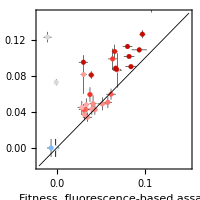

```mathematica
PointWithErrorBars[s1_,s2_,Error1_,Error2_, col_, Thic_, size_]:=Graphics[{Black, Thickness[0.002], Line[{{s1-Error1,s2},{s1+Error1,s2}}], Line[{{s1,s2-Error2},{s1,s2+Error2}}],EdgeForm[Thickness[Thic]],col,Disk[{s1, s2},Scaled[size]]}];

FitnessVerifyYFP=Show[{Table[
If[YFPComparison[[i]][[1]]==8825 || YFPComparison[[i]][[1]]==29375, Color=LightGray, Color=Scheme3[Log[YFPComparison[[i]][[6]]+20]/6]];
PointWithErrorBars[YFPComparison[[i]][[2]],YFPComparison[[i]][[4]],YFPComparison[[i]][[3]],YFPComparison[[i]][[5]], Color,0.001, 0.015], {i, 1, Length[YFPComparison]}], Plot[x, {x, -0.02, 0.15}, PlotStyle -> Directive[{Black, Thickness[0.003]}] ]}, Frame -> True, ImageSize -> 200,FrameLabel -> {Text[Style["Fitness, fluorescence-based assay ", FontFamily-> "Helvetica", 10]],Text[Style["Fitness, sequencing barcodes assay", FontFamily-> "Helvetica", 10]]}, PlotRange -> {{-0.02,0.15},{-0.02,0.15}}]
```

```mathematica
Export["FitnessVerify.eps",FitnessVerifyYFP,"EPS"]
```

FitnessVerify.eps

```mathematica
Correlation[DeleteCases[Table[
If[YFPComparison[[i]][[1]]==8825 || YFPComparison[[i]][[1]]==29375|| YFPComparison[[i]][[1]]==39674 ,,YFPComparison[[i]][[2]]], {i, 1, Length[YFPComparison]}], Null], DeleteCases[Table[
If[YFPComparison[[i]][[1]]==8825 || YFPComparison[[i]][[1]]==29375|| YFPComparison[[i]][[1]]==39674 ,,YFPComparison[[i]][[4]]], {i, 1, Length[YFPComparison]}], Null]]^2
```

0.78444

```mathematica
Length[YFPComparison]
```

33

## 10. Evolution of n(t)

Collect all barcode initially at an effective size of 400-480 cells i.e.

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/AllProcessedBarcodeData"];
AllAdaptiveLineages=ToExpression[Import["AdaptiveLineagesE1&E2.csv"]];
SetDirectory["~/Dropbox/BayesianAnalysis/2M3"];
ReadTrajectories2M3=ToExpression[Import["ReadTrajectories2M3.csv"]];
ReadDepths2M3=ToExpression[Import["ReadDepths2M3.csv"]];
```

Import::nffil: File not found during Import.

```mathematica
AdaptiveBarcodes=Map[First, AllAdaptiveLineages];
```

```mathematica
SmallestDepth=Min[Map[#[[2]]&,ReadDepths2M3]];
MeansForEach=Table[SmallestDepth/ReadDepths2M3[[i]][[2]], {i, 1, Length[ReadDepths2M3]}];
EquallySampledReads2M3=Table[
If[Mod[bc, 1000]==0,Print[bc]];Table[{ReadTrajectories2M3[[bc]][[t]][[1]],If[ReadTrajectories2M3[[bc]][[t]][[2]]>0,RandomVariate[PoissonDistribution[MeansForEach[[t]]*ReadTrajectories2M3[[bc]][[t]][[2]]]],0]}, {t, 1, Length[ReadDepths2M3]}], {bc, 1, Length[ReadTrajectories2M3]}];
Export["EquallySampledReads2M3.csv",EquallySampledReads2M3,"CSV"]
```

EquallySampledReads2M3.csv

```mathematica
AdaptiveSet={};
RangeOfInitialCellNumber=Interval[{98,102}];
Do[
If[IntervalMemberQ[ RangeOfInitialCellNumber,EquallySampledReads2M3[[Barcode]][[1]][[2]]], AppendTo[AdaptiveSet, Barcode]]
, {Barcode, 1, Length[EquallySampledReads2M3]}]
Length[AdaptiveSet]
```

9325

```mathematica
Distributiont[t_]:=Table[EquallySampledReads2M3[[i]][[t]][[2]], {i, AdaptiveSet}]
```

```mathematica
AllRectangles={};
LowerReadLimit=0;
UpperReadLimit=500;
BinWidth=2;

CrazyPlots=Table[
Print["Time point=",t];
BarcodesInEachReadBin={};
AllRectangles={};

Do[
(*Print["ReadBin=", ReadBin];*)

NumberOfCellsInFitnessBin=0.0;

BarcodesInRange={};
Do[If[ReadBin<EquallySampledReads2M3[[i]][[t]][[2]]<ReadBin+BinWidth, AppendTo[BarcodesInRange,i]];
, {i, AdaptiveSet}];
(*Print["InRange=",TableForm[BarcodesInRange]];*)
(*Print["NumberInRange=",Length[BarcodesInRange]];*)

 AppendTo[BarcodesInEachReadBin, {ReadBin,BarcodesInRange}];

,{ReadBin, LowerReadLimit,UpperReadLimit, BinWidth}];

(*Put all rectangles in table*)

PreviousHeight=0.0;
Do[
BCs=BarcodesInEachReadBin[[Bin]][[2]];
(*Print[BCs];*)
Binx=BarcodesInEachReadBin[[Bin]][[1]];
(*Print[Binx];*)
StartingN=0.0;
LowX=Binx-BinWidth;
HighX=Binx+BinWidth;

Do[
If[MemberQ[AdaptiveBarcodes, Barcode], PositionInList=Position[AdaptiveBarcodes, Barcode][[1]][[1]];If[AllAdaptiveLineages[[PositionInList]][[1]]>10, Color=c2, Color=c6],Color=c6];
RectangleCoords={EdgeForm[Color],Polygon[{{Binx-BinWidth/2,StartingN},{Binx-BinWidth/2,StartingN+1},{Binx+BinWidth/2,StartingN+1},{Binx+BinWidth/2,StartingN}}]};
StartingN=StartingN+2;
AppendTo[AllRectangles, Color];
AppendTo[AllRectangles,RectangleCoords];
, {Barcode, BCs}];
(*AppendTo[AllRectangles,{Black,Thickness[0.002],Line[{{Binx-BinWidth/2,PreviousHeight},{Binx-BinWidth/2,StartingN}, {Binx+BinWidth/2,StartingN}}]}];*)
(*Print[Bin];*)
PreviousHeight=StartingN;

, {Bin, 1,Length[BarcodesInEachReadBin]}];




SetOfHeightsAt[t_]:=HistogramList[Table[EquallySampledReads2M3[[i]][[t]][[2]], {i,AdaptiveSet}], {BinWidth}][[2]];
SetOfHeightsForThisTime=SetOfHeightsAt[t];
DistanceOfFit[a_, b_, HeightScale_]:=Total[Table[N[(SetOfHeightsForThisTime[[i]]-HeightScale*Exp[LogProb[a, b, BinWidth*i]])^2], {i, 1, Length[SetOfHeightsForThisTime]}]];
BestFit=FindMinimum[{DistanceOfFit[a, b, cc], 50<a<110, 1<b<10, 1000<cc<30000}, {{a, 100}, {b, 4}, {cc, 10000}}];
Bestcc=BestFit[[2]][[3]][[2]];
Bestb=BestFit[[2]][[2]][[2]];
Besta=BestFit[[2]][[1]][[2]];

BestFitPlot=ListPlot[Table[{BinWidth*i,Bestcc*Exp[LogProb[Besta, Bestb, BinWidth*(i+1)]]}, {i, 1, Length[pp]}], Joined -> True, PlotStyle -> Black];

CrazyPlot=Show[{Graphics[AllRectangles, Background -> None, Axes -> True, PlotRange -> {{0, 500},{0, 300}},AspectRatio-> 1,FrameLabel->{Text[Style["Lineage size", FontFamily-> "Helvetica", 10]],Text[Style["Number of barcodes", FontFamily-> "Helvetica", 10]]}, Frame -> True,FrameTicksStyle ->  Directive[FontFamily-> "Helvetica", 10], ImageSize-> 200], BestFitPlot}];

Export[StringJoin["PorpagatedDistribution",ToString[t],".pdf"],CrazyPlot,"PDF"]


, {t, 8, 8, 1}];
```

Time point=8

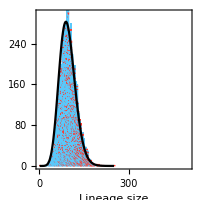

```mathematica
CrazyPlot
```

## 11. Simulation of mean fitnes with inferred μ(s)

Importing the data

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/AllProcessedBarcodeData_Carbon"];
AllAdaptiveLineages=ToExpression[Import["AdaptiveLineagesE1&E2.csv"]];
```

```mathematica
TableForm[AllAdaptiveLineages[[1;;20]], TableHeadings->{{},{"BC","Log(Pr[b]/Pr[n])_1","Log(Pr[b]/Pr[n])_2","s_1","δs_1","s_2","δs_2","τ_1","δτ_1", "τ_2","δτ_2"}}]
```

| BC | Log(Pr[b]/Pr[n])_1 | Log(Pr[b]/Pr[n])_2 | s_1 | δs_1 | s_2 | δs_2 | τ_1 | δτ_1 | τ_2 | δτ_2
 | 1 | -10.3503 | 437.533 | 0.00001 | 0.01 | 0.0874863 | 0.00324045 | 0 | 5 | -10.7233 | 3.50301
 | 2 | -8.94149 | -9.62843 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 3 | -6.31793 | -9.7379 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 7 | -6.18343 | -8.93869 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 14 | -6.51442 | -8.40835 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 15 | 6150.88 | -5.8308 | 0.103664 | 0.00111082 | 0.00001 | 0.01 | 0.800242 | 1.08688 | 0 | 5
 | 16 | -7.31047 | -9.49237 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 17 | -4.87625 | -8.63283 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 18 | -10.1805 | -9.32023 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 23 | -10.387 | -10.0314 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 25 | 35.8729 | 53.4893 | 0.0320317 | 0.00389843 | 0.0441855 | 0.00489694 | -88.3419 | 20.7353 | -66.5693 | 15.5798
 | 26 | -11.5497 | -11.3295 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 31 | -8.94454 | -9.95944 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 32 | 4804.87 | -9.82457 | 0.106252 | 0.00125173 | 0.00001 | 0.01 | 5.88589 | 1.1374 | 0 | 5
 | 33 | 0.931429 | -5.82122 | 0.0308673 | 0.00855509 | 0.00001 | 0.01 | -67.3532 | 43.0152 | 0 | 5
 | 34 | -8.73268 | -10.0516 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 35 | -9.89479 | -4.51869 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 36 | 9.77161 | 2.36768 | 0.0280161 | 0.00569951 | 0.0322031 | 0.00991143 | -99.2854 | 37.263 | -90.7373 | 50.1489
 | 37 | -7.62162 | -9.68673 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5
 | 38 | -10.2606 | -10.5248 | 0.00001 | 0.01 | 0.00001 | 0.01 | 0 | 5 | 0 | 5

```mathematica
PreExistingBarcodes=Select[AllAdaptiveLineages, (#[[2]]>1 &&#[[3]]>1&& #[[8]]<-0/(#[[4]])&&#[[10]]<-0/(#[[6]]))&];
Length[PreExistingBarcodes]
FitnessTimeOfPreX=Map[{#[[4]], #[[8]]}&,PreExistingBarcodes];
```

8167

```mathematica
DeltaS=0.01;
```

```mathematica
InitialFrequencies[PreExistingFitnessTimes_, DeltaS_]:=Module[{FitnessNewTimes,InitialFreqs,FreqsByFitness,TotalFreqByFitness, FitnessOfClass, FreqOfBin},
FitnessNewTimes=Map[{#[[1]], #[[2]]+RandomVariate[NormalDistribution[0,1]]*1.5/(#[[1]])}&,PreExistingFitnessTimes];
InitialFreqs=Map[{#[[1]], Exp[#[[1]]*(-#[[2]])]/(#[[1]]*5*10^8)}&,FitnessNewTimes];
FreqsByFitness=GatherBy[InitialFreqs, Round[(#[[1]])/DeltaS]&];
TotalFreqByFitness=Sort[Table[
FitnessOfClass=DeltaS*Round[(FreqsByFitness[[k]][[1]][[1]])/DeltaS];

FreqOfBin=Sum[FreqsByFitness[[k]][[i]][[2]], {i, 1, Length[FreqsByFitness[[k]]]}];

{N[FitnessOfClass],FreqOfBin}, {k,1, Length[FreqsByFitness]}]];
TotalFreqByFitness]
```

The inferred distribution

```mathematica
AdaptiveOnly2M3=Select[AllAdaptiveLineages, (#[[2]]>1 &&#[[3]]<0&& #[[8]]>-4/(#[[4]]))&];

AdaptiveOnly4M3=Select[AllAdaptiveLineages, (#[[3]]>1 &&#[[2]]<0&& #[[10]]>-4/(#[[6]]))&];

InferredByFitness2M3=GatherBy[AdaptiveOnly2M3, Round[(#[[4]])/DeltaS]&];
InferredByFitness4M3=GatherBy[AdaptiveOnly4M3, Round[(#[[6]])/DeltaS]&];
TauOffset=0;

PopSize=5*10^8;

InferredMutationRatesToClasses2M3=Sort[Table[
FitnessOfClass=DeltaS*Round[(InferredByFitness2M3[[k]][[1]][[4]])/DeltaS];


MutationRateToBin=1/(PopSize (1+FitnessOfClass *Log[10^-5*10^12]))Sum[Exp[-InferredByFitness2M3[[k]][[i]][[4]]*(InferredByFitness2M3[[k]][[i]][[8]]+TauOffset)], {i, 1, Length[InferredByFitness2M3[[k]]]}];

MutationBound= MutationRateToBin ;

{N[FitnessOfClass], MutationBound}, {k,1, Length[InferredByFitness2M3]}]][[1;;Round[0.20/DeltaS]]];


InferredMutationRatesToClasses4M3=Sort[Table[
FitnessOfClass=DeltaS*Round[(InferredByFitness4M3[[k]][[1]][[6]])/DeltaS];


MutationRateToBin=1/(PopSize(1+FitnessOfClass *Log[10^-5*10^12]))Sum[Exp[-InferredByFitness4M3[[k]][[i]][[6]]*(InferredByFitness4M3[[k]][[i]][[10]]+TauOffset)], {i, 1, Length[InferredByFitness4M3[[k]]]}];
MutationBound= MutationRateToBin;

{N[FitnessOfClass], MutationBound}, {k,1, Length[InferredByFitness4M3]}]][[1;;Round[0.20/DeltaS]]];
```

Frequencies of new mutants by fitness at time t

```mathematica
Tau[R_, s_, k_]:=Module[{MedianTau, LowerTau, UpperTau, NumberOfTauBins, dTau, RhoDeltaTau, CumulativeRho, NormalizedCumulative, TauList, NuList, NearestValueInCumulative, PositionInCumulative, TauSample},

If[R<10,
MedianTau=-(1/s)Log[R];
LowerTau=MedianTau-(4/s);
UpperTau=MedianTau+(10/s);
NumberOfTauBins=1000;
dTau=(UpperTau-LowerTau)/NumberOfTauBins;

RhoDeltaTau=Table[(s*dTau)/Gamma[R]*Exp[-R s tau-Exp[-s tau]], {tau, LowerTau,UpperTau, dTau}];
CumulativeRho=Table[Sum[RhoDeltaTau[[i]], {i, 1, j}], {j,1,Length[RhoDeltaTau]}];

NormalizedCumulative=CumulativeRho/Max[CumulativeRho];

TauList=Table[
beta=RandomReal[];
(*Print[beta];*)
NearestValueInCumulative=Nearest[NormalizedCumulative, beta][[1]];
(*Print[NearestValueInCumulative];*)
PositionInCumulative=Position[NormalizedCumulative,NearestValueInCumulative][[1]][[1]];
TauSample=LowerTau+PositionInCumulative*dTau;
TauSample, {j, 1, k}];,

NuList=Table[RandomVariate[GammaDistribution[R,1]], {j, 1, k}];
TauList=Table[-(1/s)Log[NuList[[i]]], {i, 1, Length[NuList]}];
];
TauList
]
```

```mathematica
MeanFitnessTrajectory[FitnessRates_,InitialFitnessFreqList_]:=Module[{R, s, τ, InitialSize, InitialFreq, FitnessFreqListPreX,FitnessFreqList, MeanAttPreX, MeanAttNotPreX, MeanAtt, InitialFitnessFreqsPreX, OldFreq, NewFreq},

InitialFitnessFreqsPreX=Table[
R=6*10^8*FitnessRates[[i]][[2]];
s= FitnessRates[[i]][[1]];
τ=Tau[R, s,1][[1]];
InitialSize=Exp[s(-τ)]/s;
InitialFreq=InitialSize/(5*10^8);
{s,InitialFreq}, {i, 1, Length[FitnessRates]}];
(*Print[FitnessFreqs];*)

MeanAtt=0;

FitnessFreqListPreX=InitialFitnessFreqsPreX;
FitnessFreqList=InitialFitnessFreqList;

Table[

FitnessFreqListPreX=Table[
s=FitnessFreqListPreX[[i]][[1]];
OldFreq=FitnessFreqListPreX[[i]][[2]];
NewFreq=OldFreq*Exp[(s-MeanAtt)];
{s,NewFreq}
, {i, 1, Length[FitnessFreqListPreX]}];
MeanAttPreX=Sum[FitnessFreqListPreX[[i]][[1]]*FitnessFreqListPreX[[i]][[2]],{i, 1, Length[FitnessFreqListPreX]}];

FitnessFreqList=Table[
s=FitnessFreqList[[i]][[1]];
OldFreq=FitnessFreqList[[i]][[2]];
NewFreq=OldFreq Exp[(s-MeanAtt)];
{s,NewFreq}, {i, 1, Length[FitnessFreqList]}];
MeanAttNotPreX=Sum[FitnessFreqList[[i]][[1]]*FitnessFreqList[[i]][[2]],{i, 1, Length[FitnessFreqList]}];

MeanAtt=MeanAttPreX+MeanAttNotPreX;

MeanAtt
, {t, 1, 120}]
]
```

```mathematica
SimulatedMeans2M3=Table[MeanFitnessTrajectory[InferredMutationRatesToClasses2M3,InitialFrequencies[FitnessTimeOfPreX, DeltaS]], {k, 1, 500}];
SimulatedMeans4M3=Table[MeanFitnessTrajectory[InferredMutationRatesToClasses4M3,InitialFrequencies[FitnessTimeOfPreX, DeltaS]], {k, 1, 500}];
```

```mathematica
SimulatedTrajectoryPlot2M3[traj_]:=ListPlot[traj, Joined -> True,ImageSize -> 250,Frame -> True,PlotStyle -> RGBColor[1.0,0.75,0.75,0.1],FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Mean Fitness", FontFamily-> "Helvetica", 10]]}, PlotRange -> {{0, 120},{0, 0.1}}];

SimulatedTrajectoryPlot4M3[traj_]:=ListPlot[traj, Joined -> True,ImageSize -> 250,Frame -> True,PlotStyle ->RGBColor[64/255, 204/255, 255/255, 0.1],FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Mean Fitness", FontFamily-> "Helvetica", 10]]}, PlotRange -> {{0, 120},{0, 0.1}}];
```

```mathematica
BothSimulatedMeans=RandomSample[Join[Table[SimulatedTrajectoryPlot2M3[SimulatedMeans2M3[[i]]], {i, 1, Length[SimulatedMeans2M3]}],Table[SimulatedTrajectoryPlot4M3[SimulatedMeans4M3[[i]]], {i, 1, Length[SimulatedMeans4M3]}]], Length[SimulatedMeans4M3]+Length[SimulatedMeans2M3]];
```

```mathematica
SimulatedTrajectories=Show[BothSimulatedMeans];
MeasuredTrajectories=Show[{ListPlot[{MeanFit2M3, MeanFit4M3}, PlotStyle -> {Darker[c2, 0.1],Darker[c7, 0.2]}, Joined -> True, PlotRange -> {{0,120},{-0.001, 0.1}}, ImageSize -> 170,Frame -> True,FrameLabel -> {Text[Style["Time (generations)", FontFamily-> "Helvetica", 10]],Text[Style["Mean Fitness", FontFamily-> "Helvetica", 10]]}]}];
```

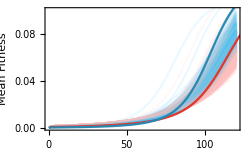

```mathematica
MeansSimulated=Show[{SimulatedTrajectories, MeasuredTrajectories}, ImageSize -> 250]
```

```mathematica
Export["MeansSimulated.pdf",MeansSimulated,"PDF"]
```

MeansSimulated.pdf

## End: Color palette

-Graphics-

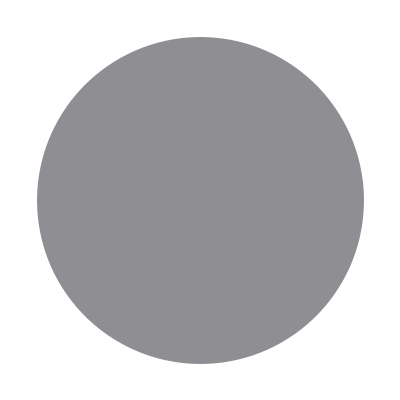
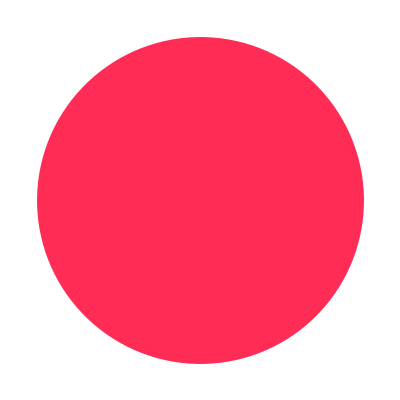
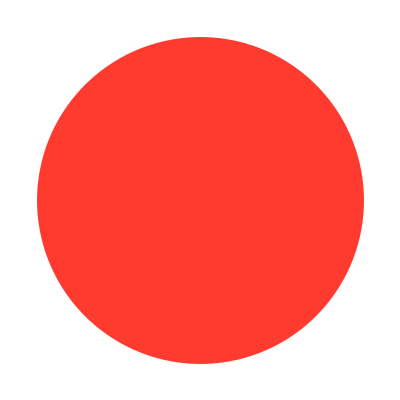
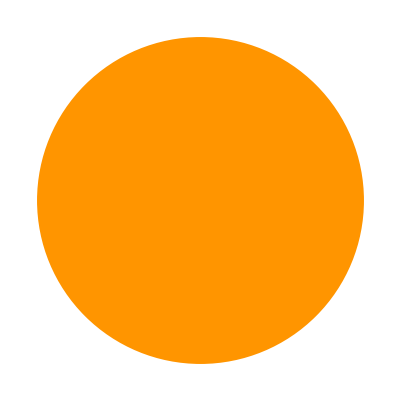
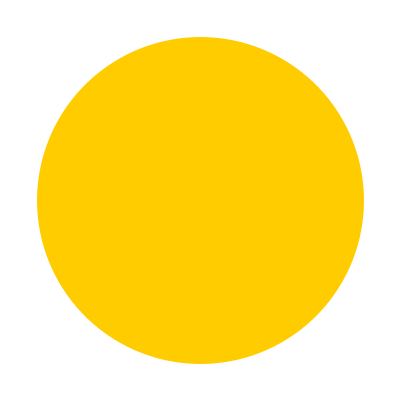
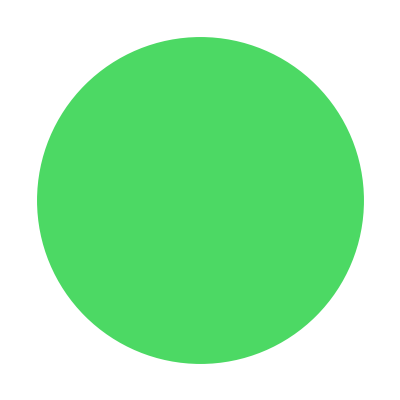
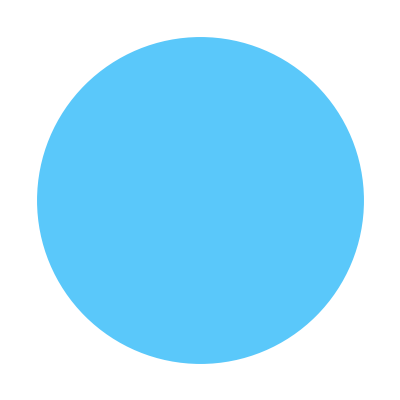
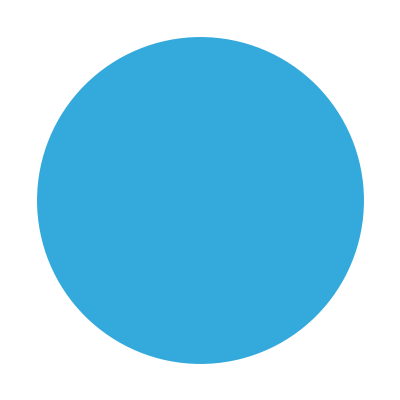
| c0 | c1 | c2 | c3 | c4 | c5 | c6 | c7 | c8 | c9 | c10 | c11 | c12
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
c0=RGBColor[142/255, 142/255, 147/255, 1];
c1a=RGBColor[0.6*255/255, 0.6*45/255, 0.6*85/255, 1];
c1=RGBColor[255/255, 45/255, 85/255, 1];
c2=RGBColor[255/255, 59/255, 48/255, 1];
c3=RGBColor[255/255, 149/255, 0/255, 1];
c4=RGBColor[255/255, 204/255, 0/255, 1];
c5=RGBColor[76/255, 217/255, 100/255, 1];
c6=RGBColor[90/255, 200/255, 250/255, 1];
c7=RGBColor[52/255, 170/255, 220/255, 1];
c8=RGBColor[0/255, 122/255, 255/255, 1];
c9=RGBColor[88/255, 86/255, 214/255, 1];
c10=RGBColor[0/255, 80/255, 145/255, 1];
c11=RGBColor[30/255, 75/255, 175/255, 1];
c12=RGBColor[0.5*88/255,0.5* 86/255,0.5* 214/255, 1];
c13=RGBColor[1,1,1,1]

ColorList=Append[Reverse[Table[ToExpression[StringJoin["c",ToString[i]]], {i, 1, 12}]], c1a];

Markers[s_, col_, Edge_]:=Graphics[{EdgeForm[Edge],col,Disk[{0,0},Scaled[s]]}];
Markers3[s_, col_, Edge_]:=Graphics[{EdgeForm[Edge],col,Rectangle[Scaled[{s,s}],Scaled[{0,0}]]}];
Markers2[s_,Error1_,Error2_, col_, Thic_]:=Graphics[{Thickness[Thic],col,Rectangle[{{-Error1,-Error2},{Error1,Error2}},Scaled[s]]}];

ClearMemory:=Module[{},Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];];

Scheme1[x_]:=Blend[{c0,White}, x]
Scheme2[x_]:=Blend[{c1,c5, c0}, x]
Scheme3[x_]:=Blend[{c10,c8,c13,c2, RGBColor[0.77,0.04,0.]}, x]
Scheme4[x_]:=Blend[{c1,c3,c5, c7, c9}, x]

TableForm[{Table[Graphics[{ToExpression[StringJoin["c",ToString[i]]],Disk[{0.5,0.5},0.05]}], {i, 0, 12}]}, TableHeadings -> {{},Table[StringJoin["c", ToString[i]], {i, 0, 12}]}, TableSpacing -> {0, -3}]
```

```mathematica
Pos={{0, -20},{0.2, -16}, {0.4, -8}, {0.5, 0}, {0.6, 15}, {0.8, 100}, {1.0, 300}};

Pos2=Table[{i/0.14, i}, {i, 0, 0.14, 0.02}];
```

```mathematica
ScaleBar=DensityPlot[y,{x,0,1},{y,0,1},ColorFunction->Scheme3,ColorFunctionScaling->False,AspectRatio->15, FrameTicks->{{Table[{Pos[[i]][[1]], Superscript[10, Pos[[i]][[2]]]}, {i, 1, 7}],None},{None,None}} (*,FrameLabel -> {,Text[Style["P(beneficial)/P(neutral)", FontFamily-> "Helvetica", 13]]}*), PlotRangePadding ->None, ImageSize -> 36]

ScaleBar2=DensityPlot[y,{x,0,1},{y,0,1},ColorFunction->Scheme3,ColorFunctionScaling->False,AspectRatio->15, FrameTicks->{{Table[{Pos2[[i]][[1]], Pos2[[i]][[2]]}, {i, 1, Length[Pos2]}],None},{None,None}} (*,FrameLabel -> {,Text[Style["P(beneficial)/P(neutral)", FontFamily-> "Helvetica", 13]]}*), PlotRangePadding ->None, ImageSize -> 36]
```

-Graphics-

-Graphics-

```mathematica
Export["ScaleBar2.pdf",ScaleBar2,"AllowRasterization"->True,ImageResolution->400]
```

ScaleBar2.pdf

```mathematica
SetDirectory["~/Dropbox/BayesianAnalysis/2M3"];
pb1=ToExpression[Import["BayesianAnalysis2M3_1-100000.csv"]];
pb2=ToExpression[Import["BayesianAnalysis2M3_100001-300000.csv"]];
pb3=ToExpression[Import["BayesianAnalysis2M3_300001-End.csv"]];
Combined=Flatten[Join[pb1, pb2, pb3], {1}];
```

```mathematica
Export["BayesianAnalysis2M3.csv",Combined,"CSV"]
```

BayesianAnalysis2M3.csv